```mathematica
(*
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
*)
```

```mathematica
data=Import["/home/jose/Files/Complex Systems/proyecto/alltokens.csv", "Data"];
size = Length[data];
```

Text Normalization

```mathematica
Table[If[StringQ[data[[i,2]]],data[[i,2]]=RemoveDiacritics[ToLowerCase[data[[i,2]]]]],{i,Length[data]}];

(* cre acion de las entidades en el dataset *)
entidad = EntityStore["cpt"-> <|"Entities"-> <||>|>];
EntityRegister[entidad]
For[i=2,i<size-1,i++,Module[{},Entity["cpt",ToString[data[[i,2]]]]["label"]= ToString[data[[i,4]]]]];
EntityList[Entity["cpt"]];
```

EntityRegister::shadow: Types {cpt} in EntityStore[<|Types→<|cpt→<|Entities→<||>|>|>|>] already exist. The existing ones will be shadowed.

{cpt}

```mathematica
(*Vista del dataset*)
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView
```

patient_idfracedocument_idtoken_cancer136631carcinoma de mama0CANCER_CONCEPT136631primario0CANCER_CONCEPT136631tamoxifeno0DRUG136631tumor maligno de la mama parte no especificada0CANCER_CONCEPT21723135 anos1AGE217231acetato1DRUG217231acetato de1DRUG217231acido1DRUG217231cancer de mama1CANCER_CONCEPT217231cuadrantectoma1SURGERY217231goserelina1DRUG217231metastasis clasificada en otra1CANCER_CONCEPT217231politerapia antineoplasica1TREATMENT_NAME217231primario1CANCER_CONCEPT217231t4bn1m11TNM217231tumor maligno de la mama parte no especificada1CANCER_CONCEPT217231tumor maligno secundario de los huesos y la osea1CANCER_CONCEPT217231tamoxifeno1DRUG217231carcinoma ductal infiltrante mod desmopasico1CANCER_CONCEPT217231carcinoma metastasico primario mama1CANCER_CONCEPT217231goserelina1DRUG217231quimioterapia1TREATMENT_NAME217231quimioterapia : 11TREATMENT_NAME217231quimioterapia ambulatoria1TREATMENT_NAME217231soplos1COMORBIDITY217231tumoral1CANCER_CONCEPT217231zoledronico1DRUG21723141 anos2AGE217231politerapia antineoplasica2TREATMENT_NAME217231tumor maligno de mama2CANCER_CONCEPT217231acetato2DRUG217231goserelina2DRUG217231quimioterapia2TREATMENT_NAME21723141 anos3AGE217231acetato3DRUG217231acetato de3DRUG217231acido3DRUG217231cancer de mama3CANCER_CONCEPT217231cuadrantectoma3SURGERY217231goserelina3DRUG217231politerapia antineoplasica3TREATMENT_NAME217231primario3CANCER_CONCEPT217231t4bn1m13TNM217231tumor maligno del cuadrante inferior externo de la mama3CANCER_CONCEPT217231tamoxifeno3DRUG217231carcinoma ductal infiltrante mod desmopasico3CANCER_CONCEPT217231carcinoma metastasico primario mama3CANCER_CONCEPT217231goserelina3DRUG217231quimioterapia3TREATMENT_NAME217231quimioterapia : 13TREATMENT_NAME217231quimioterapia ambulatoria3TREATMENT_NAME217231soplos3COMORBIDITY217231tumoral3CANCER_CONCEPT217231zoledronico3DRUG287106ca de mama ductal infiltrante de mama izquierda4CANCER_CONCEPT287106carcinoma ductal infiltrante4CANCER_CONCEPT287106carcinoma ductal infiltrante de4CANCER_CONCEPT287106cmi4CANCER_CONCEPT287106cuadrantectomia : 14SURGERY287106m04TNM287106pt2 2 34TNM287106primario4CANCER_CONCEPT287106quimioterapia4TREATMENT_NAME287106quimioterapiaanamnesis4TREATMENT_NAME287106tt : 14TREATMENT_NAME287106tumor maligno de la prolongacion axilar de la mama4CANCER_CONCEPT287106tamoxifeno4DRUG287106trastuzumab4DRUG287106pt2n2m04TNM287106quimioterapia ambulatoria4TREATMENT_NAME28710631 anos5AGE287106politerapia antineoplasica5TREATMENT_NAME287106tumor maligno de mama5CANCER_CONCEPT287106quimioterapia5TREATMENT_NAME287106trastuzumab5DRUG287106ca de mama ductal infiltrante de mama izquierda6CANCER_CONCEPT287106carcinoma ductal infiltrante6CANCER_CONCEPT287106carcinoma ductal infiltrante de6CANCER_CONCEPT287106cmi6CANCER_CONCEPT287106cuadrantectomia : 16SURGERY287106m06TNM287106pt2 2 36TNM287106primario6CANCER_CONCEPT287106tumor maligno de la prolongacion axilar de la mama6CANCER_CONCEPT287106tamoxifeno6DRUG287106trastuzumab6DRUG287106pt2n2m06TNM287106quimioterapia6TREATMENT_NAME287106quimioterapia : 16TREATMENT_NAME743911977AGE74391677AGE74391887AGE74391ac 47DRUG74391ca mama izquierda7CANCER_CONCEPT74391cuadrantectomia7SURGERY74391carcinoma ductal infiltrante mod diferenciado7CANCER_CONCEPT74391primario7CANCER_CONCEPT74391radioterapia7TREATMENT_NAME74391tamoxifeno7DRUG74391tumor maligno de la mama parte no especificada7CANCER_CONCEPT74391ca de mama metastasico a pleura7CANCER_CONCEPT74391capecitabina7DRUG74391carcinoma de origen mamario7CANCER_CONCEPT74391carcinoma ductal metastasico7CANCER_CONCEPT74391dexametasona7DRUG74391docetaxel7DRUG74391esteatosis hepatica moderada7COMORBIDITY74391metastasis7CANCER_CONCEPT74391ondansetron7DRUG74391prednisona7DRUG74391quimioterapia7TREATMENT_NAME30664136 neu8AGE306641588AGE306641608AGE306641678AGE306641ac8DRUG306641cancer de mama izquierda8CANCER_CONCEPT306641mama8CANCER_CONCEPT306641metastasis8CANCER_CONCEPT306641metastasis neg8CANCER_CONCEPT306641primario8CANCER_CONCEPT306641tumor maligno de la mama parte no especificada8CANCER_CONCEPT306641ac8DRUG306641adenopatias8COMORBIDITY306641carcinoma ductal infiltrante8CANCER_CONCEPT306641carcinoma ductal metastasico8CANCER_CONCEPT306641creatinina8DRUG306641dexametasona8DRUG306641hidroxicina8DRUG306641lesion8CANCER_CONCEPT306641metastasis8CANCER_CONCEPT306641ondasetron8DRUG306641paclitaxel8DRUG306641prednisona8DRUG306641quimioterapia8TREATMENT_NAME306641quimioterapia neoadyuante8TREATMENT_NAME306641t4bn1mx8TNM306641taxol8DRUG306641tratamiento neoadyuvante8TREATMENT_NAME306641tumoral en izquierdo8CANCER_CONCEPT333678carlos9CANCER_CONCEPT333678ca de mama izquierda10CANCER_CONCEPT333678carlos10CANCER_CONCEPT333678hta10COMORBIDITY333678llamaron10DRUG333678reseccion por cx10SURGERY333678sarcoma fusocelular de alto grado10CANCER_CONCEPT333678tumor maligno de la porcion de la mama10CANCER_CONCEPT33367874 anos11AGE333678ca de mama izquierda11CANCER_CONCEPT333678carlos11CANCER_CONCEPT333678hta11COMORBIDITY333678lesion11CANCER_CONCEPT333678llamaron11DRUG333678primario11CANCER_CONCEPT333678reseccion por cx11SURGERY333678sarcoma fusocelular de alto grado11CANCER_CONCEPT333678tumor maligno de la mama parte no especificada11CANCER_CONCEPT33367874 anos12AGE333678lesion de la mama12CANCER_CONCEPT333678tumor maligno de la mama parte no especificada de torax12CANCER_CONCEPT333678cirugia plastica12SURGERY33367874 anos13AGE333678lesion de la mama13CANCER_CONCEPT333678tumor maligno de la mama parte no especificada13CANCER_CONCEPT33367874 anos14AGE33367874 anos14AGE333678ca de mama izquierda fusocelular de alto grado14CANCER_CONCEPT333678cancer de mama izquierda fusocelular de alto grado14CANCER_CONCEPT333678lesion de mama14CANCER_CONCEPT333678tramadol14DRUG333678tumor maligno de la mama parte no especificada14CANCER_CONCEPT33367874 anos15AGE333678trataminto farmacologico corespondiente15TREATMENT_NAME33367874 anos16AGE333678lesion de la mama16CANCER_CONCEPT333678tumor maligno de la mama parte no especificada urgente16CANCER_CONCEPT33367874 anos17AGE333678creatinina17DRUG333678lesion de la mama17CANCER_CONCEPT333678sarcoma fusocelular de alto grado en mama izquierda17CANCER_CONCEPT333678tumor maligno de la mama parte no especificada17CANCER_CONCEPT3336784019AGE3336785219AGE3336785919AGE33367874 anos20AGE33367874 anos20AGE333678caycedo20CANCER_CONCEPT333678caicedo20CANCER_CONCEPT333678caicedo20CANCER_CONCEPT333678lesion de mama20CANCER_CONCEPT333678tumor maligno de la mama parte no especificada20CANCER_CONCEPT333678cefalexina20DRUG333678reseccion20SURGERY33367847 1321AGE33367847 : 1822AGE333678cefazolina22DRUG333678qx 7 522TREATMENT_NAME33367874 anos23AGE333678cefazolina23DRUG333678cirugia de mama23SURGERY333678cirugia del23SURGERY333678cirugia reconstructiva23SURGERY333678lesion23CANCER_CONCEPT333678mastectomia23SURGERY333678prolene23DRUG333678reconstruccion23SURGERY333678resecan23SURGERY333678reconstruccion de la23SURGERY333678reintervencion23SURGERY333678toraxacto23SURGERY333678tumor maligno de la mama parte no especificada 3 4to23CANCER_CONCEPT3336784724AGE333678cx24DRUG33367874 anos26AGE333678lesion26CANCER_CONCEPT333678tumor maligno de la mama parte no especificada26CANCER_CONCEPT33367813 :27AGE3336784727AGE33367874 anos27AGE333678adenocarcinoma27CANCER_CONCEPT333678angiosarcoma27SURGERY333678carolina de mama de27DRUG333678cefalexina27DRUG333678cirugia electiva27SURGERY333678cirugia reconstructiva27SURGERY333678dipirona27DRUG333678escision de mama27SURGERY333678glandula mamaria en27SURGERY333678hemoglobina27DRUG333678lesion mama27CANCER_CONCEPT333678mastectomia colgajo compuesto27SURGERY333678metoclopramida27DRUG333678mastectomia simple con escision27SURGERY333678primario27CANCER_CONCEPT333678ranitidina27DRUG333678reseca de27SURGERY333678reseccion27SURGERY333678reseccion en bloque de la27SURGERY333678resecion izquierdos27SURGERY333678reintervencion27SURGERY333678trasfunidr27DRUG333678tumor27CANCER_CONCEPT333678tumor maligno de la mama parte no especificada27CANCER_CONCEPT333678valsartan27DRUG33367813 :28AGE3336784728AGE33367874 anos28AGE333678cirugia urgente28SURGERY333678lesion mama28CANCER_CONCEPT333678tumor maligno de la mama parte no especificada28CANCER_CONCEPT333678dren30DRUG333678valumpack30DRUG33367847 intensiva 3 ocniente31AGE33367874 anos34AGE333678tumor maligno de la mama parte no especificada34CANCER_CONCEPT333678tumor maligno de la mama parte no especificadaanamnesis35CANCER_CONCEPT333678terapia35TREATMENT_NAME33367874 anos37AGE333678afebril37DRUG333678ca de mama37CANCER_CONCEPT333678ca de mama izquierda37CANCER_CONCEPT333678ca de mama izquierda fusocelular de alto grado37CANCER_CONCEPT333678hta37COMORBIDITY333678lesion37CANCER_CONCEPT333678rot37TREATMENT_NAME333678tumor maligno de la mama parte no especificada37CANCER_CONCEPT333678terapia37TREATMENT_NAME333678tumor radioinducido37CANCER_CONCEPT333678valsartan37DRUG333678clorhexidina37DRUG333678hartman37DRUG333678mastectomia radical37SURGERY333678reconstruccion con colgajo37SURGERY333678reconstruccion con colgajo intensivos37SURGERY333678sarcoma fusocelular de alto grado37CANCER_CONCEPT333678soplos 21 % 99%37COMORBIDITY333678carmen 341CANCER_CONCEPT333678mastectomia radical45SURGERY3336787446AGE33367874 anos46AGE333678dren hemovac46DRUG333678lesion46CANCER_CONCEPT333678tumor maligno de la mama parte especificada46CANCER_CONCEPT33367874 anos47AGE333678lesion47CANCER_CONCEPT333678tumor maligno de la mama parte no especificada47CANCER_CONCEPT33367874 anos48AGE333678lesion48CANCER_CONCEPT333678mastectomia halsted48SURGERY333678pop48SURGERY333678reconstruccion mamaria inmediata48SURGERY333678reseccion48SURGERY333678toracostomia48SURGERY333678toracostomia con debito minimo48SURGERY333678toracostomia sin fuga48SURGERY333678tumor maligno de la mama parte no especificada48CANCER_CONCEPT33367874 anos51AGE333678acido lactico : 1 951DRUG333678ca de mama izquierda51CANCER_CONCEPT333678cefalexina51DRUG333678dipirona51DRUG333678enoxaparina51DRUG333678glucometrias51SURGERY333678hc fusocelular de alto grado51COMORBIDITY333678hta51COMORBIDITY333678lesion51CANCER_CONCEPT333678mastectomia colgajo compuesto51SURGERY333678metoclopramida51DRUG333678omeprazol51DRUG333678oxicodona51DRUG333678resecion51SURGERY333678rot51TREATMENT_NAME333678tumor maligno de la mama parte no especificada51CANCER_CONCEPT333678terapia51TREATMENT_NAME333678transaminasas51DRUG333678tumor radioinducido51CANCER_CONCEPT333678valsartan51DRUG333678ast 1551DRUG333678clorhexidina51DRUG333678fosforo 551DRUG333678hto51TNM333678lactato51DRUG333678magnesio51DRUG333678mastectomia radical izquierda+51SURGERY333678mastectomia radical51SURGERY333678potasio51DRUG333678ptt 3151TNM333678reconstruccion con colgajo51SURGERY333678reseccion de costales de51SURGERY333678sodio51DRUG333678soplos 32 % mg/dl 24 horas51COMORBIDITY33367874 anos52AGE333678tumor maligno de la mama parte no especificadaanamnesis52CANCER_CONCEPT333678terapia52TREATMENT_NAME333678cystoflo54DRUG333678mastectomia radical54SURGERY333678kardex55DRUG33367874 anos56AGE333678tumor maligno de la mama parte no especificadaanamnesis56CANCER_CONCEPT333678terapia56TREATMENT_NAME33367874 anos58AGE333678ca de mama izquierda58CANCER_CONCEPT333678cefalexina58DRUG333678dieta58COMORBIDITY333678dipirona58DRUG333678enoxaparina58DRUG333678glucometrias58SURGERY333678hc fusocelular de alto grado58COMORBIDITY333678hta58COMORBIDITY333678lesion58CANCER_CONCEPT333678omeprazol58DRUG333678oxicodona58DRUG333678rot58TREATMENT_NAME333678tumor maligno de la mama parte no especificada58CANCER_CONCEPT333678terapia58TREATMENT_NAME333678tumor radioinducido58CANCER_CONCEPT333678valsartan58DRUG333678clorhexidina58DRUG333678hartman58DRUG333678mastectomia radical58SURGERY333678reconstruccion con colgajo clinica58SURGERY333678soplos58COMORBIDITY333678oxigenoterapia59DRUG333678terapia59TREATMENT_NAME333678reexpansion59SURGERY333678maira respiratoriacondiciones60SURGERY333678maira61SURGERY333678tumor maligno de la mama parte no especificadaanamnesis62CANCER_CONCEPT333678terapia62TREATMENT_NAME3336781365AGE333678normotensa65DRUG33367813 hr66AGE33367874 anos67AGE333678acido lactico : 1 967DRUG333678ca de mama izquierda67CANCER_CONCEPT333678dieta67COMORBIDITY333678dipirona67DRUG333678enoxaparina67DRUG333678glucometrias67SURGERY333678hc fusocelular de alto grado67COMORBIDITY333678hta67COMORBIDITY333678lesion67CANCER_CONCEPT333678mastectomia izquierda67SURGERY333678omeprazol67DRUG333678oxicodona67DRUG333678resecion pectorales izquierdos67SURGERY333678rot67TREATMENT_NAME333678tumor maligno de la mama parte no especificada67CANCER_CONCEPT333678terapia67TREATMENT_NAME333678transaminasas67DRUG333678tumor radioinducido67CANCER_CONCEPT333678valsartan67DRUG333678ast 1567DRUG333678clorhexidina67DRUG333678fosforo 567DRUG333678hartman67DRUG333678hto67TNM333678magnesio67DRUG333678mastectomia radical67SURGERY333678potasio67DRUG333678ptt 3167TNM333678reconstruccion de pared toracica67SURGERY333678reconstruccion con colgajo67SURGERY333678reseccion de costales 3 467SURGERY333678sodio67DRUG333678soplos67COMORBIDITY3336781969AGE333678mastectomia radical de69SURGERY33367848 hrs clinica70AGE33367874 anos70AGE333678ca de mama izquierda70CANCER_CONCEPT333678dipirona70DRUG333678enoxaparina70DRUG333678glucometrias70SURGERY333678hc fusocelular de alto grado70COMORBIDITY333678hta70COMORBIDITY333678lesion70CANCER_CONCEPT333678omeprazol70DRUG333678oxicodona70DRUG333678rot70TREATMENT_NAME333678tumor maligno de la mama parte no especificada70CANCER_CONCEPT333678terapia70TREATMENT_NAME333678tumor radioinducido70CANCER_CONCEPT333678valsartan70DRUG333678clorhexidina70DRUG333678mastectomia radical70SURGERY333678reconstruccion con colgajo70SURGERY333678soplos70COMORBIDITY333678monica71CANCER_CONCEPT333678caida 372CANCER_CONCEPT333678laura72SURGERY333678mastetomia72SURGERY333678laura73SURGERY33367874 anos74AGE333678tumor maligno de la mama parte no especificada74CANCER_CONCEPT333678de75SURGERY33367874 anos76AGE333678lesion76CANCER_CONCEPT333678mastectomia reseccion76SURGERY333678reconstruccion sarcoma radioinducido76SURGERY333678tumor maligno de la mama parte no especificada76CANCER_CONCEPT333678de mastectomia77SURGERY333678caida : 19horas/07horas79CANCER_CONCEPT333678mastectomia izuquierda79SURGERY333678tratamiento79TREATMENT_NAME33367874 anos medica medica80AGE333678tumor maligno de la mama parte no especificada80CANCER_CONCEPT333678reseccion de81SURGERY333678laura83SURGERY333678esponataneo83DRUG333678tumor maglino de mama83CANCER_CONCEPT33367874 anos84AGE33367874 anos84AGE333678mastectomia halsted84SURGERY333678pop84SURGERY333678reconstruccion mamaria inmediata con colgajo84SURGERY333678reseccion84SURGERY333678tumor maligno de la mama parte no especificada84CANCER_CONCEPT333678mastestocmia+colgajo : 1 284SURGERY3336781985AGE333678caida85CANCER_CONCEPT333678reseccion85SURGERY333678hemovack86DRUG333678normotensa86DRUG33367874 anos medica medica88AGE333678tumor maligno de la mama parte no especificada88CANCER_CONCEPT333678laura 0 789SURGERY333678laura90SURGERY33367874 anos91AGE33367874 anos91AGE333678heridas91COMORBIDITY333678lesion91CANCER_CONCEPT333678mastectomia de halsted en mama izquierda91SURGERY333678reconstruccion mamaria inmediata con colgajo ancho izquierdo herida 291SURGERY333678tumor maligno de la mama parte no especificada91CANCER_CONCEPT333678caida : 13horas/19horas92CANCER_CONCEPT333678kardex94DRUG33367874 anos95AGE333678acetaminofen95DRUG333678cefalexina95DRUG333678cirugia95SURGERY333678hemovac95DRUG333678hemovac 24 hrs95TREATMENT_NAME333678lesion95CANCER_CONCEPT333678mastectomia izquierda95SURGERY333678tumor maligno de la mama parte no especificada95CANCER_CONCEPT33367874 anos96AGE333678tumor maligno de la mama parte no especificada96CANCER_CONCEPT33367874 anos97AGE333678acetamibnofen97DRUG333678cefalexuina97DRUG333678lesion97CANCER_CONCEPT333678tumor maligno de la mama parte no especificada97CANCER_CONCEPT33367874 anos100AGE333678acetaminofen100DRUG333678alcohol100DRUG333678cefalexina100DRUG333678cirugia del plastica100SURGERY333678lesion100CANCER_CONCEPT333678mastectomia simple100SURGERY333678radio-oncologia100TREATMENT_NAME333678radioterapia100TREATMENT_NAME333678tramadol100DRUG333678tumor maligno de la mama parte no especificada100CANCER_CONCEPT333678mastetomia101SURGERY17075744 anos103AGE17075745 anos103AGE17075745 anoscon103AGE170757bicitopenia103COMORBIDITY170757bicitopenia 6103COMORBIDITY170757ca de mama103CANCER_CONCEPT170757ca de mama izquierdo103CANCER_CONCEPT170757hto 20103COMORBIDITY170757leucocitosis103CANCER_CONCEPT170757otras anemias especificadas103COMORBIDITY170757primario103CANCER_CONCEPT170757re urgencias103SURGERY170757tamoxifeno103DRUG170757tamoxifeno dias103DRUG170757tumor maligno del cuadrante superior externo de la mama103CANCER_CONCEPT17075744 anos104AGE1707578%104DRUG17075781104AGE17075785 19104AGE170757ca mama104CANCER_CONCEPT170757carlos104CANCER_CONCEPT170757hemoclasificacion104SURGERY170757moco104DRUG170757otras anemias especificadas104COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama104CANCER_CONCEPT170757tamoxifeno104DRUG170757tamoxifeno dias104DRUG170757vcm104DRUG170757adenopatias104COMORBIDITY170757anemia104COMORBIDITY170757bicitopenia104COMORBIDITY170757cancer de mama104CANCER_CONCEPT170757soplos104COMORBIDITY170757trombocitopenia moderada104COMORBIDITY17075717 9105AGE17075742105AGE17075744 anos105AGE17075745 anos meses105AGE170757creatinina 10 5 :105DRUG170757fosfatasa105DRUG170757normoexpansible105SURGERY170757otras anemias especificadas105COMORBIDITY170757rt105TREATMENT_NAME170757tumor maligno del cuadrante superior externo de la mama105CANCER_CONCEPT170757trombocitopenia105COMORBIDITY170757vitamina105DRUG170757acetaminofen tres meses105DRUG170757anemia105COMORBIDITY170757bicitopenia105COMORBIDITY170757ct3n2m0105TNM170757carcinoma ductal infiltrante tipo no especificado105CANCER_CONCEPT170757ciclofosfamida105DRUG170757epirrubicina105DRUG170757mastectomia radical izquierda seg105SURGERY170757mastectomia radical izquierda+105SURGERY170757plaquitaxel105DRUG170757quimioterapia neoadyuvante105TREATMENT_NAME170757tamoxifeno105DRUG170757trasnferina105DRUG170757tratamiento neoadyuvante105TREATMENT_NAME170757trombocitopenia moderada105COMORBIDITY170757transferrina folico106DRUG170757anemia107CANCER_CONCEPT170757maligno107CANCER_CONCEPT17075744 anos108AGE170757otras anemias especificadas108COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama108CANCER_CONCEPT17075744 anos109AGE17075745 anos109AGE170757acido109DRUG170757bicitopenia109COMORBIDITY170757ca de mama valencia109CANCER_CONCEPT170757ferritina b12109DRUG170757mieloptisis109COMORBIDITY170757otras anemias especificadas109COMORBIDITY170757trombocitopenia b12109COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama109CANCER_CONCEPT170757hormona estimulante semiautomizado c4110TREATMENT_NAME17075744 anos111AGE170757otras anemias especificadas111COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama111CANCER_CONCEPT17075744 anos112AGE170757acido112DRUG170757ferritina b12112DRUG170757otras anemias especificadas112COMORBIDITY170757rt112TREATMENT_NAME170757transferrina112DRUG170757tsh 1112DRUG170757tumor maligno del cuadrante superior externo de la mama112CANCER_CONCEPT170757trombocitopenia112COMORBIDITY170757adenopatias 107 %112COMORBIDITY170757bicitopenia112COMORBIDITY170757ct3n2m0112TNM170757carcinoma ductal infiltrante tipo no especificado112CANCER_CONCEPT170757ciclofosfamida112DRUG170757epirrubicina112DRUG170757haptoglobina112DRUG170757mastectomia radical izquierda+112SURGERY170757plaquitaxel112DRUG170757quimioterapia neoadyuvante112TREATMENT_NAME170757tamoxifeno112DRUG170757tratamiento neoadyuvante112TREATMENT_NAME17075718113AGE17075744 anos113AGE17075745113AGE17075745 anos113AGE17075761113AGE170757acido113DRUG170757antonio113CANCER_CONCEPT170757ca de mama113CANCER_CONCEPT170757ferritina b12113DRUG170757haptoglobina113DRUG170757hto113COMORBIDITY170757lesiones metasasicas113CANCER_CONCEPT170757mieloptisis113CANCER_CONCEPT170757otras anemias especificadas113COMORBIDITY170757qx113TREATMENT_NAME170757tamoxifeno113DRUG170757trombocitopenia113DRUG170757tumor maligno del cuadrante superior externo de la mama113CANCER_CONCEPT17075744 anos114AGE170757otras anemias especificadas114COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama114CANCER_CONCEPT17075744 anos115AGE170757otras anemias especificadas115COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama115CANCER_CONCEPT170757tramadol116DRUG170757liliana patricia117SURGERY17075744 anos118AGE170757otras anemias especificadas118COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama118CANCER_CONCEPT17075744 anos119AGE17075745119AGE17075745 anos119AGE170757acido119DRUG170757bicitopenia119COMORBIDITY170757ca de mama119CANCER_CONCEPT170757deshidrogenasa lactica c3119DRUG170757ferritina b12119DRUG170757haptoglobulina119DRUG170757hto :119COMORBIDITY170757lesiones119CANCER_CONCEPT170757mieloptisis119COMORBIDITY170757otras anemias especificadas119COMORBIDITY170757qx119TREATMENT_NAME170757rt119TREATMENT_NAME170757tamoxifeno119DRUG170757transferrina119DRUG170757trombocitopenia119COMORBIDITY170757trombocitopenia b12119COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama119CANCER_CONCEPT170757trombocitopenia119COMORBIDITY170757bicitopenia119COMORBIDITY170757ct3n2m0119TNM170757carcinoma ductal infiltrante tipo no especificado119CANCER_CONCEPT170757ciclofosfamida119DRUG170757epirrubicina119DRUG170757mastectomia radical izquierda+119SURGERY170757plaquitaxel119DRUG170757quimioterapia neoadyuvante119TREATMENT_NAME170757tamoxifeno119DRUG170757tratamiento neoadyuvante119TREATMENT_NAME17075744 anos121AGE170757acido121DRUG170757anticore121DRUG170757ferritina b12121DRUG170757hbsag121DRUG170757hormona 1121TREATMENT_NAME170757otras anemias especificadas121COMORBIDITY170757ptt121COMORBIDITY170757rt121TREATMENT_NAME170757transferrina121DRUG170757tsh 1121DRUG170757tumor maligno del cuadrante superior externo de la mama121CANCER_CONCEPT170757trombocitopenia121COMORBIDITY170757bicitopenia121COMORBIDITY170757ct3n2m0121TNM170757carcinoma ductal infiltrante tipo no especificado121CANCER_CONCEPT170757ciclofosfamida121DRUG170757epirrubicina121DRUG170757haptoglobina121DRUG170757mastectomia radical izquierda+121SURGERY170757plaquitaxel121DRUG170757quimioterapia neoadyuvante121TREATMENT_NAME170757tamoxifeno121DRUG170757tratamiento neoadyuvante121TREATMENT_NAME17075744 anos122AGE170757otras anemias especificadas122COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama122CANCER_CONCEPT170757tramadol124DRUG17075744 anos125AGE17075745125AGE17075745 anos125AGE170757acido125DRUG170757anticore125DRUG170757bt : 0125TREATMENT_NAME170757ca de mama125CANCER_CONCEPT170757deshidrogenasa lactica c3125DRUG170757enas125COMORBIDITY170757ferritina b12125DRUG170757hbsag125DRUG170757hto : 18125COMORBIDITY170757lesiones125CANCER_CONCEPT170757mieloptisis125COMORBIDITY170757otras anemias especificadas125COMORBIDITY170757ptt125COMORBIDITY170757qx125TREATMENT_NAME170757rt125TREATMENT_NAME170757tamoxifeno125DRUG170757transferrina125DRUG170757trombocitopenia125COMORBIDITY170757trombocitopenia de mama125COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama125CANCER_CONCEPT170757trombocitopenia125COMORBIDITY170757bicitopenia125COMORBIDITY170757ct3n2m0125TNM170757carcinoma ductal infiltrante tipo no especificado125CANCER_CONCEPT170757ciclofosfamida125DRUG170757epirrubicina125DRUG170757mastectomia radical izquierda+125SURGERY170757plaquitaxel125DRUG170757quimioterapia neoadyuvante125TREATMENT_NAME170757soplos de 2019125COMORBIDITY170757tamoxifeno125DRUG170757tratamiento neoadyuvante125TREATMENT_NAME17075744 anos127AGE17075744 anos moreno127AGE170757otras anemias especificadas127COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama127CANCER_CONCEPT17075744 anos128AGE17075745 anos128AGE170757otras anemias especificadas128COMORBIDITY170757qx128TREATMENT_NAME170757trombocitopenia de mama128COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama128CANCER_CONCEPT170757bicitopenia128COMORBIDITY170757ca de mama128CANCER_CONCEPT170757lesiones metastasicas128CANCER_CONCEPT170757mieloptisis128COMORBIDITY170757soplos128COMORBIDITY170757tamoxifeno128DRUG170757vitamina128DRUG170757tatiana129CANCER_CONCEPT17075744 anos130AGE170757otras anemias especificadas130COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama130CANCER_CONCEPT17075740131AGE17075744 anos131AGE17075745 anos131AGE17075751131AGE17075766131AGE170757aspartato amino131DRUG170757hepatitis c b131COMORBIDITY170757hto : 20131COMORBIDITY170757otras anemias especificadas131COMORBIDITY170757qx131TREATMENT_NAME170757seno131COMORBIDITY170757trombocitopenia de mama131COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama131CANCER_CONCEPT170757bicitopenia131COMORBIDITY170757ca de mama131CANCER_CONCEPT170757lesiones metastasicas131CANCER_CONCEPT170757mastectomia de mama izquierda131SURGERY170757mieloptisis131COMORBIDITY170757tamoxifeno131DRUG170757vitamina131DRUG17075744 anos132AGE170757otras anemias especificadas132COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama132CANCER_CONCEPT17075740134AGE17075744 anos134AGE17075745 anos134AGE17075751134AGE17075766134AGE170757aspartato amino134DRUG170757hepatitis c134COMORBIDITY170757hto : 20134COMORBIDITY170757otras anemias especificadas134COMORBIDITY170757qx134TREATMENT_NAME170757seno134COMORBIDITY170757trombocitopenia de mama134COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama134CANCER_CONCEPT170757bicitopenia134COMORBIDITY170757ca de mama134CANCER_CONCEPT170757lesiones metastasicas134CANCER_CONCEPT170757mastectomia de mama izquierda134SURGERY170757medicastapon134DRUG170757mieloptisis134COMORBIDITY170757ntos134TNM170757tamoxifeno134DRUG170757-dipirona137DRUG17075744 anos137AGE170757otras anemias especificadas137COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama137CANCER_CONCEPT170757dipirona138DRUG170757flebitis138COMORBIDITY17075744 anos139AGE17075745 anos139AGE17075762 n% 50139AGE170757adenopatias139COMORBIDITY170757bicitopenia139COMORBIDITY170757ca de mama139CANCER_CONCEPT170757htc 23139DRUG170757otras anemias especificadas139COMORBIDITY170757plt139DRUG170757trombocitopenia139COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama139CANCER_CONCEPT170757-dipirona140DRUG17075744 anos140AGE170757otras anemias especificadas140COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama140CANCER_CONCEPT17075722-enoxaparina141DRUG170757liliana patricia141SURGERY17075744 anos142AGE17075745 anos142AGE17075745 anos142AGE170757adenopatias142COMORBIDITY170757bicitopenia142COMORBIDITY170757ca de mama142CANCER_CONCEPT170757otras anemias especificadas142COMORBIDITY170757trombocitopenia142COMORBIDITY170757trombocitopenia de mama142COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama142CANCER_CONCEPT170757dipirona142DRUG17075744 anos143AGE170757otras anemias especificadas143COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama143CANCER_CONCEPT17075744 anos144AGE17075745 anos144AGE170757adenopatias144COMORBIDITY170757bicitopenia144COMORBIDITY170757ca de mama144CANCER_CONCEPT170757otras144COMORBIDITY170757trombocitopenia144COMORBIDITY170757trombocitopenia de mama mmhg144COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama144CANCER_CONCEPT17075744 anos146AGE170757otras anemias especificadas146COMORBIDITY170757pancitopenia146COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama146CANCER_CONCEPT170757metastasis146CANCER_CONCEPT170757mieloptisis146COMORBIDITY170757parafina146DRUG17075744 anos148AGE17075744 anos decada148AGE17075745 anos : 1148AGE170757bicitopenia148COMORBIDITY170757ca de mama148CANCER_CONCEPT170757mastecotmia izquierda148SURGERY170757metastasis hepaticas148CANCER_CONCEPT170757mieloptisis148COMORBIDITY170757otras anemias especificadas148COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama148CANCER_CONCEPT170757adenopatias148COMORBIDITY170757bicitopenia148COMORBIDITY170757espelenomegalia148COMORBIDITY170757mastectomia148SURGERY170757metastasis148CANCER_CONCEPT170757mieloptisis148COMORBIDITY170757soplos148COMORBIDITY170757creatinina149DRUG17075744 anos150AGE170757her2150COMORBIDITY170757otras anemias especificadas150COMORBIDITY170757pancitopenia150COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama150CANCER_CONCEPT17075744 anos152AGE170757ca de mama152CANCER_CONCEPT170757otras anemias especificadas152COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama152CANCER_CONCEPT170757bicitopenia152COMORBIDITY170757mastectomia152SURGERY170757metastasis152CANCER_CONCEPT17075744 anos153AGE17075745 anos153AGE170757adenopatias153COMORBIDITY170757bicitopenia153COMORBIDITY170757ca de mama153CANCER_CONCEPT170757otras anemias especificadas153COMORBIDITY170757trombocitopenia153COMORBIDITY170757trombocitopenia de mama153COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama153CANCER_CONCEPT17075744 anos154AGE17075776 bun 18154AGE170757otras especificadas154COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama154CANCER_CONCEPT170757inhibidor de de la aromatasa154DRUG170757mielopsis154COMORBIDITY170757transaminasas154DRUG17075744 anos155AGE170757otras anemias especificadas155COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama155CANCER_CONCEPT17075744 anos156AGE170757alcohol156DRUG170757lidocaina rosales156DRUG170757otras anemias especificadas156COMORBIDITY170757primario156CANCER_CONCEPT170757tumor maligno del cuadrante superior externo de la mama156CANCER_CONCEPT17075744 anos158AGE17075745 anos158AGE170757adenopatias158COMORBIDITY170757bicitopenia158COMORBIDITY170757ca de mama158CANCER_CONCEPT170757lo158COMORBIDITY170757otras especificadas158COMORBIDITY170757trombocitopenia158COMORBIDITY170757trombocitopenia de mama mmhg158COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama158CANCER_CONCEPT17075744 anos159AGE170757otras anemias especificadas159COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama159CANCER_CONCEPT17075744 anos161AGE17075745 anos161AGE170757adenopatias161COMORBIDITY170757bicitopenia161COMORBIDITY170757ca de mama161CANCER_CONCEPT170757lo161COMORBIDITY170757otras especificadas161COMORBIDITY170757trombocitopenia161COMORBIDITY170757trombocitopenia de mama161COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama161CANCER_CONCEPT17075744 anos163AGE17075745 anos163AGE170757adenopatias163COMORBIDITY170757bicitopenia163COMORBIDITY170757ca de mama163CANCER_CONCEPT170757edema163COMORBIDITY170757otras especificadas163COMORBIDITY170757trombocitopenia163COMORBIDITY170757trombocitopenia de mama163COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama163CANCER_CONCEPT170757tratamiento millan164TREATMENT_NAME17075744 anos165AGE170757otras anemias especificadas165COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama165CANCER_CONCEPT17075722-enoxaparina166DRUG170757liliana patricia166SURGERY170757(167COMORBIDITY170757)167COMORBIDITY17075744 anos167AGE17075745 anos167AGE170757adenopatias167COMORBIDITY170757ca de mama167CANCER_CONCEPT170757edema167COMORBIDITY170757otras especificadas167COMORBIDITY170757trombocitopenia de mama167COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama167CANCER_CONCEPT17075744 anos169AGE170757otras anemias especificadas169COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama169CANCER_CONCEPT17075744 anos170AGE170757otras anemias especificadas170COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama170CANCER_CONCEPT170757enoxaparina171DRUG170757tramadol171DRUG170757(172COMORBIDITY170757)172COMORBIDITY17075744 anos172AGE17075745 anos172AGE170757ca de mama172CANCER_CONCEPT170757hto 22172COMORBIDITY170757otras especificadas172COMORBIDITY170757trombocitopenia de mama172COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama172CANCER_CONCEPT170757acetaminofen173DRUG170757dipirona173DRUG170757maria173SURGERY17075744 anos174AGE170757mildred174SURGERY170757otras anemias especificadas174COMORBIDITY170757reformulacion174SURGERY170757tumor maligno del cuadrante superior externo de la mama174CANCER_CONCEPT17075744 anos175AGE17075745 anos175AGE170757adenopatias175COMORBIDITY170757antonio175CANCER_CONCEPT170757bicitopenia175COMORBIDITY170757ca de mama175CANCER_CONCEPT170757otras especificadas175COMORBIDITY170757trombocitopenia175COMORBIDITY170757trombocitopenia de mama175COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama175CANCER_CONCEPT17075744 anos176AGE170757otras anemias especificadas176COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama176CANCER_CONCEPT170757dipirona178DRUG170757enoxaparia/sc178DRUG170757tramadol178DRUG170757(179COMORBIDITY170757) de tipo osteoblastica ,179COMORBIDITY17075744 anos179AGE17075745 anos179AGE170757adenopatias179COMORBIDITY170757bicitopenia179COMORBIDITY170757ca de mama179CANCER_CONCEPT170757claudia179SURGERY170757otras especificadas179COMORBIDITY170757trombocitopenia179COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama179CANCER_CONCEPT17075744 anos180AGE170757otras especificadas180COMORBIDITY170757tumor maligno del cuadrante superior externo de la mama180CANCER_CONCEPT151843acetato de182DRUG151843cancer de seno182CANCER_CONCEPT151843cuadrantectomia182SURGERY151843carcinoma ductal infiltrante182CANCER_CONCEPT151843primario182CANCER_CONCEPT151843tumor maligno de la mama parte no especificada182CANCER_CONCEPT151843tamoxifeno182DRUG151843trastuzumab182DRUG151843carcinoma ductal infiltrante182CANCER_CONCEPT151843goserelina182DRUG151843quimioterapia182TREATMENT_NAME151843quimioterapia : 1182TREATMENT_NAME19453754 anos183AGE194537hipoacusia183COMORBIDITY19453754 anos184AGE19453754 anos184AGE194537ca de mama izquierda184CANCER_CONCEPT194537cuadrantectomia axilar184SURGERY194537diabetes mellitus especificada184COMORBIDITY194537diabetes mellitus tipo 2184COMORBIDITY194537hipoacusia especificacion184COMORBIDITY194537primario184CANCER_CONCEPT194537tumor maligno de la mama parte no especificada184CANCER_CONCEPT194537acido valproico184DRUG194537biperideno184DRUG194537cuadrantectomia184SURGERY194537difenhidramina184DRUG194537glulisina184DRUG194537hipoacusia184COMORBIDITY194537insulina glargina184DRUG194537metformina184DRUG194537quimio184TREATMENT_NAME194537radio184TREATMENT_NAME19453754 anos185AGE19453754 anos impactado fernanda185AGE194537ca de seno185CANCER_CONCEPT194537cae185CANCER_CONCEPT194537diabetes mellitus especificada185COMORBIDITY194537dm185COMORBIDITY194537hipoacusia185COMORBIDITY194537mastectomia+vaciamiento axilar185SURGERY194537memebrana integra185CANCER_CONCEPT194537otorrea185COMORBIDITY194537tumor maligno de la mama parte no especificada185CANCER_CONCEPT47099ca de mama eiia triple negativo187CANCER_CONCEPT47099cuadrantectomia187SURGERY47099carboplatino187DRUG47099dexametasona187DRUG47099hioscina187DRUG47099ondansetron187DRUG47099paclitaxel187DRUG47099primario187CANCER_CONCEPT47099reseccion metastasico187SURGERY47099tumor maligno de la mama parte no especificada187CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado187CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado187CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante187CANCER_CONCEPT47099carcinoma metaplasico187CANCER_CONCEPT47099quimioterapia187TREATMENT_NAME47099quimioterapia : 1187TREATMENT_NAME47099quimioterapia ambulatoria187TREATMENT_NAME47099soplos187COMORBIDITY4709960 anos188AGE47099politerapia antineoplasica188TREATMENT_NAME47099tumor maligno de mama188CANCER_CONCEPT47099carboplatino188DRUG47099dexametasona188DRUG47099ondasetron188DRUG47099paclitaxel188DRUG47099quimioterapia188TREATMENT_NAME31173128189AGE31173134 anos189AGE31173191 :189AGE311731ac189DRUG311731alt189DRUG311731bt189TREATMENT_NAME311731cancer de mama189CANCER_CONCEPT311731carcinoma ductal insitu tipo papilar189CANCER_CONCEPT311731carcinoma invasivo papilar solido grado ii189CANCER_CONCEPT311731creatinina189DRUG311731paclitaxel189DRUG311731primario189CANCER_CONCEPT311731t3n0m0189TNM311731tumor maligno de la mama parte no especificada189CANCER_CONCEPT311731tumor189CANCER_CONCEPT311731adenopatias abdomen189COMORBIDITY311731dexametasona189DRUG311731her2n189DRUG311731hidroxicina189DRUG311731neoadyuvancia189TREATMENT_NAME311731ondasetron189DRUG311731paclitaxel189DRUG311731prednisona189DRUG311731quimioterapia189TREATMENT_NAME311731receptores hormonales189TREATMENT_NAME311731tac189DRUG311731tumoral189CANCER_CONCEPT6304435 anos190AGE63044acido zoledronico190DRUG63044ca de mama izaquierda recurrente metastasico oseo 90%190CANCER_CONCEPT63044estados190CANCER_CONCEPT63044fulvestrant190DRUG63044primario190CANCER_CONCEPT63044tumor maligno de la mama parte no especificada190CANCER_CONCEPT63044carcinoma ductal infiltrante190CANCER_CONCEPT63044carcinoma ductal metastasico a ovario190CANCER_CONCEPT63044quimioterapia190TREATMENT_NAME63044quimioterapia ambulatoria190TREATMENT_NAME63044reseccion de mama izqueirda190SURGERY63044soplos190COMORBIDITY241193158 anos191AGE241193158 anos191AGE2411931adenopatias191COMORBIDITY2411931ca de mama izquierda191CANCER_CONCEPT2411931ca de mama lumina conservadora191CANCER_CONCEPT2411931ca invasivo no especial191CANCER_CONCEPT2411931ca mamario invasivo191CANCER_CONCEPT2411931cicatriz191SURGERY2411931cuadrantectomia izquierda191SURGERY2411931cuadrantectomia mas191SURGERY2411931cuadrantectomia mas vaciamiento axilar191SURGERY2411931neo-adyuvancia191TREATMENT_NAME2411931pcte191COMORBIDITY2411931primario191CANCER_CONCEPT2411931quimioterapia191TREATMENT_NAME2411931radioterapia191TREATMENT_NAME2411931radioterapia conservadora191TREATMENT_NAME2411931tamano191CANCER_CONCEPT2411931tto191TREATMENT_NAME2411931tumor maligno de la mama parte no especificada191CANCER_CONCEPT2411931tumoral191CANCER_CONCEPT13883313 06192AGE13883317192AGE13883352 anos192AGE13883381192AGE138833acido192DRUG138833acido valproico192DRUG138833ca de mama izquierda192CANCER_CONCEPT138833ca ductal infiltrante de mama izquierda192CANCER_CONCEPT138833ca mama192CANCER_CONCEPT138833capecitabina192DRUG138833carboplatino192DRUG138833cuadrantectomia izquierda192SURGERY138833fulvestran192DRUG138833fulvestrant192DRUG138833gemcitabina192DRUG138833ldh 21 dias192DRUG138833palbociclib192DRUG138833palbociclib 14192DRUG138833paraclinicos192DRUG138833primario192CANCER_CONCEPT138833quimioterapia192TREATMENT_NAME138833quimioterapia 21 dias192TREATMENT_NAME138833rt192TREATMENT_NAME138833rt holoencefalica192TREATMENT_NAME138833t2n1m0192TNM138833tamoxifeno192DRUG138833tumor maligno de la mama parte no especificada192CANCER_CONCEPT138833valproico192DRUG10450549 anos193AGE104505ca de mama izquierda193CANCER_CONCEPT104505carcinoma ductal invasivo lobulillar tipo mixto unifocal193CANCER_CONCEPT104505primario193CANCER_CONCEPT104505quimioterapia193TREATMENT_NAME104505quimioterapiaanamnesis193TREATMENT_NAME104505tumor maligno de la mama parte no especificada193CANCER_CONCEPT104505dexametasona193DRUG104505hidroxicina193DRUG104505ondasetron193DRUG104505paclitaxel193DRUG104505poliquimioterapia193DRUG104505prednisona193DRUG104505quimioterapia ambulatoria193TREATMENT_NAME10450550 anos194AGE104505politerapia antineoplasica194TREATMENT_NAME104505tumor maligno de mama194CANCER_CONCEPT104505cloruro de sodio194DRUG104505dexametasona194DRUG104505hidrocortisona194DRUG104505hidroxicina194DRUG104505ondasetron194DRUG104505paclitaxel194DRUG104505quimioterapia194TREATMENT_NAME324335ac195DRUG324335acx4 ciclos195DRUG324335ca de mama izquierda195CANCER_CONCEPT324335cuadrantectomia+bsgc195SURGERY324335ca de mama izquierda195CANCER_CONCEPT324335ca de tipo no especial195CANCER_CONCEPT324335ca mamario invasivo de tipo no especial195CANCER_CONCEPT324335hashimoto195COMORBIDITY324335primario195CANCER_CONCEPT324335quimioterapia195TREATMENT_NAME324335quimioterapia adyuvante195TREATMENT_NAME324335radiooterapia195TREATMENT_NAME324335radioterapia195TREATMENT_NAME324335t2n1m0195TNM324335taxanos195DRUG324335tto195TREATMENT_NAME324335tumor maligno de la mama parte no especificada195CANCER_CONCEPT324335ca mamario invasivo de tipo no especial195CANCER_CONCEPT324335cuadrantectomia195SURGERY324335malignidad195CANCER_CONCEPT324335quimioterapia195TREATMENT_NAME324335tumoral195CANCER_CONCEPT249403.196TREATMENT_NAME24940338 anos196AGE24940386196AGE249403angiotac196TREATMENT_NAME249403acido196DRUG249403cancer de mama196CANCER_CONCEPT249403linfedema196CANCER_CONCEPT249403mastectomia196SURGERY249403mastectomia total mama196SURGERY249403primario196CANCER_CONCEPT249403qt196TREATMENT_NAME249403radioterapia196TREATMENT_NAME249403reseccion196SURGERY249403t4n1mx196TNM249403toma de hemograma196CANCER_CONCEPT249403tumor maligno de la mama parte no especificada196CANCER_CONCEPT249403vaciamiento196SURGERY249403acido tranexanico196DRUG249403arcinoma ductal196CANCER_CONCEPT249403carcinoma ductal metastasico196CANCER_CONCEPT249403carcinoma invasivo de tipo no especial notthingham196CANCER_CONCEPT249403enfermedad metastasica196CANCER_CONCEPT249403lesion196CANCER_CONCEPT249403malignidad196CANCER_CONCEPT249403quimioterapia196TREATMENT_NAME249403radioterapia196TREATMENT_NAME249403tranexanico196DRUG249403tumor196CANCER_CONCEPT22578149 anos197AGE225781acx4+taxanosx4197DRUG225781adenopatia axilar 2197COMORBIDITY225781ca de mama197CANCER_CONCEPT225781ca de mama iib197CANCER_CONCEPT225781cuadrantectomia197SURGERY225781de197COMORBIDITY225781pcte197COMORBIDITY225781primario197CANCER_CONCEPT225781quimioterapia adyuvante197TREATMENT_NAME225781radioterapia197TREATMENT_NAME225781t2n1m0197TNM225781tamoxifeno197DRUG225781tumor maligno de la mama parte no especificada197CANCER_CONCEPT225781va197SURGERY618067198AGE6180ac198DRUG6180ca de mama izquierda198CANCER_CONCEPT6180cancer de mama izquierda198CANCER_CONCEPT6180neumonia198CANCER_CONCEPT6180primario198CANCER_CONCEPT6180t4b n1198TNM6180trr198DRUG6180tumor maligno de la mama parte no especificada198CANCER_CONCEPT6180adenopatia198COMORBIDITY6180adenopatias axilares198COMORBIDITY6180adenopatias mediastinales198COMORBIDITY6180carcinoma ductal infiltrante ilv198CANCER_CONCEPT6180ciclofosfamida198DRUG6180ciprofolxacina198DRUG6180ciprofolxacino dias198DRUG6180dexametasona198DRUG6180doxorrubicina198DRUG6180ondasetron198DRUG6180pegfilgastrim198DRUG6180qmt198TREATMENT_NAME6180quimioterapia198TREATMENT_NAME6180taxol198DRUG6180taxol dias198DRUG32790711199AGE327907ac199DRUG327907ca 21 dias199DRUG327907ca mama199CANCER_CONCEPT327907carcinoma invasivo tipo no especial199CANCER_CONCEPT327907carcinoma invasor de tipo no especial199CANCER_CONCEPT327907ciclofosfamida mg199DRUG327907creatinina199DRUG327907cuadrantectomia mama izquierda 26199SURGERY327907dexametasona199DRUG327907luminal199DRUG327907ondansetron199DRUG327907premedicacion199TREATMENT_NAME327907pegfilgastrin199DRUG327907primario199CANCER_CONCEPT327907t2n0m0199TNM327907tumor maligno del cuadrante superior externo de la mama199CANCER_CONCEPT327907adenomegalias199COMORBIDITY327907carcinoma ductal199CANCER_CONCEPT327907carcinoma invasor e insitu199CANCER_CONCEPT327907cratinina199DRUG327907doxorrubicina199DRUG327907espondilosis-osteocondrosis dorsal 12199COMORBIDITY327907metastasis oseas - 19 12199CANCER_CONCEPT327907pt1c pn0199TNM327907pt2 pn0m0199TNM327907tratamiento199TREATMENT_NAME327907tumoral199CANCER_CONCEPT30889910 anos inicial200AGE30889958 anos200AGE30889958 anos200AGE308899cancer de mama200CANCER_CONCEPT308899primario200CANCER_CONCEPT308899tumor maligno de la mama parte no especificada200CANCER_CONCEPT308899tumor maligno del cuadrante superior externo de la mama200CANCER_CONCEPT308899reseccion de cuadrante de mama201SURGERY308899tumor maligno del cuadrante superior externo de la mama201CANCER_CONCEPT282283cancer de mama izquierda202CANCER_CONCEPT282283cuadrantectomia202SURGERY282283carcinoma ductal infiltrante202CANCER_CONCEPT282283carcinoma invasivo de tipo no especial moderadamnente diferenciado202CANCER_CONCEPT282283dexametasona202DRUG282283hidroxicina202DRUG282283ondansetron202DRUG282283pt2 n2amx202TNM282283paclitaxel202DRUG282283prednisona202DRUG282283primario202CANCER_CONCEPT282283q184107202TREATMENT_NAME282283quimioterapia : 1202TREATMENT_NAME282283tumor maligno de la mama parte no especificada202CANCER_CONCEPT282283trastuzumab202DRUG282283comedoccarcinoma 3202CANCER_CONCEPT282283pt1cn2a202TNM282283quimioterapia202TREATMENT_NAME282283quimioterapia ambulatoria202TREATMENT_NAME282283soplos202COMORBIDITY282283tumor202CANCER_CONCEPT28228372 anos203AGE282283politerapia antineoplasica203TREATMENT_NAME282283tumor maligno de mama203CANCER_CONCEPT282283dexametasona203DRUG282283hidroxicina203DRUG282283ondasetron203DRUG282283paclitaxel203DRUG282283quimioterapia203TREATMENT_NAME282283quimioterapia bolanos203TREATMENT_NAME18242358 anos204AGE182423adenopatias204COMORBIDITY182423ca de mama204CANCER_CONCEPT182423cuadrantectomia204SURGERY182423primario204CANCER_CONCEPT182423tamoxifeno204DRUG182423tumor maligno de la mama parte no especificada204CANCER_CONCEPT182423va204SURGERY73415,205DRUG73415-205DRUG73415-aguja205DRUG7341540 anos205AGE73415ac205DRUG73415adenocarcinoma metastasico de mamario205CANCER_CONCEPT73415adenopatias205COMORBIDITY73415capecitabina205DRUG73415carcinoma ductal in situ multifocal de tipo solido y205CANCER_CONCEPT73415carcinoma ductal infiltrante de mama205CANCER_CONCEPT73415carcinoma ductal infiltrante de mama : positivo205CANCER_CONCEPT73415carcinoma ductal infiltrante grado histologico205CANCER_CONCEPT73415carcinoma metastasico205CANCER_CONCEPT73415celulas205CANCER_CONCEPT73415celulas el 70%205CANCER_CONCEPT73415cuadrantectomia infero-interna de mama205SURGERY73415docetaxel205DRUG73415denosumab+pertuzumab+205DRUG73415fvl205DRUG73415gamaknife205DRUG73415lapatinib205DRUG73415letrozol205DRUG73415malignidad205CANCER_CONCEPT73415mama 7205DRUG73415metastasico cerebro205CANCER_CONCEPT73415metastasis cerebral205CANCER_CONCEPT73415metastasis de columna toracica 10205CANCER_CONCEPT73415metastasis pulmonares205CANCER_CONCEPT73415pertuzumab205DRUG73415primario205CANCER_CONCEPT73415quimioterapia205TREATMENT_NAME73415radioterapia205TREATMENT_NAME73415radioterapia holoencefalica205TREATMENT_NAME73415reseccion tumoral de fosa posterior205SURGERY73415reseccion205SURGERY73415taxanos 3205DRUG73415trastuzumab205DRUG73415tratamiento 1205TREATMENT_NAME73415tumor maligno de la mama parte no especificada205CANCER_CONCEPT73415tumor205CANCER_CONCEPT73415tastuzumab205DRUG73415tumor de fosa posterior el 80205CANCER_CONCEPT288629cancer de mama206CANCER_CONCEPT288629carcinoma metastasico206CANCER_CONCEPT288629christian206CANCER_CONCEPT288629cuadrantectomia206SURGERY288629dexametasona206DRUG288629hidroxicina206DRUG288629ondansetron206DRUG288629pt2pn2m0206TNM288629paclitaxel206DRUG288629prednisona206DRUG288629primario206CANCER_CONCEPT288629quimioterapia : 1206TREATMENT_NAME288629tumor maligno de la mama parte no especificada206CANCER_CONCEPT288629trastuzumab206DRUG288629carcinoma ductal in situ no206CANCER_CONCEPT288629carcinoma ductal infiltrante206CANCER_CONCEPT288629quimioterapia206TREATMENT_NAME288629quimioterapia ambulatoria206TREATMENT_NAME288629reseccion206SURGERY288629soplos206COMORBIDITY288629tumor206CANCER_CONCEPT288629tumora206CANCER_CONCEPT28862961 anos207AGE288629politerapia antineoplasica207TREATMENT_NAME288629tumor maligno de mama207CANCER_CONCEPT288629dexametasona207DRUG288629hidroxicina207DRUG288629ondasetron207DRUG288629paclitaxel207DRUG288629quimioterapia207TREATMENT_NAME291711cancer de mama208CANCER_CONCEPT291711dexametasona208DRUG291711hidroxicina208DRUG291711ondansetron208DRUG291711paclitaxel208DRUG291711prednisona208DRUG291711primario208CANCER_CONCEPT291711quimioterapia : 1208TREATMENT_NAME291711t4bn1mx208TNM291711tumor maligno de la mama parte no especificada208CANCER_CONCEPT291711carcinoma ductal invasivo208CANCER_CONCEPT291711quimioterapia208TREATMENT_NAME291711quimioterapia ambulatoria208TREATMENT_NAME291711soplos208COMORBIDITY29171144 anos209AGE291711politerapia antineoplasica209TREATMENT_NAME291711tumor maligno de mama209CANCER_CONCEPT291711dexametasona209DRUG291711hidroxicina209DRUG291711ondasetron209DRUG291711paclitaxel209DRUG291711quimioterapia209TREATMENT_NAME291711cancer de mama210CANCER_CONCEPT291711dexametasona210DRUG291711hidroxicina210DRUG291711ondansetron210DRUG291711paclitaxel210DRUG291711politerapia antineoplasica210TREATMENT_NAME291711prednisona210DRUG291711primario210CANCER_CONCEPT291711t4bn1mx210TNM291711tumor maligno de la mama parte no especificada210CANCER_CONCEPT291711carcinoma ductal invasivo210CANCER_CONCEPT291711quimioterapia210TREATMENT_NAME291711quimioterapia : 1210TREATMENT_NAME291711quimioterapia ambulatoria210TREATMENT_NAME291711soplos210COMORBIDITY29171144 anos211AGE291711politerapia antineoplasica211TREATMENT_NAME291711tumor maligno de mama211CANCER_CONCEPT291711dexametasona211DRUG291711hidroxicina211DRUG291711ondasetron211DRUG291711paclitaxel211DRUG291711quimioterapia211TREATMENT_NAME146247ca de mama212CANCER_CONCEPT146247tumor maligno de la mama parte no especificada212CANCER_CONCEPT146247esparadrapo212DRUG146247oxido de212DRUG146247reseccion212SURGERY146247zinc212DRUG316176ac213DRUG316176carcinoma ductal de mama izquierda triple negativo213CANCER_CONCEPT316176carcinoma infiltrante de tipo no especial213CANCER_CONCEPT316176carcinoma infiltrante ductal grado histologico : 3/3 invasion linfaticos213CANCER_CONCEPT316176progesterona213DRUG316176quimioterapia213TREATMENT_NAME316176quimioterapiaanamnesis213TREATMENT_NAME316176tumor maligno de la mama parte no especificada213CANCER_CONCEPT316176ciclofosfamida mg 1213DRUG316176dexametasona213DRUG316176doxorrubicina213DRUG316176fosaprepitant213DRUG316176ondasetron213DRUG316176pegfilgastrim213DRUG294833cancer de mama214CANCER_CONCEPT294833christian214CANCER_CONCEPT294833carboplatino214DRUG294833carcinoma ductal infiltrante214CANCER_CONCEPT294833dexametasona214DRUG294833hidrocxicina214DRUG294833ondansetron214DRUG294833paclitaxel214DRUG294833prednisona214DRUG294833primario214CANCER_CONCEPT294833tumor maligno de la mama parte no especificada214CANCER_CONCEPT294833ct3n1mx214TNM294833carcinoma insitu214CANCER_CONCEPT294833quimioterapia214TREATMENT_NAME294833quimioterapia ambulatoria214TREATMENT_NAME294833soplos214COMORBIDITY29483373 anos215AGE294833prednisonas215DRUG294833politerapia antineoplasica215TREATMENT_NAME294833tumor maligno de la mama215CANCER_CONCEPT294833carboplatino215DRUG294833dexametasona215DRUG294833hidroxicina215DRUG294833ondasetron215DRUG294833paclitaxel215DRUG294833quimioterapia215TREATMENT_NAME97215ap216DRUG97215carcinoma ductal in situ216CANCER_CONCEPT97215carcinoma ductal infiltrante216CANCER_CONCEPT97215carcinoma ductal infiltrante de mama izquierda216CANCER_CONCEPT97215christian216CANCER_CONCEPT97215cribiforme216DRUG97215carboplatino216DRUG97215dexametasona216DRUG97215estrogenos216DRUG97215hdroxicina216DRUG97215ondansetron216DRUG97215progesterona negativo216DRUG97215paclitaxel216DRUG97215prednisona216DRUG97215primario216CANCER_CONCEPT97215quimioterapia216TREATMENT_NAME97215receptores216DRUG97215tumor maligno de la mama parte no especificada216CANCER_CONCEPT97215quimioterapia216TREATMENT_NAME97215quimioterapia ambulatoria216TREATMENT_NAME97215soplos216COMORBIDITY9721570 anos217AGE97215politerapia antineoplasica217TREATMENT_NAME97215tumor maligno de mama217CANCER_CONCEPT97215carboplatino217DRUG97215dexametasona217DRUG97215hidroxicina217DRUG97215ondasetron217DRUG97215paclitaxel217DRUG97215quimioterapia217TREATMENT_NAME23665042 anos218AGE236650cancer de seno218CANCER_CONCEPT236650cuadrantectomia superoexterna218SURGERY236650primario218CANCER_CONCEPT236650qmt218TREATMENT_NAME236650quimioterapia218TREATMENT_NAME236650quimioterapiaanamnesis218TREATMENT_NAME236650tumor maligno de la mama parte no especificada218CANCER_CONCEPT236650carcinoma ductal infiltrante del alto218CANCER_CONCEPT236650carcinoma intraductal residual negativo0218CANCER_CONCEPT236650quimioterapia ambulatoria218TREATMENT_NAME236650t4bn2mx218TNM23665044 anos219AGE236650politerapia antineoplasica219TREATMENT_NAME236650tumor maligno de mama219CANCER_CONCEPT236650quimioterapia219TREATMENT_NAME236650trastuzumab219DRUG261903135220AGE261903148220AGE26190331220AGE26190341 anos de mama lubilillar infiltrante220AGE26190342 anos220AGE26190356 hb : 11220AGE26190389220AGE261903ca de mama lubilillar infiltrante220CANCER_CONCEPT261903dermatitis de contacto220COMORBIDITY261903goserelina220DRUG261903letrozol220DRUG261903malignidad220CANCER_CONCEPT261903primario220CANCER_CONCEPT261903ribociclib+letrozol220DRUG261903ribociclib220DRUG261903tumor maligno de la mama parte no especificada220CANCER_CONCEPT261903bilirrubinas220DRUG261903radioterapia220TREATMENT_NAME261903ribociclib220DRUG261903transaminasa220DRUG203287acido221DRUG203287primario221CANCER_CONCEPT203287t2n1m0221TNM203287tal infiltrante de mama221CANCER_CONCEPT203287tamoxifeno221DRUG203287trastuzumab221DRUG203287tumor maligno de la mama parte no especificada221CANCER_CONCEPT203287quimioterapia221TREATMENT_NAME203287soplos221COMORBIDITY20328758 anos222AGE203287politerapia antineoplasica222TREATMENT_NAME203287tumor maligno de mama222CANCER_CONCEPT203287acido zoledronico222DRUG203287quimioterapia222TREATMENT_NAME260615ca de mama223CANCER_CONCEPT260615caida ii223CANCER_CONCEPT260615cuadrantectomia223SURGERY260615dm2223COMORBIDITY260615hta223COMORBIDITY260615losartan223DRUG260615posterior223SURGERY260615tamoxifeno223DRUG26061564 anos224AGE260615ca de mama224CANCER_CONCEPT260615caida224CANCER_CONCEPT260615cuadrantectomia224SURGERY260615dm2224COMORBIDITY260615edema224COMORBIDITY260615hipotermina : 1224COMORBIDITY260615hta224COMORBIDITY260615losartan224DRUG260615primario224CANCER_CONCEPT260615tamoxifeno224DRUG260615tumor maligno de la mama parte no especificada224CANCER_CONCEPT26061564 anos225AGE260615ca de mama225CANCER_CONCEPT260615claudia225SURGERY260615cuadrantectomia225SURGERY260615caida : 1225CANCER_CONCEPT260615diabetes225COMORBIDITY260615hta225COMORBIDITY260615tamoxifeno225DRUG260615tramadol225DRUG26061564 anos 5to metacarpiano mes 3 ss227AGE26061564 anos227AGE260615dm2227COMORBIDITY260615edema227CANCER_CONCEPT260615hta227COMORBIDITY260615yazmin227DRUG260615caicedo228CANCER_CONCEPT26061564 anos229AGE26444951 anos230AGE264449ac230DRUG264449angioinvasion230TREATMENT_NAME264449carcinoma230CANCER_CONCEPT264449carcinoma ductal infiltrante230CANCER_CONCEPT264449carcinoma ductal infiltrante de mama230CANCER_CONCEPT264449carcinoma ductal mestatasico230CANCER_CONCEPT264449carcinoma metastasico230CANCER_CONCEPT264449carcinoma mts230CANCER_CONCEPT264449carcinoma ductal infiltrante230CANCER_CONCEPT264449dr230COMORBIDITY264449esteatosis hepatica moderada230COMORBIDITY264449hsjd230COMORBIDITY264449metastasico230CANCER_CONCEPT264449metastasis oseas230CANCER_CONCEPT264449otro230COMORBIDITY264449patologia230COMORBIDITY264449primario230CANCER_CONCEPT264449q18-4403230TREATMENT_NAME264449reseccion230SURGERY264449tumor maligno de la mama parte no especificada230CANCER_CONCEPT264449tumoral230CANCER_CONCEPT264449adenopatia axilar derecha230COMORBIDITY264449adenopatia axilar izquierda230COMORBIDITY264449carcinoma ductal infiltrante230CANCER_CONCEPT264449carcinoma metastasico en mama derecha230CANCER_CONCEPT264449dexametasona230DRUG264449hidroxicina230DRUG264449mastectomia radical modificada derecha230SURGERY264449miomatosis uterina230COMORBIDITY264449ondasetron230DRUG264449qmt230DRUG264449quimioterapia230TREATMENT_NAME264449taxol230DRUG264449trastuzumab230DRUG264449tumor infiltra230CANCER_CONCEPT264449tumoral230CANCER_CONCEPT241068846 anos231AGE2410688ac231DRUG2410688ca de mama izquierda231CANCER_CONCEPT2410688carcinoma ductalo in suitu focal231CANCER_CONCEPT2410688carcinoma mamario invasivo de tipo no especial231CANCER_CONCEPT2410688ptx231DRUG2410688primario231CANCER_CONCEPT2410688radioterapia231TREATMENT_NAME2410688tto231DRUG2410688tto231TREATMENT_NAME2410688tto intencion231TREATMENT_NAME2410688tumor maligno de la mama parte no especificada231CANCER_CONCEPT2410688tumorectomia231SURGERY239170432 : 22232AGE239170438232AGE239170445232AGE239170450232AGE239170413235AGE2391704asepsia235SURGERY2391704cefacidal general con mascara235DRUG239170490 anos236AGE2391704hiperplasia de del236CANCER_CONCEPT2391704primario236CANCER_CONCEPT2391704tumor maligno de la mama parte no especificada236CANCER_CONCEPT2391704tumor maligno del236CANCER_CONCEPT239170490 anos237AGE2391704hiperplasia de del237CANCER_CONCEPT2391704tumor maligno de la mama parte no especificada237CANCER_CONCEPT2391704tumor maligno del237CANCER_CONCEPT239170490 anos238AGE239170490 anos : 1238AGE2391704butilbromurio de238DRUG2391704hioscina238DRUG2391704hiperplasia de glandula del238CANCER_CONCEPT2391704tumor maligno de la mama parte no especificada238CANCER_CONCEPT2391704tumor maligno del238CANCER_CONCEPT2391704cardenas239CANCER_CONCEPT2391704tumor maligno del239CANCER_CONCEPT2391704heridad239COMORBIDITY239170413240AGE239170413242AGE19434048 anos244AGE19434049 anos244AGE194340adenopatias244COMORBIDITY194340cancer de mama iiib244CANCER_CONCEPT194340cirugia conservadora244SURGERY194340mama244CANCER_CONCEPT194340post-radioterapia244TREATMENT_NAME194340primario244CANCER_CONCEPT194340quimioterapia neoadyuvante244TREATMENT_NAME194340radioterapia244TREATMENT_NAME194340radioterapia locorregional conformacional244TREATMENT_NAME194340tratamiento244TREATMENT_NAME194340tumor maligno de la mama parte no especificada244CANCER_CONCEPT287866ac245DRUG287866ac 4 x ciclo245DRUG287866cancer de mama izquierda245CANCER_CONCEPT287866carbo245DRUG287866carcinoma ductal infiltrante245CANCER_CONCEPT287866carcinoma ductal infiltrante de mama izquierda245CANCER_CONCEPT287866creatinina245DRUG287866protocolo245DRUG287866primario245CANCER_CONCEPT287866t4bn1mx clinico iiib245TNM287866t4bn1mx iiib245TNM287866taxol245DRUG287866triple negativa245CANCER_CONCEPT287866tumor maligno de la mama parte no especificada245CANCER_CONCEPT287866carboplatino245DRUG287866creatinina245DRUG287866dexametasona245DRUG287866hidroxicina245DRUG287866ondasetron245DRUG287866paclitaxel245DRUG287866prednisona245DRUG287866quimioterapia245TREATMENT_NAME165385117246AGE16538523246AGE16538557246AGE1653856 meses 4 meses246AGE16538565 alt246AGE165385adenopatias246COMORBIDITY165385alt 16246DRUG165385cancer de mama izquierda246CANCER_CONCEPT165385cuadrantectomia246SURGERY165385cuadrantectomia no palpo246SURGERY165385miomatosis246CANCER_CONCEPT165385primario246CANCER_CONCEPT165385radioterapia246TREATMENT_NAME165385t2n1mx246TNM165385tto246TREATMENT_NAME165385tumor maligno de la mama parte no especificada246CANCER_CONCEPT165385tamoxifeno246DRUG165385carcinoma ductal invasivo diferenciacion246CANCER_CONCEPT165385creatinina246DRUG165385extension246CANCER_CONCEPT165385fosfatasa alcalina246DRUG165385radioterapia246TREATMENT_NAME165385tamoxifeno246DRUG165385transaminansas246DRUG165385tratamiento hormonal246TREATMENT_NAME165385tumoral246CANCER_CONCEPT47099ca de mama eiia triple negativo247CANCER_CONCEPT47099cuadrantectomia247SURGERY47099carboplatino247DRUG47099dexametasona247DRUG47099ondansetron247DRUG47099paclitaxel247DRUG47099primario247CANCER_CONCEPT47099reseccion metastasico247SURGERY47099tumor maligno de la mama parte no especificada247CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado247CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado247CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante247CANCER_CONCEPT47099carcinoma metaplasico247CANCER_CONCEPT47099quimioterapia247TREATMENT_NAME47099quimioterapia : 1247TREATMENT_NAME47099quimioterapia ambulatoria247TREATMENT_NAME47099soplos247COMORBIDITY4709960 anos248AGE47099politerapia antineoplasica248TREATMENT_NAME47099tumor maligno de mama248CANCER_CONCEPT47099carboplatino248DRUG47099dexametasona248DRUG47099ondasetron248DRUG47099paclitaxel248DRUG47099quimioterapia248TREATMENT_NAME312860ac249DRUG312860cancer de mama249CANCER_CONCEPT312860carcinoma ductal infiltrante de tipo no especial249CANCER_CONCEPT312860primario249CANCER_CONCEPT312860t4bn1m0249TNM312860tumor maligno de la mama parte no especificada249CANCER_CONCEPT312860carboplatino249DRUG312860dexametasona249DRUG312860hidroxicina249DRUG312860ondasetron249DRUG312860paclitaxel249DRUG312860prednisona249DRUG312860quimioterapia249TREATMENT_NAME312860taxol+249DRUG9721527 hb : 9250AGE9721568 neu : 3250AGE97215ac250DRUG97215ca250DRUG97215carbopalatio250DRUG97215carcinoma ductal in situ250CANCER_CONCEPT97215carcinoma ductal infiltrante250CANCER_CONCEPT97215carcinoma ductal infiltrante de mama izquierda e iv250CANCER_CONCEPT97215carcinoma ductal infiltrante grado histologico 3250CANCER_CONCEPT97215creatiina 9250DRUG97215creatinina250DRUG97215cuadrantectomia250SURGERY97215formacin tubular250DRUG97215hcto250DRUG97215progesterona negativo250DRUG97215protocolo250DRUG97215primario250CANCER_CONCEPT97215quimioterapia250TREATMENT_NAME97215taxol250DRUG97215tratamiento250TREATMENT_NAME97215tumor maligno de la mama parte no especificada250CANCER_CONCEPT97215creatinina250DRUG97215dexametasona250DRUG97215hidroxicina250DRUG97215ondasetron250DRUG97215paclitaxel250DRUG97215prednisona250DRUG97215quimioterapia250TREATMENT_NAME6518358 anos251AGE6518358 anos251AGE65183atrofia251COMORBIDITY65183ca de mama izquierda251CANCER_CONCEPT65183ca de mama izquierdo251CANCER_CONCEPT65183estrogenos251DRUG65183mastectomia radical251SURGERY65183primario251CANCER_CONCEPT65183tumor de comportamiento incierto o del251CANCER_CONCEPT65183tumor maligno de la porcion de la mama251CANCER_CONCEPT65183trimetopim-sulfa251DRUG65183atrofia 4 meses de 2019251COMORBIDITY65183estrogenos251DRUG65183quimio251TREATMENT_NAME65183radioterapia251TREATMENT_NAME65183tratamiento antibiotico251TREATMENT_NAME65183trimetoprim/sulfametoxazol251DRUG65183trimetroprim/sulfametoxazol 10 dias251DRUG240711357 anos252AGE2407113adyuvancia252TREATMENT_NAME2407113ca de mama izquierda252CANCER_CONCEPT2407113carcinoma ductal in situ iii252CANCER_CONCEPT2407113carcinoma invasivo de tipo no especial252CANCER_CONCEPT2407113carcinoma invasor fenotipo252CANCER_CONCEPT2407113cuadrantectomia252SURGERY2407113lateral 2 3252SURGERY2407113neoadyuvante252TREATMENT_NAME2407113pt3pn0mo252TNM2407113primario252CANCER_CONCEPT2407113q192916252TREATMENT_NAME2407113radiooncologo252TREATMENT_NAME2407113radioterapia252TREATMENT_NAME2407113tamano tumoral252CANCER_CONCEPT2407113tto252TREATMENT_NAME2407113tumor252CANCER_CONCEPT2407113tumor maligno de la mama parte no especificada252CANCER_CONCEPT192709adenomegalias253COMORBIDITY192709adenopatias 12 de 2018 3253COMORBIDITY192709ca253CANCER_CONCEPT192709cancer de mama253CANCER_CONCEPT192709creatinina253DRUG192709ectasia253CANCER_CONCEPT192709primario253CANCER_CONCEPT192709radioterapia253TREATMENT_NAME192709radioterapia 1 ano medicas gnerale253TREATMENT_NAME192709radioterapia ano : 1253TREATMENT_NAME192709tratamiento253TREATMENT_NAME192709tto253TREATMENT_NAME192709tumor maligno de la mama parte no especificada253CANCER_CONCEPT192709tumorectomia253SURGERY2112473dcrt254DRUG21124761 anos254AGE211247ac254DRUG211247adenopatias254COMORBIDITY211247ca de mama izquierda254CANCER_CONCEPT211247cicatriz254CANCER_CONCEPT211247cuadrantectomia254SURGERY211247malignidad254CANCER_CONCEPT211247mastectomia254SURGERY211247mastectomia izquierda254SURGERY211247primario254CANCER_CONCEPT211247radioterapia adyuvante locorregional254TREATMENT_NAME211247radioterapia locorregional254TREATMENT_NAME211247t3n0m0254TNM211247tamoxifeno254DRUG211247taxanos254DRUG211247tratamiento254TREATMENT_NAME211247tumor maligno de la mama parte no especificada254CANCER_CONCEPT211247va254SURGERY163097phmb especialista255DRUG163097primario255CANCER_CONCEPT163097tumor maligno de la mama parte no especificada especialista255CANCER_CONCEPT163097biguanida255DRUG163097ca de mama255CANCER_CONCEPT163097quimioterapia255TREATMENT_NAME163097radioterapia255TREATMENT_NAME6503060 anos256AGE6503061 anos256AGE65030cancer de mama256CANCER_CONCEPT65030carcinoma in situ de la mama parte no especificada256CANCER_CONCEPT65030diabetes mellitus especificada256COMORBIDITY65030hipotiroidismo no especificado256COMORBIDITY65030lipoinyeccion de mama256SURGERY65030obesidad256COMORBIDITY65030otro cronico256CANCER_CONCEPT65030primario256CANCER_CONCEPT65030resecciones256SURGERY65030tamoxifeno256DRUG65030tumor maligno del cuadrante inferior externo de la256CANCER_CONCEPT65030reseccion de cuadrante de mama257SURGERY65030tumor maligno del cuadrante inferior externo de la mama257CANCER_CONCEPT21723453 anos258AGE217234mastectomia modificada258SURGERY217234primario258CANCER_CONCEPT217234quimioterapia258TREATMENT_NAME217234radioteraia258TREATMENT_NAME217234radioterapia258TREATMENT_NAME217234tumor maligno del cuadrante inferior externo de la mama258CANCER_CONCEPT170322colecistectomia via259SURGERY170322otras colelitiasis259COMORBIDITY170322reseccion de cuadrante de mama259SURGERY170322tumor maligno del cuadrante superior externo de la mama259CANCER_CONCEPT17032252 anos260AGE170322cancer de mama izquierda260CANCER_CONCEPT170322primario260CANCER_CONCEPT170322tumor maligno del cuadrante superior externo de la mama260CANCER_CONCEPT241521449 anos261AGE2415214ac261DRUG2415214cancer quindio261CANCER_CONCEPT2415214carcinoma de tipo no eespecial dultal infiltrante261CANCER_CONCEPT2415214carcinoma ductal261CANCER_CONCEPT2415214cuadrantectomia mas 9261SURGERY2415214ivpn261DRUG2415214malignidad261CANCER_CONCEPT2415214ptx261DRUG2415214primario261CANCER_CONCEPT2415214radiooncologo261TREATMENT_NAME2415214radiooncologotipo261TREATMENT_NAME2415214radiooterapia261TREATMENT_NAME2415214radioterapia261TREATMENT_NAME2415214radioterapia convencional261TREATMENT_NAME2415214tto261TREATMENT_NAME2415214tto : 1261TREATMENT_NAME2415214tumor261CANCER_CONCEPT2415214tumor maligno de la mama parte no especificada261CANCER_CONCEPT2415214tumorectomia261SURGERY191822,262DRUG191822carcinoma ductal infiltrane nottingham262CANCER_CONCEPT191822carcinoma metastasico262CANCER_CONCEPT191822primario262CANCER_CONCEPT191822reseccion262SURGERY191822tumor maligno de la porcion de la mama262CANCER_CONCEPT191822tumoral dimension mayor 2262CANCER_CONCEPT191822azitromicina262DRUG191822ca de prosta262CANCER_CONCEPT191822carcinoma ductal infiltrante de 2 metastasico262CANCER_CONCEPT191822carcinoma ductal infiltrante metastasico262CANCER_CONCEPT191822diseccion262SURGERY191822hormonoterapia262TREATMENT_NAME191822mastectomia simple derecha262SURGERY191822mastectomia simple derecha diseccion de262SURGERY191822radioterapia262TREATMENT_NAME191822rhe +262TREATMENT_NAME191822sepsi262COMORBIDITY318210carcinoma ductal infiltrante263CANCER_CONCEPT318210primario263CANCER_CONCEPT318210t4cn2m1263TNM318210tumor maligno de la mama parte no especificada263CANCER_CONCEPT318210carcinoma infiltrante y metastasico263CANCER_CONCEPT318210carcinoma insitu263CANCER_CONCEPT318210dexametasona263DRUG318210hidroxicina263DRUG318210ondasetron263DRUG318210paclitaxel263DRUG318210prednisona263DRUG318210quimioterapia263TREATMENT_NAME318210quimioterapia ambulatoria263TREATMENT_NAME318210quimioterapia nuclear 2 histologico 3263TREATMENT_NAME318210soplos263COMORBIDITY318210trastuzumab263DRUG31821056 anos264AGE318210politerapia antineoplasica264TREATMENT_NAME318210tumor maligno de mama264CANCER_CONCEPT318210dexametasona264DRUG318210hidrixicina264DRUG318210ondasetron264DRUG318210paclitaxel264DRUG318210quimioterapia264TREATMENT_NAME318210trastuzumab264DRUG322956cancer de mama265CANCER_CONCEPT322956carcinoma ductal infiltrante265CANCER_CONCEPT322956carcinoma ductal infiltrante grado nuclear 2265CANCER_CONCEPT322956carcinoma in situ en la muestra265CANCER_CONCEPT322956primario265CANCER_CONCEPT322956t2n0m0265TNM322956tumor maligno de la mama parte no especificada265CANCER_CONCEPT322956trastuzumab265DRUG322956dexametasona265DRUG322956hidroxicina265DRUG322956ondansetron265DRUG322956paclitaxel265DRUG322956prednisona265DRUG322956quimioterapia265TREATMENT_NAME322956quimioterapia : 1265TREATMENT_NAME322956quimioterapia ambulatoria265TREATMENT_NAME322956soplos265COMORBIDITY32295647 anos266AGE322956politerapia antineoplasica266TREATMENT_NAME322956tumor maligno de mama266CANCER_CONCEPT322956dexametasona266DRUG322956hidroxicina266DRUG322956ondasetron266DRUG322956paclitaxel266DRUG322956quimioterapia266TREATMENT_NAME322956taxol266DRUG322956transtuzumab266DRUG25995246 anos267AGE25995247 anos267AGE259952ac267DRUG259952adyuvancia267TREATMENT_NAME259952ca de mama izquierda multicentrico267CANCER_CONCEPT259952ca de mama izquierdo iia multicentrico267CANCER_CONCEPT259952carcinoma ductal in situ tipo comedo267CANCER_CONCEPT259952carcinoma infiltrante pobremente diferenciado 2 y negativos267CANCER_CONCEPT259952carcinoma invasivo de tipo no especial ductal unifocal267CANCER_CONCEPT259952cuadrantectomia mas m19-0403267SURGERY259952mastectomia multicentrica267SURGERY259952ptx267DRUG259952primario267CANCER_CONCEPT259952radiooncologo267TREATMENT_NAME259952radioterapia267TREATMENT_NAME259952radioterapia dias267TREATMENT_NAME259952trastuzumab267DRUG259952tto267TREATMENT_NAME259952tto oncologica267TREATMENT_NAME259952tumor267CANCER_CONCEPT259952tumor benigno de la hipofisis267CANCER_CONCEPT259952tumor maligno del cuadrante superior interno de la mama267CANCER_CONCEPT259952tumor multicentrico267CANCER_CONCEPT245242.268TREATMENT_NAME24524253 anos268AGE245242ac268DRUG245242bacaf268DRUG245242ca de mama izquierda268CANCER_CONCEPT245242cancer de mama izquierda iiic268CANCER_CONCEPT245242cirugia conservadora268SURGERY245242cuadrantectomia268SURGERY245242letrozol268DRUG245242primario268CANCER_CONCEPT245242qt neoadyuvante268TREATMENT_NAME245242quimioterapia268TREATMENT_NAME245242radioterapia conformacional locorregional268TREATMENT_NAME245242radioterapia locorregional268TREATMENT_NAME245242t2n3m0268TNM245242taxanos268DRUG245242tratamientos : 1268TREATMENT_NAME245242tumor maligno de la mama parte no especificada268CANCER_CONCEPT245242va268SURGERY7439164 anos269AGE74391ca mama izquierda iib pleural 2 fase269CANCER_CONCEPT74391carcinoma ductal infiltrante mod diferenciado269CANCER_CONCEPT74391otro269CANCER_CONCEPT74391primario269CANCER_CONCEPT74391tumor maligno de la mama parte no especificada269CANCER_CONCEPT74391capecitabina269DRUG74391carcinoma de origen mamario269CANCER_CONCEPT74391carcinoma ductal metastasico269CANCER_CONCEPT74391dexametasona269DRUG74391docetaxel269DRUG74391ondansetron269DRUG74391prednisona269DRUG74391quimioterapia269TREATMENT_NAME74391quimioterapia : 1269TREATMENT_NAME74391quimioterapia ambulatoria269TREATMENT_NAME74391soplos269COMORBIDITY7439164 anos270AGE74391capecitabina270DRUG74391prednisona270DRUG74391politerapia antineoplasica270TREATMENT_NAME74391tumor maligno de mama270CANCER_CONCEPT74391dexametasona270DRUG74391docetaxel270DRUG74391ondasetron270DRUG74391quimioterapia270TREATMENT_NAME241521750 anos271AGE2415217ac271DRUG2415217ca de mama271CANCER_CONCEPT2415217cancer quindio271CANCER_CONCEPT2415217carcinoma ductal infiltrante271CANCER_CONCEPT2415217carcinoma ductal infiltrante residual271CANCER_CONCEPT2415217carcinoma mamario invasivo de tipo no especial271CANCER_CONCEPT2415217cirigia de mamas271SURGERY2415217mastectomia 9271SURGERY2415217ptx271DRUG2415217primario271CANCER_CONCEPT2415217radiooncologo271TREATMENT_NAME2415217radioterapia271TREATMENT_NAME2415217tamano271CANCER_CONCEPT2415217tratamientop271TREATMENT_NAME2415217tto271TREATMENT_NAME2415217tto : 1271TREATMENT_NAME2415217tumor maligno de la mama parte no especificada271CANCER_CONCEPT2415217tumoral271CANCER_CONCEPT2415217tumorectomia271SURGERY2415217catolica273CANCER_CONCEPT2415217tamoxifeno273DRUG2415217radioterapia273TREATMENT_NAME241522864 anos274AGE241522864 anos274AGE2415228adenopatias274COMORBIDITY2415228ca de mama izquierda274CANCER_CONCEPT2415228ca ductal in situ274CANCER_CONCEPT2415228ca ductal in situ tisnom0274CANCER_CONCEPT2415228cicatriz274SURGERY2415228cirugia copnservadora274SURGERY2415228cuadrantectomia274SURGERY2415228cuadrantectomia izquierda274SURGERY2415228lopez274SURGERY2415228pcte274COMORBIDITY2415228primario274CANCER_CONCEPT2415228radioterapia274TREATMENT_NAME2415228radioterapuia274TREATMENT_NAME2415228radiotrerapia de274TREATMENT_NAME2415228tumor maligno de la mama parte no especificada274CANCER_CONCEPT29509949 anos275AGE295099510 ran : 4275AGE295099cancer de mama275CANCER_CONCEPT295099carcinoma ductal infiltrante de patron clasico moderadamente diferenciado275CANCER_CONCEPT295099hcto275COMORBIDITY295099paclitaxel275DRUG295099primario275CANCER_CONCEPT295099tumor maligno de la mama parte no especificada275CANCER_CONCEPT295099tamoxifeno275DRUG295099cea275DRUG295099creatinina275DRUG295099cuadrantectomia con275SURGERY295099cuadrantectomia con ganglio275SURGERY295099exemestano+goserelina irregular275DRUG295099tac275CANCER_CONCEPT14429461 000276AGE144294ac276DRUG144294ac 21 dias276DRUG144294ca de mama izquierda276CANCER_CONCEPT144294ca mama276CANCER_CONCEPT144294carcinoma ductal infiltrante276CANCER_CONCEPT144294carcinoma ductal insitu276CANCER_CONCEPT144294ciclofosfamida276DRUG144294creatinina 0276DRUG144294cribiforme276DRUG144294cuadrantectomia276SURGERY144294cudrantectomia axila276SURGERY144294carcinoma invasivo histologico : 5276CANCER_CONCEPT144294dexameta276DRUG144294doxorrubicina276DRUG144294fosaprepitan276DRUG144294ldh276DRUG144294lesion276CANCER_CONCEPT144294linfadenectomia axilar276SURGERY144294ondansetron276DRUG144294primario : 15276CANCER_CONCEPT144294rt276TREATMENT_NAME144294tumor maligno de la mama parte no especificada276CANCER_CONCEPT144294creatinina276DRUG144294pt2n3amx276TNM144294tumor276CANCER_CONCEPT17029051 anos277AGE170290ac277DRUG170290cancer de mama izquierda277CANCER_CONCEPT170290diabetes mellitus no insulinodependiente perifericas277COMORBIDITY170290fec277DRUG170290linfedema277CANCER_CONCEPT170290mastectomia modificada izquierda277SURGERY170290plt277TNM170290primario277CANCER_CONCEPT170290tumor maligno de la parte no especificada277CANCER_CONCEPT170290tumoral277CANCER_CONCEPT170290carcinoma ductal infiltrante mal diferenciado277CANCER_CONCEPT170290quimioterapia277TREATMENT_NAME170290taxol277DRUG170290taxol+h277DRUG170290trastuzumab277DRUG258490,278DRUG258490ac278DRUG258490cancer de mama278CANCER_CONCEPT258490cuadrantectomia278SURGERY258490primario278CANCER_CONCEPT258490q17-7250 90%278TREATMENT_NAME258490t3n1m0278TNM258490taxol278DRUG258490tumor maligno de la mama parte no especificada278CANCER_CONCEPT258490carcinoma ductal infiltrante278CANCER_CONCEPT258490cuadrantectomia278SURGERY258490quimioterapia278TREATMENT_NAME258490radioterapia radiante278TREATMENT_NAME258490tamoxifeno278DRUG258490taxol278DRUG258490tratamiento hormonal278TREATMENT_NAME95677cancer de mama izquierda279CANCER_CONCEPT95677christian279CANCER_CONCEPT95677cuadrantectomia279SURGERY95677carcinoma invasivo con caracteristicas lobular279CANCER_CONCEPT95677dexametasona279DRUG95677hidroxicina279DRUG95677m18-3455279TNM95677ondansetron279DRUG95677paclitaxel279DRUG95677prednisona279DRUG95677primario279CANCER_CONCEPT95677quimioterapia : 1279TREATMENT_NAME95677tumor maligno de la mama parte no especificada279CANCER_CONCEPT95677tumor multifocal279CANCER_CONCEPT95677carcinoma ductal in -situ extenso279CANCER_CONCEPT95677carcinoma invasivo tipo no especial279CANCER_CONCEPT95677pt2pn0m0 : 1279TNM95677quimioterapia279TREATMENT_NAME95677quimioterapia ambulatoria279TREATMENT_NAME95677reseccion279SURGERY95677soplos279COMORBIDITY95677tumoral279CANCER_CONCEPT9567759 anos280AGE95677politerapia antineoplasica280TREATMENT_NAME95677tumor maligno de mama280CANCER_CONCEPT95677dexametasona280DRUG95677hidroxicia280DRUG95677ondasetron280DRUG95677paclitaxel280DRUG95677quimioterapia280TREATMENT_NAME28862929281AGE28862953281AGE28862983281AGE28862989281AGE288629ac281DRUG288629ca de mama281CANCER_CONCEPT288629cancer de mama281CANCER_CONCEPT288629carcinoma metastasico281CANCER_CONCEPT288629cardiomegalia281CANCER_CONCEPT288629creatinina281DRUG288629cuadrantectomia281SURGERY288629hcto :281COMORBIDITY288629hemograma281DRUG288629pt2pn2m0281TNM288629primario281CANCER_CONCEPT288629tamoxifeno281DRUG288629taxol281DRUG288629trastuzumab281DRUG288629trastuzumab ciclo281DRUG288629tratamiento adyuvante281TREATMENT_NAME288629tromboembolismo281COMORBIDITY288629tumor maligno de la mama parte no especificada281CANCER_CONCEPT288629carcinoma ductal in situ no281CANCER_CONCEPT288629carcinoma ductal infiltrante281CANCER_CONCEPT288629reseccion281SURGERY288629tumor281CANCER_CONCEPT288629tumora281CANCER_CONCEPT240357448 anos282AGE240357448 anos282AGE2403574adenopatia axilar282COMORBIDITY2403574cancer de mama izqueirda localmente avanado282CANCER_CONCEPT2403574carcinoma ductal infiltrante282CANCER_CONCEPT2403574masa no especificada en282CANCER_CONCEPT2403574masa tumoral282CANCER_CONCEPT2403574partoanamnesis282CANCER_CONCEPT2403574primario282CANCER_CONCEPT2403574quimioterapia282TREATMENT_NAME2403574tumor de mama izquierda282CANCER_CONCEPT2403574tumor maligno de la porcion de la mama282CANCER_CONCEPT22477258 anos283AGE224772acetabulo283CANCER_CONCEPT224772buprenorfina283DRUG224772ca ductal infiltrante de mama283CANCER_CONCEPT224772cuadrantecomia283SURGERY224772edema283CANCER_CONCEPT224772morfina283DRUG224772otro283CANCER_CONCEPT224772parches283DRUG224772primario283CANCER_CONCEPT224772quimioterapia283TREATMENT_NAME224772quimioterapia adyuvante283TREATMENT_NAME224772radioterapia283TREATMENT_NAME224772tumor maligno de la mama parte no especificada283CANCER_CONCEPT11823150 anos284AGE118231carcinoma ductal recidivante284CANCER_CONCEPT118231estrogeno284DRUG118231parafina284DRUG118231progesterona284DRUG118231pto284COMORBIDITY118231primario284CANCER_CONCEPT118231reconstruccion mamaria284SURGERY118231reconstruida284SURGERY118231resecciones locales284SURGERY118231tamoxifeno284DRUG118231tumor maligno de la porcion de la mama284CANCER_CONCEPT28674947 anos285AGE286749ca de mama izquierda285CANCER_CONCEPT286749ca mama285CANCER_CONCEPT286749cuadrantectomia izquierda285SURGERY286749cuadrantectomia condicion fibroquistica285SURGERY286749cuadrantectomia+285SURGERY286749linfadenectomia285SURGERY286749linfadenectomia condicion fibroquistica 2/3285SURGERY286749letrozol285DRUG286749mastectomia simple285SURGERY286749metastasis285CANCER_CONCEPT286749primario285CANCER_CONCEPT286749q13-3667285TREATMENT_NAME286749q13-7491285TREATMENT_NAME286749radioterapia285TREATMENT_NAME286749tumor maligno de la mama parte no especificada285CANCER_CONCEPT286749ac285DRUG286749acido285DRUG286749acido zoledronico-goserelina-anastrazol285DRUG286749acido zolendronico285DRUG286749cancer de mama izquierda285CANCER_CONCEPT286749carcinoma ductal infiltrante285CANCER_CONCEPT286749carcinoma lobuar infiltrante285CANCER_CONCEPT286749creatinina285DRUG286749cancer de mama metastasico hormonal285CANCER_CONCEPT286749letrozol285DRUG286749paclitaxel285DRUG286749ribociclib285DRUG286749tac285DRUG286749tamoxifeno285DRUG286749taxol285DRUG286749tratamiento paliativo285TREATMENT_NAME286749zoledronico285DRUG286749zolendronico285DRUG286749zolendronico-goserelina-anastrozol285DRUG146247tumor maligno de la mama parte no especificada especialista mera286CANCER_CONCEPT146247ca de mama286CANCER_CONCEPT146247esparadrapo mera286DRUG146247metronidazol286DRUG146247reseccion de286SURGERY249403tumor maligno de la mama parte no especificada especialista287CANCER_CONCEPT249403ca de mama287CANCER_CONCEPT249403esaparadrapo enterostomal veces287DRUG249403metronidazol287DRUG249403reseccion287SURGERY249403tumor287CANCER_CONCEPT249403tumor en torax anterior derecho superoxigenada287CANCER_CONCEPT249403vaselinada287DRUG4644860 anos288AGE46448politerapia antineoplasica288TREATMENT_NAME46448tumor maligno de mama288CANCER_CONCEPT46448dexametasona288DRUG46448hidroxicina288DRUG46448ondasetron288DRUG46448paclitaxel288DRUG46448quimioterapia288TREATMENT_NAME4644860 anos289AGE46448cuadrantectomia289SURGERY46448carcinoma ductal infiltrante289CANCER_CONCEPT46448carcinoma ductal insitu patron comedo289CANCER_CONCEPT46448diabetes mellitus insulinodependiente289COMORBIDITY46448dm2 3289COMORBIDITY46448hipertension esencial289COMORBIDITY46448hta289COMORBIDITY46448primario289CANCER_CONCEPT46448q18289TREATMENT_NAME46448reseccion289SURGERY46448t2n0mx 2289TNM46448tumor maligno de la mama parte no especificada289CANCER_CONCEPT46448dexametasona289DRUG46448hidroxicina289DRUG46448malignidad289CANCER_CONCEPT46448ondasetron289DRUG46448paclitaxel289DRUG46448prednisona289DRUG46448quimioterapia289TREATMENT_NAME46448quimioterapia ambulatoria289TREATMENT_NAME46448reseccion289SURGERY46448soplos289COMORBIDITY46448trastuzumab289DRUG27420138 anos290AGE274201adenopatias 6290COMORBIDITY274201ca de mama izquierda triple negativo290CANCER_CONCEPT274201mastectomia izquierda radical modificada290SURGERY274201ptt290COMORBIDITY274201primario290CANCER_CONCEPT274201quimioterapia neoadyuvante290TREATMENT_NAME274201t4n0m0290TNM274201tumor maligno de la mama parte no especificada290CANCER_CONCEPT274201tumor290CANCER_CONCEPT274201carcinoma invasivo tipo no especial290CANCER_CONCEPT274201cirugia plastica290SURGERY274201fibroadenoma 3290COMORBIDITY274201lindadenopatias 4290COMORBIDITY274201mastectomia radical modificada mama izquierda290SURGERY274201quimioterapia neoadyuvante290TREATMENT_NAME274201vaciamiento radical axilar290SURGERY19799176 anos291AGE197991ca de mama iia291CANCER_CONCEPT197991carcinoma invasivo de tipo no especial291CANCER_CONCEPT197991carcinoma invasor de tipo no especial 1 pt1cpn0291CANCER_CONCEPT197991ciruguia de priorotaria 3291SURGERY197991codigon291DRUG197991cuadrantectomia mas291SURGERY197991lesio0ens291CANCER_CONCEPT197991primario291CANCER_CONCEPT197991primario291CANCER_CONCEPT197991radioterapia291TREATMENT_NAME197991totakl291DRUG197991tumor291CANCER_CONCEPT197991tumor maligno de la mama parte no especificada291CANCER_CONCEPT197991tumorectomia291SURGERY27574859 anos292AGE275748ca de mama292CANCER_CONCEPT275748ca de mama292CANCER_CONCEPT275748ca de mama metastasico a columna292CANCER_CONCEPT275748corse292DRUG275748hipoestesia292COMORBIDITY275748metastasico 2 metastasico pulmon 3292CANCER_CONCEPT275748metastasis 4 7292CANCER_CONCEPT275748primario292CANCER_CONCEPT275748tumor maligno de la mama parte no especificada292CANCER_CONCEPT275748acetaminofen292DRUG275748enfermedad metastasica espinal292CANCER_CONCEPT275748proceso metastasico292CANCER_CONCEPT275748radioterapia292TREATMENT_NAME7293571 anos293AGE72935ca de mama293CANCER_CONCEPT72935carcinoma ductal infiltrante293CANCER_CONCEPT72935carcinoma ductal insitu no evidente293CANCER_CONCEPT72935carcinoma invasivo tipo no especial293CANCER_CONCEPT72935cardiomegalia293COMORBIDITY72935carcinoma invasivo infiltrante de mama izquierda293CANCER_CONCEPT72935malignidad293CANCER_CONCEPT72935manejo293TREATMENT_NAME72935mastectomia parcial293SURGERY72935mastectomia realizada293SURGERY72935metastasis oseas293CANCER_CONCEPT72935ontrol293DRUG72935patologia293COMORBIDITY72935primario293CANCER_CONCEPT72935t2n0m0 negativo positivo293TNM72935t2n0m0 positivo293TNM72935tamano293CANCER_CONCEPT72935tamoxifeno293DRUG72935tumor maligno de la mama parte no especificada293CANCER_CONCEPT72935tumoral de 0293CANCER_CONCEPT72935tumoral nuclear 3 histologico de nottingham 3293CANCER_CONCEPT72935linfadenectomia293SURGERY72935malignida ki67293CANCER_CONCEPT72935malignidad293CANCER_CONCEPT72935mastectomia radical izquierda293SURGERY21243145 anos294AGE21243145 anos294AGE212431primario294CANCER_CONCEPT212431primario no especificada294CANCER_CONCEPT212431reconstruccipn con294SURGERY212431reseccion294SURGERY212431sultamicilina294DRUG212431tumor maligno de la mama parte no especificada294CANCER_CONCEPT212431tumor malignoo de mama izquierda294CANCER_CONCEPT212431ampiciina294DRUG212431ampicilina294DRUG212431cefalexina294DRUG212431sulbactam semanas294DRUG322455ac295DRUG322455acx295DRUG322455cancer de mama295CANCER_CONCEPT322455carcinoma invasivo tipo no especial295CANCER_CONCEPT322455ce295DRUG322455cuadrantectomia295SURGERY322455mastectomia subtotal295SURGERY322455primario295CANCER_CONCEPT322455t1n1mx295TNM322455tamano tumoral ductal insitu295CANCER_CONCEPT322455tumor maligno de la mama parte no especificada295CANCER_CONCEPT322455carcinoma ductal infiltrante tipo especifico nuclear 2 histologico 2 grado histologico de nottingham 2 2295CANCER_CONCEPT322455carcinoma insitu cribiforme295CANCER_CONCEPT322455ciclofosfamida295DRUG322455ciclofosfamida mg 1295DRUG322455creatinina295DRUG322455cuadractectomia295SURGERY322455cuadrantectomia295SURGERY322455desmoplasia295SURGERY322455dexametasona295DRUG322455doxorrubicina295DRUG322455macrometastasis295CANCER_CONCEPT322455malignidad295CANCER_CONCEPT322455ondasetron295DRUG322455pegfilgastrim295DRUG322455quimioterapia295TREATMENT_NAME322455tratamiento295TREATMENT_NAME322455tumora295CANCER_CONCEPT322455tumoral295CANCER_CONCEPT322455tumoral lateral295CANCER_CONCEPT322455vac295SURGERY322455volumen295CANCER_CONCEPT275748carcinoma ductal infiltrante de mama izquierda296CANCER_CONCEPT275748dexametasona296DRUG275748hidroxicina296DRUG275748mastectomia izquierda296SURGERY275748ondansetron296DRUG275748paclitaxel296DRUG275748prednisona296DRUG275748primario296CANCER_CONCEPT275748q183262296TREATMENT_NAME275748t3n1m1296TNM275748tumor maligno de la mama parte no especificada296CANCER_CONCEPT275748carcinoma ductal infiltrante296CANCER_CONCEPT275748quimioterapia296TREATMENT_NAME275748quimioterapia : 1296TREATMENT_NAME275748quimioterapia ambulatoria296TREATMENT_NAME275748soplos296COMORBIDITY275748tumoral296CANCER_CONCEPT27574859 anos297AGE275748politerapia antineoplasica297TREATMENT_NAME275748tumor maligno de mama297CANCER_CONCEPT275748dexametasona297DRUG275748hidroxicina297DRUG275748ondasetron297DRUG275748paclitaxel297DRUG275748quimioterapia297TREATMENT_NAME275748trastuzumab297DRUG286673acido zoledronico298DRUG286673cancer de mama izquierda298CANCER_CONCEPT286673carcinoma lobulillar infiltrante298CANCER_CONCEPT286673ciclofosfamida mg 1298DRUG286673dexametasona298DRUG286673doxorrubicina298DRUG286673ondansetron298DRUG286673primario298CANCER_CONCEPT286673tumor maligno de la mama parte no especificada298CANCER_CONCEPT286673qmt : 1298TREATMENT_NAME286673quimioterapia ambulatoria298TREATMENT_NAME286673karen299SURGERY286673politerapia antineoplasica299TREATMENT_NAME286673tumor maligno de mama299CANCER_CONCEPT286673ciclofosfamida299DRUG286673dexametasona299DRUG286673doxorrubicina299DRUG286673ondasetron299DRUG286673quimioterapia299TREATMENT_NAME286673politerapia antineoplasica300TREATMENT_NAME286673pegfilgrastim300DRUG286673cancer de mama izquierda301CANCER_CONCEPT286673carcinoma lobulillar infiltrante301CANCER_CONCEPT286673carcinoma lobulillar infiltrante patron intraductal301CANCER_CONCEPT286673primario301CANCER_CONCEPT286673reseccion301SURGERY286673reseccion comprometido301SURGERY286673tumor maligno de la mama parte no especificada301CANCER_CONCEPT286673dexametasona301DRUG286673hidroxicina301DRUG286673ondansetron301DRUG286673paclitaxel301DRUG286673prednisona301DRUG286673quimioterapia301TREATMENT_NAME286673quimioterapia ambulatoria301TREATMENT_NAME286673soplos301COMORBIDITY28667343 anos302AGE286673prednisona302DRUG286673politerapia antineoplasica302TREATMENT_NAME286673tumor maligno de mama302CANCER_CONCEPT286673dexametasona302DRUG286673hidroxicina302DRUG286673ondasetron302DRUG286673paclitaxel302DRUG286673quimioterapia302TREATMENT_NAME257266cancer de mama izquierda iib303CANCER_CONCEPT257266primario303CANCER_CONCEPT257266qmt303TREATMENT_NAME257266ranitidina303DRUG257266t2n1m0303TNM257266tumor maligno de la mama parte no especificada303CANCER_CONCEPT257266ciclofosfamida303DRUG257266dexametasona303DRUG257266doxorrubicina303DRUG257266ondasetron303DRUG257266quimioterapia ambulatoria303TREATMENT_NAME25726649 anos304AGE257266politerapia antineoplasica304TREATMENT_NAME257266pegfilgrastim304DRUG257266quimioterapia304TREATMENT_NAME257266tumor maligno de mama304CANCER_CONCEPT25726649 anos305AGE257266politerapia antineoplasica305TREATMENT_NAME257266ciclofosfamida305DRUG257266dexametasona305DRUG257266doxorubicina305DRUG257266medicamenmto305DRUG257266ondasetron305DRUG257266quimioterapia305TREATMENT_NAME257266qumioterpia ramos305TREATMENT_NAME257266ranitidina305DRUG257266tumor maligno de la mama305CANCER_CONCEPT28205053 anos307AGE282050ca de mama307CANCER_CONCEPT282050ca de mama oncologica307CANCER_CONCEPT282050linfoma307CANCER_CONCEPT282050mestastasis307CANCER_CONCEPT282050quimioterapia307TREATMENT_NAME28205053 anos308AGE28205053 anos308AGE28205066308AGE282050carcinoma in situ de la mama parte no especificada308CANCER_CONCEPT282050ldh308DRUG282050primario308CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama308CANCER_CONCEPT282050acido folico308DRUG282050adenomegalias308COMORBIDITY282050adneopatias perigastricas308COMORBIDITY282050adneopmegalia axilar308COMORBIDITY282050anemia308COMORBIDITY282050ca de mama308CANCER_CONCEPT282050ca dutal infiltrante308CANCER_CONCEPT282050ca intraductal tipo solido focal308CANCER_CONCEPT282050ca metastasico308CANCER_CONCEPT282050cloro308DRUG282050creatinina308DRUG282050cuadrantectomia izquierda308SURGERY282050dipirona308DRUG282050hltv308DRUG282050hltv1y2308DRUG282050ldh308DRUG282050linfagitis agda308COMORBIDITY282050linfoma308CANCER_CONCEPT282050manejo adyuvante308TREATMENT_NAME282050mastectomia con308SURGERY282050mestastasis308CANCER_CONCEPT282050metoclopramida308DRUG282050potasio308DRUG282050quimioterapia308TREATMENT_NAME282050radioterpia308TREATMENT_NAME282050reconsutruccion inmediata308SURGERY282050sodio308DRUG282050tramadol308DRUG282050trastazumab+taxano308DRUG282050tumor308CANCER_CONCEPT282050tumores308CANCER_CONCEPT282050valroacin308DRUG282050quimioluminiscencia309TREATMENT_NAME28205053 anos311AGE282050carcinoma in situ de la mama parte no especificada311CANCER_CONCEPT282050carlos311CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama311CANCER_CONCEPT28205053 anos312AGE28205053 anos312AGE282050carcinoma in situ de la mama parte no especificada312CANCER_CONCEPT282050carlos312CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama312CANCER_CONCEPT282050acido folico312DRUG282050adenomegalias312COMORBIDITY282050adneopatias perigastricas312COMORBIDITY282050adneopmegalia axilar312COMORBIDITY282050ca de mama312CANCER_CONCEPT282050ca dutal infiltrante312CANCER_CONCEPT282050ca intraductal tipo solido focal312CANCER_CONCEPT282050ca metastasico312CANCER_CONCEPT282050creatinina312DRUG282050cuadrantectomia izquierda vaciamiento312SURGERY282050hltv1y2312DRUG282050linfagitis agda312COMORBIDITY282050linfoma312CANCER_CONCEPT282050manejo adyuvante312TREATMENT_NAME282050mastectomia con312SURGERY282050mestastasis312CANCER_CONCEPT282050patologia312CANCER_CONCEPT282050potasio312DRUG282050quimioterapia312TREATMENT_NAME282050radioterpia312TREATMENT_NAME282050reconsutruccion inmediata312SURGERY282050sodio312DRUG282050trastazumab+taxano312DRUG282050tumor312CANCER_CONCEPT282050tumores312CANCER_CONCEPT28205053 anos314AGE28205053 anos314AGE282050acetaminofen314DRUG282050anemia depranocitica 2314COMORBIDITY282050bisacodilo314DRUG282050carcinoma in situ de la mama parte no especificada314CANCER_CONCEPT282050cancer de mama ductal infiltrante314CANCER_CONCEPT282050cuadrantectomia izquierda314SURGERY282050metoclopramida314DRUG282050tumor maligno del cuadrante superior interno de la mama314CANCER_CONCEPT282050terapia 4314TREATMENT_NAME282050tramadol314DRUG282050acetaminofen314DRUG282050acetaminofen : 1314DRUG282050adenomegalias314COMORBIDITY282050adneopatias perigastricas314COMORBIDITY282050adneopmegalia axilar314COMORBIDITY282050ca dutal infiltrante314CANCER_CONCEPT282050ca metastasico314CANCER_CONCEPT282050cancer de mama314CANCER_CONCEPT282050creatinina314DRUG282050celulas314CANCER_CONCEPT282050linfagitis aguda314COMORBIDITY282050manejo adyuvante314TREATMENT_NAME282050mastectomia314SURGERY282050morfina314DRUG282050quimioterapia314TREATMENT_NAME282050radioterpia314TREATMENT_NAME282050reconsutruccion inmediata314SURGERY282050tramadol314DRUG282050vaciamiento ganglionar314SURGERY28205053 anos315AGE282050carcinoma in situ de la mama parte no especificada315CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama anestesico315CANCER_CONCEPT28205053 anos no especificada316AGE282050anemia316COMORBIDITY282050ca de mama316CANCER_CONCEPT282050ca de mama 4 dias316CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada316CANCER_CONCEPT282050infectologia316COMORBIDITY282050linfoma316CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama316CANCER_CONCEPT282050creatinina316DRUG282050metastasis316CANCER_CONCEPT282050omeprazol316DRUG28205053 anos317AGE28205053 anos317AGE282050adenomegalias317CANCER_CONCEPT282050anemia depranocitica 2317COMORBIDITY282050bisacodilo317DRUG282050ca de mama317CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada317CANCER_CONCEPT282050carlos317CANCER_CONCEPT282050cancer de mama ductal infiltrante317CANCER_CONCEPT282050cuadrantectomia izquierda317SURGERY282050evda317COMORBIDITY282050tumor maligno del cuadrante superior interno de la mama317CANCER_CONCEPT282050ca dutal infiltrante317CANCER_CONCEPT282050manejo adyuvante317TREATMENT_NAME282050mastectomia317SURGERY282050quimioterapia317TREATMENT_NAME282050radioterpia317TREATMENT_NAME282050reconsutruccion inmediata317SURGERY282050vaciamiento ganglionar317SURGERY28205053 anos318AGE282050carcinoma in situ de la mama parte no especificada318CANCER_CONCEPT282050carlos318CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama318CANCER_CONCEPT28205053 anos especificada319AGE282050acido319DRUG282050adenomegalias319COMORBIDITY282050adneopatias perigastricas y 13 agda319COMORBIDITY282050ca de mama319CANCER_CONCEPT282050ca dutal infiltrante319CANCER_CONCEPT282050ca intraductal tipo solido focal adyuvante319CANCER_CONCEPT282050ca metastasico infecioso319CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada319CANCER_CONCEPT282050cuadrantectomia izquierda319SURGERY282050mastectomia con319SURGERY282050mestastasis319CANCER_CONCEPT282050proceso linfoproliferativo adiminstrativo319TREATMENT_NAME282050quimioterapia319TREATMENT_NAME282050radioterpia319TREATMENT_NAME282050reconsutruccion inmediata319SURGERY282050toracoabdominal 1 2319DRUG282050trastazumab+taxano319DRUG282050tumor de 2/3 2/3319CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la319CANCER_CONCEPT282050vaciamiento319SURGERY282050omeprazol320DRUG28205053 anos linfoproliferativo321AGE28205053 anos321AGE282050adenocarcinoma gastrico321CANCER_CONCEPT282050adenomegalias321CANCER_CONCEPT282050bisacodilo321DRUG282050ca de mama321CANCER_CONCEPT282050ca ductal infiltrante321CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada321CANCER_CONCEPT282050cuadrantectomia izquierda321SURGERY282050cancer de mama ductal infiltrante321CANCER_CONCEPT282050mastectomia con reconstruccion inmediata321SURGERY282050neoplasia321SURGERY282050quimioterapia321TREATMENT_NAME282050radioterapia321TREATMENT_NAME282050tumor maligno del cuadrante superior interno de la mama321CANCER_CONCEPT282050vaciamiento321SURGERY28205022 anos322AGE28205053 anos322AGE28205053 anos322AGE282050carcinoma in situ de la mama parte no especificada322CANCER_CONCEPT282050ca de mama322CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama322CANCER_CONCEPT282050ca de mama322CANCER_CONCEPT282050cancer322CANCER_CONCEPT282050cancer de mama322CANCER_CONCEPT282050cancer en el estomago322CANCER_CONCEPT282050tumor en322CANCER_CONCEPT28205018 anos323AGE28205053 sexo323AGE28205053 anos326AGE282050carcinoma in situ de la mama parte no especificada326CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama326CANCER_CONCEPT282050pan327DRUG282050pollo327DRUG28205029328AGE28205036x328AGE28205053 anos328AGE28205053 anos328AGE28205084 0% 2-9328AGE282050bun328DRUG282050botella328DRUG282050carcinoma in situ de la mama parte no especificada328CANCER_CONCEPT282050creatinina328DRUG282050deshidrogenasa328DRUG282050glucerna328DRUG282050glucerna328DRUG282050hematocrito32328DRUG282050hemoglobina11328DRUG282050leucocitos7328DRUG282050proteina reactiva328TREATMENT_NAME282050sobrepeso328COMORBIDITY282050tumor maligno del cuadrante superior interno de la 1328CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama328CANCER_CONCEPT282050formula 5 15 dias328DRUG282050hiperfosfatemia328COMORBIDITY282050hipoalbuminemia328COMORBIDITY282050suplementacion nutricional328TREATMENT_NAME28205053 anos329AGE28205053 anos329AGE28205053 anos superiores329AGE282050adenocarcinoma gastrico329CANCER_CONCEPT282050adenomegalias329CANCER_CONCEPT282050bisacodilo329DRUG282050ca de mama329CANCER_CONCEPT282050ca ductal infiltrante329CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada329CANCER_CONCEPT282050cuadrantectomia izquierda329SURGERY282050cancer de mama ductal infiltrante329CANCER_CONCEPT282050mastectomia con reconstruccion inmediata329SURGERY282050quimioterapia329TREATMENT_NAME282050radioterapia329TREATMENT_NAME282050tumor maligno del cuadrante superior interno de la mama329CANCER_CONCEPT282050vaciamiento329SURGERY28205053 anos330AGE282050carcinoma in situ de la mama parte no especificada330CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama330CANCER_CONCEPT28205053 anos331AGE28205053 anos331AGE28205053 anos respiratorias superiores no especificada331AGE282050adenocarcinoma gastrico331CANCER_CONCEPT282050ca331CANCER_CONCEPT282050ca de mama331CANCER_CONCEPT282050ca ductal infiltrante331CANCER_CONCEPT282050cancer gastrico en estudio rojas331CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada331CANCER_CONCEPT282050cuadrantectomia izquierda331SURGERY282050cancer de mama ductal infiltrante331CANCER_CONCEPT282050mastectomia con reconstruccion inmediata331SURGERY282050quimioterapia331TREATMENT_NAME282050radioterapia331TREATMENT_NAME282050tumor maligno del cuadrante superior interno de la mama331CANCER_CONCEPT282050vaciamiento331SURGERY28205053 anos332AGE282050carcinoma in situ de la mama parte no especificada332CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la332CANCER_CONCEPT28205053 anos333AGE282050carcinoma in situ de la mama parte no especificada333CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama martinez333CANCER_CONCEPT282050ca gastrico334CANCER_CONCEPT282050ca mama ductual infiltrante334CANCER_CONCEPT282050cuadrantectomia izquierda334SURGERY282050caida334CANCER_CONCEPT282050caida : 2334CANCER_CONCEPT282050vaciamiento334SURGERY282050hartman334DRUG28205053 anos337AGE282050carcinoma in situ de la mama parte no especificada337CANCER_CONCEPT282050catherine337CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama337CANCER_CONCEPT28205053 anos338AGE282050ca gastrico338CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada338CANCER_CONCEPT282050lesion 8 de 10338CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama338CANCER_CONCEPT28205053anos339AGE282050carcinoma de mama339CANCER_CONCEPT28205053 anos342AGE282050carcinoma in situ de la mama parte no especificada342CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama martinez342CANCER_CONCEPT282050adenomegalias343COMORBIDITY282050ca gastrico343CANCER_CONCEPT282050ca mama izquierda343CANCER_CONCEPT282050caida343CANCER_CONCEPT282050caida : 2343CANCER_CONCEPT282050hartman343DRUG28205053 anos344AGE282050carcinoma in situ de la mama parte no especificada344CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la344CANCER_CONCEPT28205053 anos345AGE28205053 anos respiratorias superiores no especificada345AGE28205053 anos345AGE282050anemia345COMORBIDITY282050ca ductal infiltrante345CANCER_CONCEPT282050ca gastrico345CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada345CANCER_CONCEPT282050cancer de mama ductal infiltrante345CANCER_CONCEPT282050katherine345SURGERY282050tumor maligno del cuadrante superior interno de la mama345CANCER_CONCEPT282050adenocarcinoma gastrico345CANCER_CONCEPT282050ca345CANCER_CONCEPT282050ca de mama345CANCER_CONCEPT282050cirugia oncologica345SURGERY282050cuadrantectomia izquierda345SURGERY282050mastectomia con reconstruccion inmediata345SURGERY282050omeprazol345DRUG282050quimioterapia345TREATMENT_NAME282050radioterapia345TREATMENT_NAME28205053 anos347AGE282050carcinoma in situ de la mama parte no especificada347CANCER_CONCEPT282050complemento nutricional martinez347TREATMENT_NAME282050tumor maligno del cuadrante superior interno de la mama347CANCER_CONCEPT28205053 anos349AGE28205053 anos respiratorias superiores no especificada349AGE28205053 anos349AGE282050anemia349COMORBIDITY282050ca ductal infiltrante349CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada349CANCER_CONCEPT282050cancer de mama ductal infiltrante349CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama349CANCER_CONCEPT282050adenocarcinoma gastrico349CANCER_CONCEPT282050ca349CANCER_CONCEPT282050ca de mama349CANCER_CONCEPT282050cirugia oncologica349SURGERY282050cuadrantectomia izquierda349SURGERY282050mastectomia con reconstruccion inmediata349SURGERY282050omeprazol349DRUG282050quimioterapia349TREATMENT_NAME282050radioterapia349TREATMENT_NAME282050ca de mama350CANCER_CONCEPT282050adenomegalias350COMORBIDITY28205053 anos351AGE282050carcinoma in situ de la mama parte no especificada351CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama351CANCER_CONCEPT28205053 anos353AGE282050carcinoma in situ de la mama parte no especificada353CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama rojas353CANCER_CONCEPT28205053 anos355AGE28205053 anos355AGE282050anemia355COMORBIDITY282050ca ductal infiltrante355CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada355CANCER_CONCEPT282050carlos355CANCER_CONCEPT282050cancer de mama ductal infiltrante355CANCER_CONCEPT282050desnutricion355TREATMENT_NAME282050infeccion de las superiores no especificada355CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la355CANCER_CONCEPT282050adenocarcinoma gastrico355CANCER_CONCEPT282050ca355CANCER_CONCEPT282050ca de mama355CANCER_CONCEPT282050cirugia oncologica355SURGERY282050cuadrantectomia izquierda355SURGERY282050mastectomia con reconstruccion inmediata355SURGERY282050quimioterapia355TREATMENT_NAME282050radioterapia355TREATMENT_NAME28205053 anos356AGE28205053 anos superiores no especificada356AGE282050adenocarcinoma gastrico356CANCER_CONCEPT282050adenomegalias356COMORBIDITY282050ca de mama356CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada356CANCER_CONCEPT282050proceso linfoproliferativo adiminstrativo356TREATMENT_NAME282050quimioterapia356TREATMENT_NAME282050tumor maligno del cuadrante superior interno de la mama356CANCER_CONCEPT28205053 anos359AGE282050carcinoma in situ de la mama parte no especificada359CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama martinez359CANCER_CONCEPT28205053 anos362AGE282050carcinoma in situ de la mama parte no especificada362CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama medica medica medica362CANCER_CONCEPT28205039 al364AGE28205053 anos364AGE28205053 anos superiores no especificada364AGE28205053 anos364AGE282050anemia364COMORBIDITY282050ca ductal infiltrante364CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada364CANCER_CONCEPT282050cancer de mama ductal infiltrante364CANCER_CONCEPT282050glucerna364DRUG282050hemoglobina9364DRUG282050leucocitos6364CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama364CANCER_CONCEPT282050valentina364CANCER_CONCEPT282050adenocarcinoma gastrico mes364CANCER_CONCEPT282050ca de mama364CANCER_CONCEPT282050cuadrantectomia izquierda364SURGERY282050mastectomia con reconstruccion inmediata364SURGERY282050quimioterapia364TREATMENT_NAME282050radioterapia364TREATMENT_NAME28205053 anos366AGE28205053 anos respiratorias superiores no366AGE28205053 anos366AGE282050carcinoma in situ de la mama parte no especificada366CANCER_CONCEPT282050carlos366CANCER_CONCEPT282050helicobacter pylori366COMORBIDITY282050tumor maligno del cuadrante superior interno de la mama366CANCER_CONCEPT282050adenocarcinoma366CANCER_CONCEPT282050adenocarcinoma tipo difuso 2366CANCER_CONCEPT282050ca de mama366CANCER_CONCEPT28205053 anos368AGE282050carcinoma in situ de la mama parte no especificada368CANCER_CONCEPT282050catherine368CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama368CANCER_CONCEPT282050ca mama +369CANCER_CONCEPT28205053 anos372AGE28205053 anos respiratorias superiores no372AGE28205053 anos372AGE282050anemia372COMORBIDITY282050ca ductal infiltrante372CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada372CANCER_CONCEPT282050carlos372CANCER_CONCEPT282050cancer de mama ductal infiltrante372CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama372CANCER_CONCEPT282050adenocarcinoma372CANCER_CONCEPT282050ca de mama372CANCER_CONCEPT282050cuadrantectomia izquierda372SURGERY282050mastectomia con reconstruccion inmediata372SURGERY282050quimioterapia372TREATMENT_NAME282050radioterapia372TREATMENT_NAME28205053 anos373AGE282050carcinoma in situ de la mama parte no especificada373CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de373CANCER_CONCEPT28205053 anos374AGE28205053 anos especificada374AGE282050carcinoma in situ de la mama parte no especificada374CANCER_CONCEPT282050desnutricion374TREATMENT_NAME282050tumor maligno del cuadrante superior interno de la mama374CANCER_CONCEPT282050ca abdomen375CANCER_CONCEPT282050ca mama izquierda375CANCER_CONCEPT282050caida375CANCER_CONCEPT282050caida : 2375CANCER_CONCEPT282050hartmana375DRUG282050ca de mama376CANCER_CONCEPT282050ca gastrico376CANCER_CONCEPT28205053 anos377AGE28205053 anos respiratorias superiores no377AGE28205053 anos377AGE28205055 anos377AGE282050anemia377COMORBIDITY282050ca ductal infiltrante377CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada377CANCER_CONCEPT282050cancer de mama ductal infiltrante377CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama377CANCER_CONCEPT282050adenocarcinoma377CANCER_CONCEPT282050ca de mama377CANCER_CONCEPT282050cuadrantectomia izquierda377SURGERY282050mastectomia con reconstruccion inmediata377SURGERY282050quimioterapia377TREATMENT_NAME282050radioterapia377TREATMENT_NAME28205053 anos378AGE28205053 anos especificada378AGE282050ca gastrico avanzado leve 3 6378CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada378CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la378CANCER_CONCEPT28205053 anos380AGE282050carcinoma in situ de la mama parte no especificada380CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama380CANCER_CONCEPT282050trataminto381TREATMENT_NAME28205053 anos382AGE282050carcinoma in situ de la mama parte no especificada382CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama martinez382CANCER_CONCEPT28205053 anos384AGE28205053 anos superiores no especificada384AGE28205053 anos384AGE282050anemia384COMORBIDITY282050ca de mama384CANCER_CONCEPT282050ca ductal infiltrante384CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada384CANCER_CONCEPT282050cancer de mama ductal infiltrante384CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama384CANCER_CONCEPT282050adenocarcinoma384CANCER_CONCEPT282050cuadrantectomia izquierda384SURGERY282050mastectomia con reconstruccion inmediata384SURGERY282050quimioterapia384TREATMENT_NAME282050radioterapia384TREATMENT_NAME28205053anos385AGE282050carcinoma de mama385CANCER_CONCEPT28205053 anos386AGE28205053 anos especificada386AGE282050ac*4386DRUG282050cancer de mama izquierda386CANCER_CONCEPT282050carcinoma in situ de la mama parte no especificada386CANCER_CONCEPT282050cuadrantectomia izquierda386SURGERY282050carcinoma ducal infiltrante axilar aguda386CANCER_CONCEPT282050mastectomia con reconstruccion inmediata386SURGERY282050mastectomia con reconstruccion inmediata amplificado386SURGERY282050quimioterapia386TREATMENT_NAME282050radioterpia386TREATMENT_NAME282050tumor gastrico irresecable386CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la386CANCER_CONCEPT282050tumor maligno del estomago parte no especificada386CANCER_CONCEPT282050vaciamiento386SURGERY282050adenomegalias386COMORBIDITY282050adenopatia 5 anos386COMORBIDITY282050adenopatias386COMORBIDITY282050adneopatias perigastricas y gastroesplenicas386COMORBIDITY282050cancer intradutal tipo solido focal386CANCER_CONCEPT282050esteatosis hepatica386COMORBIDITY282050malignidad386CANCER_CONCEPT282050proces386TREATMENT_NAME282050quimioterapia386TREATMENT_NAME282050tumor gastrico386CANCER_CONCEPT28205039 al387AGE28205053 anos387AGE28205053 anos387AGE282050ca de mama387CANCER_CONCEPT282050glucerna387DRUG282050tumor maligno del cuadrante superior interno de la mama387CANCER_CONCEPT282050tumor maligno del estomago parte no especificada387CANCER_CONCEPT282050adenocarcinoma387CANCER_CONCEPT282050bisacodilo387DRUG282050metoclopramida387DRUG282050mipres387DRUG28205053 anos388AGE282050cancer de mama izquierda388CANCER_CONCEPT282050glucerna388DRUG282050quimioterapia-388TREATMENT_NAME282050radioterapia nutricional 7 dias388TREATMENT_NAME282050tumor gastrico extension implantes388CANCER_CONCEPT282050tumor gastrico irresecable extension implantes388CANCER_CONCEPT282050tumor maligno del cuadrante superior interno de la mama especificada388CANCER_CONCEPT282050tumor maligno del estomago parte no especificada388CANCER_CONCEPT47099ca de mama eiia triple negativo390CANCER_CONCEPT47099cuadrantectomia390SURGERY47099carboplatino390DRUG47099dexametasona390DRUG47099ondansetron390DRUG47099paclitaxel390DRUG47099primario390CANCER_CONCEPT47099reseccion metastasico390SURGERY47099tumor maligno de la mama parte no especificada390CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado390CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado390CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante390CANCER_CONCEPT47099carcinoma metaplasico390CANCER_CONCEPT47099quimioterapia390TREATMENT_NAME47099quimioterapia : 1390TREATMENT_NAME47099quimioterapia ambulatoria390TREATMENT_NAME47099soplos390COMORBIDITY4709960 anos391AGE47099politerapia antineoplasica391TREATMENT_NAME47099tumor maligno de mama391CANCER_CONCEPT47099carboplatino391DRUG47099dexametasona391DRUG47099ondasetron391DRUG47099paclitaxel391DRUG47099quimioterapia391TREATMENT_NAME241083466 anos392AGE241083466 anos392AGE2410834adenopatias392COMORBIDITY2410834ca de mama392CANCER_CONCEPT2410834ca in situ392CANCER_CONCEPT2410834ca invasivo no esopecial392CANCER_CONCEPT2410834cuadrantectomia a392SURGERY2410834cuadrantectomia mas392SURGERY2410834pcte392COMORBIDITY2410834primario392CANCER_CONCEPT2410834radioterapia392TREATMENT_NAME2410834tamano392CANCER_CONCEPT2410834tumor maligno de la mama parte no especificada392CANCER_CONCEPT2410834tumoral 1392CANCER_CONCEPT31713954 anos393AGE317139acx4393DRUG317139acx4 ciclos393DRUG317139adenopatias393COMORBIDITY317139ca de mama izquierda393CANCER_CONCEPT317139ca de mama izquierda t2n1m0393CANCER_CONCEPT317139ca in situ393CANCER_CONCEPT317139ca invasivo tipo no especial393CANCER_CONCEPT317139cicatriz393DRUG317139comprometidos393DRUG317139cuadrantectomia393SURGERY317139cuadrantectomia mas vaciamiento axilar393SURGERY317139pcte393COMORBIDITY317139primario393CANCER_CONCEPT317139quimioterapia adyuvante393TREATMENT_NAME317139radioterapia393TREATMENT_NAME317139rt393TREATMENT_NAME317139taxanos393DRUG317139tumor maligno de la mama parte no especificada393CANCER_CONCEPT317139vaciamiento axilar393SURGERY317139pt2n1a393TNM136623169394AGE13662326394AGE13662354394AGE13662355 anos394AGE13662376394AGE136623ac394DRUG136623cancer de mama izquierda394CANCER_CONCEPT136623cloasma394CANCER_CONCEPT136623cuadrantectomia izq394SURGERY136623cuadrantectomia mama izquierda394SURGERY136623hemorragia394COMORBIDITY136623letrozol394DRUG136623primario394CANCER_CONCEPT136623radioterapia394TREATMENT_NAME136623t2n1m0394TNM136623tabique394DRUG136623tamoxifeno394DRUG136623taxol394DRUG136623tumor maligno de la mama parte no especificada394CANCER_CONCEPT136623carcinoma ductal infiltrante394CANCER_CONCEPT136623creatinina394DRUG136623esteatosis hepatica394COMORBIDITY136623letrozol394DRUG136623trasaminasas394DRUG160526cancer de mama izquierda395CANCER_CONCEPT160526radiooncologotipo395TREATMENT_NAME160526radioterapia 1 ano medicas395TREATMENT_NAME160526radioterapia imrt395TREATMENT_NAME160526telangiectacias395CANCER_CONCEPT160526tratamiento395TREATMENT_NAME160526tumorectomia395SURGERY118576ac396DRUG118576acido suspende396DRUG118576ca de mama est iiia396CANCER_CONCEPT118576ca de mama est iiia progresado oseo396CANCER_CONCEPT118576capecitabine396DRUG118576carciunjoma infiltrante de mama396CANCER_CONCEPT118576clavicula 2396DRUG118576lesiones396CANCER_CONCEPT118576ptx396DRUG118576radioterapia396TREATMENT_NAME118576radioterapia 24 de 2015396TREATMENT_NAME118576radioterapia de 2019396TREATMENT_NAME118576tto396TREATMENT_NAME9567757397AGE95677ac397DRUG95677cancer de mama izquierda397CANCER_CONCEPT95677cuadrantectomia397SURGERY95677ca de mama397CANCER_CONCEPT95677carcinoma invasivo con caracteristicas lobular397CANCER_CONCEPT95677m18-3455397TNM95677mts397DRUG95677patologias : 1397COMORBIDITY95677primario397CANCER_CONCEPT95677radioterapia397TREATMENT_NAME95677radioterapia conformacional397TREATMENT_NAME95677rt397TREATMENT_NAME95677tratamiento adyuvante397TREATMENT_NAME95677tumor maligno de la mama parte no especificada397CANCER_CONCEPT95677tumor multifocal397CANCER_CONCEPT95677adenopatias axilares397COMORBIDITY95677ca de mama397CANCER_CONCEPT95677carcinoma ductal in -situ extenso397CANCER_CONCEPT95677carcinoma invasivo tipo no especial397CANCER_CONCEPT95677creatinina397DRUG95677hemogrma397DRUG95677pt2n0m0397TNM95677pt2pn0m0 +397TNM95677pt2pn0m0 histologico 2397TNM95677pegfilgastrim397DRUG95677quimioterapia397TREATMENT_NAME95677receptores hormonales397TREATMENT_NAME95677reseccion397SURGERY95677taxol397DRUG95677tumoral397CANCER_CONCEPT32490146398AGE324901adenopatias axilas398COMORBIDITY324901carcinoma398CANCER_CONCEPT324901carcinoma ductal in situ no identificado398CANCER_CONCEPT324901carcinoma metastasico398CANCER_CONCEPT324901cicatriz398SURGERY324901hsjd398COMORBIDITY324901linfadenectomia398SURGERY324901linfadenectomis398SURGERY324901patologia398COMORBIDITY324901pt2n0398TNM324901primario398CANCER_CONCEPT324901radioterapia398TREATMENT_NAME324901reseccion398SURGERY324901reseccion quirrugico periferico398SURGERY324901t2n0m0398TNM324901t2n0mx398TNM324901tamoxifeno398DRUG324901tratamiento hormonal398TREATMENT_NAME324901tumor398CANCER_CONCEPT324901tumor maligno de la mama parte no especificada398CANCER_CONCEPT324901carcinoma ductal de mama izquierda398CANCER_CONCEPT324901creatinina398DRUG324901hernina hiatal398COMORBIDITY324901mastectomia simple398SURGERY324901mastectomia simple ductal infiltrante398SURGERY324901pt2n0m0398TNM324901ptnm398TNM324901radioterapia398TREATMENT_NAME324901radioterapia confromacional398TREATMENT_NAME273019cuadrantectomia ductal infiltrante tipo no especial nuclear : 3 : 3399SURGERY273019carcinoma ductal infiltrante tipo no especial399CANCER_CONCEPT273019cuadrantectomia399SURGERY273019patologia francisco399COMORBIDITY273019primario399CANCER_CONCEPT273019tumor maligno de la mama parte no especificada399CANCER_CONCEPT273019ca399CANCER_CONCEPT273019creatinina399DRUG273019cuadrantectomia399SURGERY273019lesion tumoral metastasico compromiso 2 de 21399CANCER_CONCEPT273019quimioterapia399TREATMENT_NAME273019radioterapia399TREATMENT_NAME273019reseccion399SURGERY273019tratamiento hormonal399TREATMENT_NAME273019tumoral ductal in situ de patron solido y micropapilar399CANCER_CONCEPT6498320 10400AGE6498350 anos400AGE64983ac400DRUG64983carcinoma ductal infiltrante moderadamente diferenciado400CANCER_CONCEPT64983carcinoma ductal infiltrante moderdamente diferenciado400CANCER_CONCEPT64983letrozol400DRUG64983mama izquierda400CANCER_CONCEPT64983mastectomia radical modificada400SURGERY64983neoadyuvancia400TREATMENT_NAME64983primario400CANCER_CONCEPT64983rt locoregional400TREATMENT_NAME64983ramelli400DRUG64983trastuzumab 2015400DRUG64983tumor maligno de la mama parte no especificada400CANCER_CONCEPT64983ca 15400CANCER_CONCEPT64983creatinina400DRUG64983mastectomia radical vaciamiento400SURGERY64983trastuzumab400DRUG14624781 anos401AGE146247adnopatias axilares o supraclaviculares401COMORBIDITY146247caida401CANCER_CONCEPT146247cancer de mama401CANCER_CONCEPT146247hipertrofia401COMORBIDITY146247mastectomia en mama cubierto401SURGERY146247mastectomia limpieza401SURGERY146247mastectomia simple401SURGERY146247primario401CANCER_CONCEPT146247tumor maligno de la mama parte no especificada401CANCER_CONCEPT146247adenopatias401COMORBIDITY146247cancer de mama401CANCER_CONCEPT146247carcinoma401CANCER_CONCEPT146247carcinoma ductal infiltrnate de variedad micropapilar401CANCER_CONCEPT146247cleopara401DRUG146247cleopatra401DRUG146247dexametasona401DRUG146247docetaxel401DRUG146247hipertension pulmonar401COMORBIDITY146247masa401CANCER_CONCEPT146247mastectomia de limpieza401SURGERY146247metastasis401CANCER_CONCEPT146247metastasis masiva401CANCER_CONCEPT146247ondasetron401DRUG146247pertuzumab401DRUG146247prednisona401DRUG146247quimioterapia401TREATMENT_NAME146247trastuzumab401DRUG146247tumoral401CANCER_CONCEPT146247tumores401CANCER_CONCEPT217325acetato de402DRUG217325cancer de mama402CANCER_CONCEPT217325cuadrantectomia402SURGERY217325primario402CANCER_CONCEPT217325t4n0m0402TNM217325tumor maligno de la mama parte no especificada402CANCER_CONCEPT217325carcinoma ductal in situ tipo cribiforme402CANCER_CONCEPT217325carcinoma ductal infiltrante mal diferenciado402CANCER_CONCEPT217325carcinoma infiltrante402CANCER_CONCEPT217325carcinoma invasivo de tipo no especial402CANCER_CONCEPT217325goserelina402DRUG217325quimioterapia402TREATMENT_NAME217325quimioterapia : 1402TREATMENT_NAME217325quimioterapia ambulatoria402TREATMENT_NAME217325soplos402COMORBIDITY21732529 anos403AGE217325politerapia antineoplasica403TREATMENT_NAME217325tumor maligno de la mama403CANCER_CONCEPT217325acetato403DRUG217325goserelina403DRUG217325quimioterapia403TREATMENT_NAME212293christian404CANCER_CONCEPT212293ca de mama ductal infiltrante404CANCER_CONCEPT212293carcinoma invasivo no especial404CANCER_CONCEPT212293dexametasona404DRUG212293hidroxicina404DRUG212293ondansetron404DRUG212293paclitaxel404DRUG212293prednisona404DRUG212293primario404CANCER_CONCEPT212293quimioterapia : 1404TREATMENT_NAME212293t2n1mx404TNM212293tumor maligno de la mama parte no especificada404CANCER_CONCEPT212293carcinoma dcutal in situ no404CANCER_CONCEPT212293quimioterapia404TREATMENT_NAME212293quimioterapia ambulatoria404TREATMENT_NAME212293soplos404COMORBIDITY212293tumoral404CANCER_CONCEPT21229373 anos405AGE212293politerapia antineoplasica405TREATMENT_NAME212293tumor maligno de mama405CANCER_CONCEPT212293dexametasona405DRUG212293hidroxicina405DRUG212293ondasetron405DRUG212293paclitaxel405DRUG212293quimioterapia405TREATMENT_NAME81202ca de mama iib406CANCER_CONCEPT81202cicatriz406CANCER_CONCEPT81202lesiones406CANCER_CONCEPT81202mastectomia mas406SURGERY81202primario406CANCER_CONCEPT81202radioterapia406TREATMENT_NAME81202reconbstruiccion406SURGERY81202tto406TREATMENT_NAME81202tto : 1406TREATMENT_NAME81202tumor maligno de la mama parte no especificada406CANCER_CONCEPT9411242 - )407AGE9411263 anos407AGE9411291 300407AGE94112antioncogen her2 neu ki67 : ( + )407DRUG94112ca407CANCER_CONCEPT94112carcinoma ductal in situ focal407CANCER_CONCEPT94112carcinoma invasor407CANCER_CONCEPT94112celulas407CANCER_CONCEPT94112cicatriz407SURGERY94112creatinina407DRUG94112cuadrantectomia en cuadrante de mama izquierda del407SURGERY94112carcinoma de tipo no especial407CANCER_CONCEPT94112carcinoma de tipo no especial ductal407CANCER_CONCEPT94112cuadrantectomia de tipo no especial407SURGERY94112edema407COMORBIDITY94112fa407DRUG94112ggt407DRUG94112metaplasia apocrina407CANCER_CONCEPT94112pt1cno407TNM94112primario407CANCER_CONCEPT94112t2n0m0407TNM94112t2n0m0 de mama izquierda407TNM94112t2n0mx de mama izquierda407TNM94112tratamiento407TREATMENT_NAME94112tumor407CANCER_CONCEPT94112tumor maligno de la mama parte no especificada407CANCER_CONCEPT94112cuadrantectomia407SURGERY94112linfadenectomia407SURGERY94112nucleos tumorales 42 41407CANCER_CONCEPT94112tamoxifeno407DRUG94112tratamiento radiante407TREATMENT_NAME278595ac408DRUG278595ca mama408CANCER_CONCEPT278595m18-5971408TNM278595mastectomia subtotal408SURGERY278595primario408CANCER_CONCEPT278595radioterapia408TREATMENT_NAME278595t3n0m0408TNM278595tumor maligno de la mama parte no especificada408CANCER_CONCEPT278595adenopatias axilares408COMORBIDITY278595carcinoma de tipo no especial in situ408CANCER_CONCEPT278595carcinoma ductal in situ de mama derecha408CANCER_CONCEPT278595carcinoma insitu ganglio centinela negativo408CANCER_CONCEPT278595carcinoma insitu inferior positivo408CANCER_CONCEPT278595dexametasona408DRUG278595hidroxicina408DRUG278595mastectomia subtotal408SURGERY278595ondasetron408DRUG278595paclitaxel408DRUG278595parafina408DRUG278595prednisona408DRUG278595quimioterapia408TREATMENT_NAME278595radioterapia408TREATMENT_NAME278595taxol408DRUG278595trastuzumab408DRUG217325cancer de mama409CANCER_CONCEPT217325carbo+taxol409DRUG217325cuadrantectomia409SURGERY217325primario409CANCER_CONCEPT217325radioterapia409TREATMENT_NAME217325rta409TREATMENT_NAME217325t4n0m0409TNM217325tumor maligno de la mama parte no especificada409CANCER_CONCEPT217325acetato409DRUG217325acetato de409DRUG217325adenopatias409COMORBIDITY217325ca409DRUG217325carcinoma ductal in situ tipo cribiforme409CANCER_CONCEPT217325carcinoma ductal infiltrante mal diferenciado409CANCER_CONCEPT217325carcinoma infiltrante409CANCER_CONCEPT217325carcinoma invasivo de tipo no especial409CANCER_CONCEPT217325creatinina409DRUG217325goserelina409DRUG217325goserelina+tamoxifeno409DRUG217325hemogrma409DRUG217325ooferectomia bilateral409SURGERY217325quimioterapia409TREATMENT_NAME217325quimioterapia neoadyuante409TREATMENT_NAME217325radioterapia409TREATMENT_NAME217325t4n0mo409TNM217325tamoxifeno409DRUG217325terapia radiante409TREATMENT_NAME127248cuadrantectomia410SURGERY127248carcinoma ductal in-situ de bajo grado410CANCER_CONCEPT127248cancer de mama derecha410CANCER_CONCEPT127248primario410CANCER_CONCEPT127248t2n0mx410TNM127248tumor maligno de la mama parte no especificada410CANCER_CONCEPT127248trastuzumab410DRUG127248carcinoma in-situ presente extenso410CANCER_CONCEPT127248carcinoma invasor de tipo no especial410CANCER_CONCEPT127248quimioterapia410TREATMENT_NAME127248quimioterapia ambulatoria410TREATMENT_NAME127248soplos410COMORBIDITY12724855 anos411AGE127248politerapia antineoplasica411TREATMENT_NAME127248tumor maligno de mama411CANCER_CONCEPT127248quimioterapia411TREATMENT_NAME127248trastuzumab411DRUG113373. 2412TREATMENT_NAME11337358 anos 12 meses412AGE11337362 anos412AGE11337362 anos412AGE113373antigreno412DRUG113373cirugia412SURGERY113373ca412DRUG113373carcinoma ductal infiltrante de mama derecha412CANCER_CONCEPT113373carcinoma ductal infiltrante mama derecha412CANCER_CONCEPT113373cuadrantectomia derecha412SURGERY113373primario412CANCER_CONCEPT113373qt/rt412TREATMENT_NAME113373rt412TREATMENT_NAME113373tumor benigno del tejido cunjuntivo412CANCER_CONCEPT113373tumor maligno de la mama parte no especificada412CANCER_CONCEPT113373tumoresanamnesis412SURGERY113373adyuvancia412TREATMENT_NAME113373cuadrantectomia derecha412SURGERY113373cancer de mama412CANCER_CONCEPT113373trastuzamab412DRUG270447carcinoma ductal infiltrante bien diferenciado413CANCER_CONCEPT270447carcinoma ductal infiltrante moderadamente diferenciado413CANCER_CONCEPT270447carcinoma metastasico413CANCER_CONCEPT270447carcinoma metastatasico hormonales413CANCER_CONCEPT270447christian413CANCER_CONCEPT270447cuadrantectomia413SURGERY270447dexametasona413DRUG270447hidroxicina413DRUG270447malignidad413CANCER_CONCEPT270447ondasetron413DRUG270447paclitaxel413DRUG270447prednisona413DRUG270447primario413CANCER_CONCEPT270447q18413TREATMENT_NAME270447q18-2990413TREATMENT_NAME270447quimioterapia413TREATMENT_NAME270447reseccion maduro negativo413SURGERY270447tumor413CANCER_CONCEPT270447tumor maligno de la mama parte no especificada413CANCER_CONCEPT270447tumoral413CANCER_CONCEPT270447vaciamiento413DRUG270447quimioterapia413TREATMENT_NAME270447quimioterapia ambulatoria413TREATMENT_NAME270447soplos413COMORBIDITY27044752 anos414AGE270447primario414CANCER_CONCEPT270447tumor maligno de la mama parte no especificada414CANCER_CONCEPT270447quimioterapia414TREATMENT_NAME27044752 anos415AGE270447prednisona415DRUG270447politerapia antineoplasica415TREATMENT_NAME270447tumor maligno de mama415CANCER_CONCEPT270447dexametasona415DRUG270447hidroxicina415DRUG270447ondasetron415DRUG270447paclitaxel415DRUG270447quimioterapia415TREATMENT_NAME21723141 anos416AGE217231ac*4416DRUG217231cancer de mama416CANCER_CONCEPT217231cuadrantectoma416SURGERY217231cuadrantectomia416SURGERY217231ca de mama metastasico416CANCER_CONCEPT217231goserelina416DRUG217231primario416CANCER_CONCEPT217231radioterapia416TREATMENT_NAME217231t4bn1m1416TNM217231tumor maligno del cuadrante inferior externo de la mama416CANCER_CONCEPT217231carcinoma ductal infiltrante mod desmopasico416CANCER_CONCEPT217231carcinoma metastasico primario mama416CANCER_CONCEPT217231colelitiasis416COMORBIDITY217231creatinina416DRUG217231fa416DRUG217231ggt416DRUG217231goserelenia416DRUG217231goserelina416DRUG217231hemogrma416DRUG217231hernia416COMORBIDITY217231ldh416DRUG217231lesion metastasica416CANCER_CONCEPT217231letrozol416DRUG217231ooforectomia416SURGERY217231radioterpia416TREATMENT_NAME217231ribociclib416DRUG217231tac416DRUG217231taxol416DRUG217231tumoral416CANCER_CONCEPT323739ac417DRUG323739ca de mama izquierda iiib417CANCER_CONCEPT323739capecitabine417DRUG323739carcinoma de tipo invasivo de tipo no especial pobremente diferenciado417CANCER_CONCEPT323739carcinoma de tipo no especial pobremente deferenciado417CANCER_CONCEPT323739carcinoma mamario de tipo no especial 3 im 3 neoadyuvante417CANCER_CONCEPT323739ivpn417DRUG323739m193142417TNM323739mastcetomia axilosupraclavicular417SURGERY323739mastcetomia izquierda417SURGERY323739mastectomia deerecha417SURGERY323739mastectomia mas417SURGERY323739mtts 03 de 2018417COMORBIDITY323739ptx417DRUG323739primario417CANCER_CONCEPT323739radioterapia417TREATMENT_NAME323739radioterapia convencional417TREATMENT_NAME323739reseccion de lesion 9417SURGERY323739tamano417CANCER_CONCEPT323739tto417TREATMENT_NAME323739tto : 1417TREATMENT_NAME323739tumor417CANCER_CONCEPT323739tumor maligno del cuadrante superior interno de la mama417CANCER_CONCEPT323739tumoral417CANCER_CONCEPT323739valrcaion417DRUG4310975 anos418AGE4310976 anos418AGE4310976 anos418AGE43109acetaminofen418DRUG43109acido418DRUG43109artritis reumatoide 2418COMORBIDITY43109artritis reumatoide especificada418COMORBIDITY43109artrosis primaria418COMORBIDITY43109ca de mama418CANCER_CONCEPT43109calcio d418DRUG43109catarata especificada418CANCER_CONCEPT43109cicatriz418SURGERY43109cloroquina418DRUG43109creatinina 1 1418DRUG43109cuadrantectomia de mama 2418SURGERY43109cuadrantectomia418SURGERY43109cuadrantectomia mama418SURGERY43109diabetes mellitus especificada418COMORBIDITY43109diabetes mellitus tipo 2 5418COMORBIDITY43109esomeprazol418DRUG43109hipertension esencial418COMORBIDITY43109hipertension arterial 6418COMORBIDITY43109hipotiroidismo 4418COMORBIDITY43109hipertension arterial418COMORBIDITY43109levotiroxina418DRUG43109losartan418DRUG43109metrotexate418DRUG43109osteoporosis418CANCER_CONCEPT43109osteoporosis418COMORBIDITY43109primaria418CANCER_CONCEPT43109primario418CANCER_CONCEPT43109rt adyuvante418TREATMENT_NAME43109tab418DRUG43109tumor benigno418CANCER_CONCEPT43109tumor maligno del cuadrante superior interno de la mama418CANCER_CONCEPT43109apendicectomia418SURGERY43109artritis reumatoide418COMORBIDITY43109ca de mama418CANCER_CONCEPT43109cesareas418SURGERY43109colecistectomia418SURGERY43109cuadrantectomia de seno derecho418SURGERY43109diabetes418COMORBIDITY43109diabetes mellitus418COMORBIDITY43109hipertension418COMORBIDITY43109hipotiroidismo418COMORBIDITY43109osteoporosis418COMORBIDITY13921870 anos419AGE13921870 anos419AGE139218adenocarcinoma419CANCER_CONCEPT139218adenocarcinoma de la inion recto-sigmoide419CANCER_CONCEPT139218adenocarcinoma de recto-sigmoide419CANCER_CONCEPT139218anastomosis419SURGERY139218ca colo-rectal419CANCER_CONCEPT139218ca de la union recto-sigmoide419CANCER_CONCEPT139218cortes martinez419CANCER_CONCEPT139218etratamiento419TREATMENT_NAME139218mastectomia419SURGERY139218metastasica osea419CANCER_CONCEPT139218pcte419COMORBIDITY139218pcte419TREATMENT_NAME139218primario419CANCER_CONCEPT139218radioterapia419TREATMENT_NAME139218sigmoidectomia419SURGERY139218tto419TREATMENT_NAME139218tumor maligno de la mama parte no especificada419CANCER_CONCEPT139218tumor maligno del colon sigmoide419CANCER_CONCEPT139218ca de mama izq419CANCER_CONCEPT240015072 anos420AGE2400150ca ductal infiltrante grado martinez luminal420CANCER_CONCEPT2400150carcinoma ductal in situ no evidente estrogeno positivo420CANCER_CONCEPT2400150carcinoma ductal infiltrante420CANCER_CONCEPT2400150carcinoma invasivo tipo no e special grado ii 3 3420CANCER_CONCEPT2400150cicatriz qurirugica420CANCER_CONCEPT2400150ct izquierda420CANCER_CONCEPT2400150ca de mama420CANCER_CONCEPT2400150ca de mama carcinoma ductal infiltrante420CANCER_CONCEPT2400150primario420CANCER_CONCEPT2400150t1n0m0420TNM2400150tamoxifeno420DRUG2400150tumor420CANCER_CONCEPT2400150tumor maligno de la mama parte no especificada420CANCER_CONCEPT2400150creatinin420DRUG2400150tratamiento hormonal 3 meses420TREATMENT_NAME249403postmastectomia421SURGERY249403tumor maligno de la mama parte no especificada especialista421CANCER_CONCEPT249403ca de mama421CANCER_CONCEPT249403esaparadrapo421DRUG249403metronidazol421DRUG249403reseccion de mama derecha421SURGERY249403tumor421CANCER_CONCEPT249403tumor anterior derecho421CANCER_CONCEPT241056443 anos422AGE241056443 anos422AGE2410564ca de mama izq422CANCER_CONCEPT2410564ca de mama izquierda422CANCER_CONCEPT2410564pcte422COMORBIDITY2410564primario422CANCER_CONCEPT2410564radioterapia422TREATMENT_NAME2410564radioterapia 30 dias422TREATMENT_NAME2410564t2n1m0422TNM2410564tumor maligno de la mama parte no especificada422CANCER_CONCEPT24643873423AGE246438ac423DRUG246438ca de mama izquierda423CANCER_CONCEPT246438cuadrantectomia izq423SURGERY246438cuadrantectomia cii423SURGERY246438primario423CANCER_CONCEPT246438qmt423TREATMENT_NAME246438taxol423DRUG246438tratamiento hormonal423TREATMENT_NAME246438tumor maligno de la mama parte no especificada423CANCER_CONCEPT246438vaciamiento axilar423SURGERY246438ca 15 3 22423CANCER_CONCEPT246438carcinoma ductal infiltrante bien diferenciado 3423CANCER_CONCEPT246438carcinoma ductal infiltrante positivo423CANCER_CONCEPT246438pt3n3m0423TNM246438radiodermitis423COMORBIDITY246438tumor423CANCER_CONCEPT110256127424AGE11025627424AGE110256ac424DRUG110256ca de mama ductal infiltranten424CANCER_CONCEPT110256mamma print de alto riesgo424CANCER_CONCEPT110256primario424CANCER_CONCEPT110256rt---qt424TREATMENT_NAME110256t1nomo424TNM110256taxano+424DRUG110256taxol424DRUG110256tumor maligno de la mama parte no especificada424CANCER_CONCEPT110256adyuvancia424TREATMENT_NAME110256anastrazol424DRUG110256cuadrantectomia424SURGERY110256cuadrantectomia superointerna424SURGERY110256radioterapia424TREATMENT_NAME110256tamoxifeno424DRUG288989ac425DRUG288989acido425DRUG288989cancer de mama425CANCER_CONCEPT288989ciclofosfamida425DRUG288989dexametasona425DRUG288989doxorrubicina425DRUG288989ondansetron425DRUG288989pegfilgrastim425DRUG288989primario425CANCER_CONCEPT288989t4bnxm1425TNM288989tumor maligno de la mama parte no especificada425CANCER_CONCEPT288989carcinoma ductal infiltrante425CANCER_CONCEPT288989quimioterapia425TREATMENT_NAME288989quimioterapia ambulatoria425TREATMENT_NAME288989soplos425COMORBIDITY288989zoledronico425DRUG28898957 anos426AGE288989politerapia antineoplasica426TREATMENT_NAME288989tumor maligno de mama426CANCER_CONCEPT288989ciclofosfamida426DRUG288989dexametasona426DRUG288989doxorrubicina426DRUG288989ondasetron426DRUG288989quimioterapia426TREATMENT_NAME275748carcinoma ductal infiltrante de mama izquierda427CANCER_CONCEPT275748dexametasona427DRUG275748hidroxicina427DRUG275748mastectomia izquierda427SURGERY275748ondansetron427DRUG275748paclitaxel427DRUG275748prednisona427DRUG275748primario427CANCER_CONCEPT275748q183262427TREATMENT_NAME275748t3n1m1427TNM275748tumor maligno de la mama parte no especificada427CANCER_CONCEPT275748carcinoma ductal infiltrante427CANCER_CONCEPT275748quimioterapia427TREATMENT_NAME275748quimioterapia : 1427TREATMENT_NAME275748quimioterapia ambulatoria427TREATMENT_NAME275748soplos427COMORBIDITY275748tumoral427CANCER_CONCEPT27574859 anos428AGE275748politerapia antineoplasica428TREATMENT_NAME275748tumor maligno de mama428CANCER_CONCEPT275748dexametasona428DRUG275748hidroxicina428DRUG275748ondasetron428DRUG275748paclitaxel428DRUG275748quimioterapia428TREATMENT_NAME240016348 anos429AGE240016348 anos429AGE2400163ca de mama429CANCER_CONCEPT2400163pcte429COMORBIDITY2400163primario429CANCER_CONCEPT2400163radioterapia429TREATMENT_NAME2400163radioterapia 30 dias429TREATMENT_NAME2400163tto429TREATMENT_NAME2400163tumor maligno de la mama parte no especificada429CANCER_CONCEPT121177ca de mama izquierda430CANCER_CONCEPT121177edema430CANCER_CONCEPT121177mtts430TREATMENT_NAME121177radioterapia 1 ano430TREATMENT_NAME121177tratamiento430TREATMENT_NAME121177tumor maligno de la mama parte430CANCER_CONCEPT121177tumorectomia430SURGERY33391514 1431AGE33391536431AGE33391561 anos431AGE33391592431AGE333915ac431DRUG333915ca de mama 10431CANCER_CONCEPT333915ca de mama izquierda tipo no especial431CANCER_CONCEPT333915carcinoma invasor de tipo no especial ductal - 02431CANCER_CONCEPT333915ciclofosfamida431DRUG333915ciclso431DRUG333915dexametasona431DRUG333915doxorrubicina431DRUG333915ev431DRUG333915ondansetron431DRUG333915paclitaxel431DRUG333915pegfilgrastim431DRUG333915primario431CANCER_CONCEPT333915ranitidina431DRUG333915t3n2m0431TNM333915tumor maligno de la mama parte no especificada431CANCER_CONCEPT333915tumor431CANCER_CONCEPT333915adenomegalias431COMORBIDITY333915adenopatias axilares 17 04431COMORBIDITY333915creatinina431DRUG333915pegfilgrastim431DRUG16504946 anos432AGE16504946 anos432AGE165049adenopatias432COMORBIDITY165049ca de mama432CANCER_CONCEPT165049celecocib432DRUG165049cuadfrantectomia432SURGERY165049dolor432COMORBIDITY165049goserelina432DRUG165049letrozol432DRUG165049oseas .432CANCER_CONCEPT165049pcte432COMORBIDITY165049pregabalina432DRUG165049primario432CANCER_CONCEPT165049radioterapia432TREATMENT_NAME165049t2n0m0432TNM165049tamoxifeno432DRUG165049trastorno generalizada432DRUG165049tto432TREATMENT_NAME165049tumor maligno de la mama parte no especificada432CANCER_CONCEPT256710.433DRUG25671034 neu433AGE25671060433AGE25671062433AGE25671064433AGE25671080 anos433AGE25671088 : 16 : 21433AGE256710;433TREATMENT_NAME256710ac433DRUG256710ca de mama433CANCER_CONCEPT256710carcinoma ductal infiltrante de mama izquierda433CANCER_CONCEPT256710ch leu 3433DRUG256710creatinin433DRUG256710fa433DRUG256710hipertension433COMORBIDITY256710hormonoterapia433TREATMENT_NAME256710mastectmia no residiva tumoral433SURGERY256710metastasis oseas433CANCER_CONCEPT256710metastasis tumoral433CANCER_CONCEPT256710por433TREATMENT_NAME256710primario433CANCER_CONCEPT256710qmt433TREATMENT_NAME256710t3an2m0433TNM256710t3an2mx433TNM256710tamano433CANCER_CONCEPT256710taxol433DRUG256710taxol suspender433DRUG256710tratamiento433TREATMENT_NAME256710tumor 5433CANCER_CONCEPT256710tumor maligno de la mama parte no especificada433CANCER_CONCEPT29376955 anos434AGE293769cancer de mama434CANCER_CONCEPT293769carcinoma ductal metastasico434CANCER_CONCEPT293769linfedema434CANCER_CONCEPT293769patologia434COMORBIDITY293769primario434CANCER_CONCEPT293769t4cn1m0434TNM293769tumor maligno de la mama parte no especificada434CANCER_CONCEPT293769carcinoma invasivo tipo no especial434CANCER_CONCEPT293769comedocarcinoma434CANCER_CONCEPT293769dexametasona434DRUG293769hidroxicina434DRUG293769malignidad434CANCER_CONCEPT293769mastectomia simple ductal infiltrante434SURGERY293769ondansetron434DRUG293769paclitaxel434DRUG293769prednisona434DRUG293769quimioterapia434TREATMENT_NAME293769quimioterapia : 1434TREATMENT_NAME293769quimioterapia ambulatoria434TREATMENT_NAME293769reseccion434SURGERY293769soplos434COMORBIDITY293769trastuzumab434DRUG29376955 anos435AGE293769politerapia antineoplasica435TREATMENT_NAME293769tumor maligno de mama435CANCER_CONCEPT293769dexametasona435DRUG293769hidrixicina435DRUG293769ondasetron435DRUG293769paclitaxel435DRUG293769quimioterapia435TREATMENT_NAME293769taxol435DRUG239108648 anos436AGE2391086carcinoma invasivo en mama derecha436CANCER_CONCEPT2391086tumor maligno de la mama parte no especificada436CANCER_CONCEPT2391086tumor maligno del pezon y436CANCER_CONCEPT2391086biguanida dias436DRUG2391086mastectomia total derecha axilar436SURGERY30530844 anos437AGE305308adenosis437CANCER_CONCEPT305308adenosis437COMORBIDITY305308adenosis437COMORBIDITY305308adenosis eclerosante437COMORBIDITY305308adenosis esclerosante437COMORBIDITY305308carolina437CANCER_CONCEPT305308cirugia de mama437SURGERY305308cuadrantectomia guiada por arpon437SURGERY305308cuadrantectomia mama437SURGERY305308esclerosis437COMORBIDITY305308estroma437DRUG305308fibroadenosis de la mama437CANCER_CONCEPT305308otros437COMORBIDITY305308pop437SURGERY305308tumor maligno de la mama parte no especificada437CANCER_CONCEPT305308adenosis437CANCER_CONCEPT305308adenosis esclerosante437COMORBIDITY305308atipia437COMORBIDITY305308calponina437DRUG305308carcinoma in situ437CANCER_CONCEPT305308celulas437CANCER_CONCEPT305308cuadrantectomia437SURGERY305308cuadrantectomia guiada arpon437SURGERY305308tumores 1 mes437CANCER_CONCEPT278930***eco438SURGERY278930ca de mama ii438CANCER_CONCEPT278930ca de mama iib438CANCER_CONCEPT278930carcino lobulillar mal438CANCER_CONCEPT278930carcinoma labular invasivo438CANCER_CONCEPT278930carolina438CANCER_CONCEPT278930dr438COMORBIDITY278930manejo hormonal438TREATMENT_NAME278930metastasis438CANCER_CONCEPT278930patologia438COMORBIDITY278930primario438CANCER_CONCEPT278930radioterapia438TREATMENT_NAME278930raduioterpia438SURGERY278930rt adyuvante438TREATMENT_NAME278930t3n0m0438TNM278930tamoxifeno438DRUG278930tratamiento438TREATMENT_NAME278930tumor maligno de la mama parte no especificada438CANCER_CONCEPT26190341 anos439AGE261903acetato de goserelina439DRUG261903ca de mama lobulillar infiltrante439CANCER_CONCEPT261903letrozol439DRUG261903primario439CANCER_CONCEPT261903tumor maligno de la mama parte no especificada439CANCER_CONCEPT261903acetato de439DRUG261903goserelina439DRUG261903politerapia439TREATMENT_NAME261903quimioterapia ambulatoria439TREATMENT_NAME26190342 anos440AGE261903politerapia antineoplasica440TREATMENT_NAME261903tumor maligno de la mama440CANCER_CONCEPT261903acetato440DRUG261903goserelina440DRUG261903quimioterapia440TREATMENT_NAME295294cancer de mama441CANCER_CONCEPT295294carcinoma micropapilar infiltrante441CANCER_CONCEPT295294primario441CANCER_CONCEPT295294qmt : 1441TREATMENT_NAME295294t4n1m0441TNM295294tumor maligno de la mama parte no especificada441CANCER_CONCEPT295294ciclofosfamida441DRUG295294dexametasona441DRUG295294doxorrubicina441DRUG295294ondansetron441DRUG295294pegfilgastrim441DRUG295294quimioterapia ambulatoria441TREATMENT_NAME29529453 anos442AGE295294politerapia antineoplasica442TREATMENT_NAME295294tumor maligno de la mama442CANCER_CONCEPT295294ciclofosfamida442DRUG295294dexametasona442DRUG295294doxorrubicina442DRUG295294ondasetron442DRUG295294quimioterapia442TREATMENT_NAME253334ac443DRUG253334ca443DRUG253334carcinoma in situ de bajo grado nuclear 90%443CANCER_CONCEPT253334carcinoma invasivo tipo no especial443CANCER_CONCEPT253334creatinina443DRUG253334mrm+ganglio443DRUG253334pt1n2m0443TNM253334pt1n2m0 positivo443TNM253334primario443CANCER_CONCEPT253334taxol443DRUG253334taxol 4 semanas443DRUG253334tratamiento443TREATMENT_NAME253334tumor maligno de la mama parte no especificada443CANCER_CONCEPT253334tumoral de 0443CANCER_CONCEPT253334ca de mama izquierda443CANCER_CONCEPT29719466 anos444AGE29719466 anos444AGE297194adenopatias444COMORBIDITY297194ca de ductal infiltrante444CANCER_CONCEPT297194ca de mama444CANCER_CONCEPT297194ca ductal in situ444CANCER_CONCEPT297194ca invasivo tipo no especial444CANCER_CONCEPT297194ca invasor de tuipo no especial444CANCER_CONCEPT297194cicatriz444CANCER_CONCEPT297194cuadrantectomia444SURGERY297194cuadrantectomia+gc444SURGERY297194mastectomia modificada444SURGERY297194pcte444COMORBIDITY297194pt2n0444TNM297194primario444CANCER_CONCEPT297194radioterapia 7 meses444TREATMENT_NAME297194radioterapia bolanos444TREATMENT_NAME297194t2n0m0444TNM297194tamoxifeno444DRUG297194tumor444CANCER_CONCEPT297194tumor maligno de la mama parte no especificada444CANCER_CONCEPT25746632 9445AGE25746640445AGE25746645445AGE25746674445AGE257466ac445DRUG257466carcinoma invasivo de mama445CANCER_CONCEPT257466carcinoma invasivo de mama eiia445CANCER_CONCEPT257466carcinoma invasivo tipo no especial445CANCER_CONCEPT257466cuadrantectomia445SURGERY257466hto 2445COMORBIDITY257466mts445COMORBIDITY257466primario445CANCER_CONCEPT257466rt tecnica conformacional445TREATMENT_NAME257466t2n0m0445TNM257466tratamiento445TREATMENT_NAME257466tumor maligno de la mama parte no especificada445CANCER_CONCEPT257466taxol445DRUG257466adyuvancia445TREATMENT_NAME257466carcinoma de mama derecha445CANCER_CONCEPT257466dexametasona445DRUG257466hidroxicina445DRUG257466ondasetron445DRUG257466paclitaxel mg445DRUG257466prednisona445DRUG257466quimioterapia445TREATMENT_NAME257466raidiodermitis445COMORBIDITY257466taxol445DRUG257466tumoral445CANCER_CONCEPT315205ca de mama izquierda446CANCER_CONCEPT315205primario446CANCER_CONCEPT315205radiotera.b4pia446TREATMENT_NAME315205reicbda446DRUG315205tto446TREATMENT_NAME315205tto imrt de : 1446TREATMENT_NAME315205tumor maligno de la mama parte no especificada446CANCER_CONCEPT315205tumorectomia446SURGERY151843.447TREATMENT_NAME15184330 anos447AGE151843ac447DRUG151843adenopatias447COMORBIDITY151843cancer de mama eiiia447CANCER_CONCEPT151843cancer de mama iiia447CANCER_CONCEPT151843cicatriz447SURGERY151843cirugia conservadora 1 ano adyuvante447SURGERY151843cuadrantectomia447SURGERY151843goserelina447DRUG151843goserelina447DRUG151843primario447CANCER_CONCEPT151843qt adyuvante447TREATMENT_NAME151843quimioterapia447TREATMENT_NAME151843radioterapia447TREATMENT_NAME151843radioterapia locorregional447TREATMENT_NAME151843t2n2m0447TNM151843tamoxifeno447DRUG151843taxanos447DRUG151843trastuzumab447DRUG151843tratamientos : 1447TREATMENT_NAME151843tumor maligno de la mama parte no especificada447CANCER_CONCEPT151843tamoxifeno447DRUG151843va447SURGERY21662973 anos seborreica448AGE21662978 anos448AGE21662978 anos actinica448AGE216629primario448CANCER_CONCEPT216629tumor maligno de la parte no especificada448CANCER_CONCEPT31617459 anos449AGE316174ca de mama449CANCER_CONCEPT316174otro449CANCER_CONCEPT316174primario449CANCER_CONCEPT316174tumor maligno de la mama parte no especificada449CANCER_CONCEPT316174metronidazol especialista449DRUG31887491 anos450AGE318874politerapia antineoplasica450TREATMENT_NAME318874tumor maligno de mama450CANCER_CONCEPT318874quimioterapia450TREATMENT_NAME318874trastuzumab450DRUG318874cuadrantectomia ductal infiltrante histologico 3 nuclear : 3 3 de nottingha 9451SURGERY318874carcinoma ductal infitrante de mama derecha451CANCER_CONCEPT318874primario451CANCER_CONCEPT318874q17451TREATMENT_NAME318874tumor maligno de la mama parte no especificada451CANCER_CONCEPT318874trastuzumab451DRUG318874carcinoma ductal in situ451CANCER_CONCEPT318874carcinoma metastasico451CANCER_CONCEPT318874pt4bn3a451TNM318874quimioterapia451TREATMENT_NAME318874quimioterapia ambulatoria451TREATMENT_NAME318874reseccion451SURGERY318874reseccion perifericos451SURGERY318874soplos451COMORBIDITY318874tumor451CANCER_CONCEPT318874tumoral451CANCER_CONCEPT318874tumoral ductal in situ in situ451CANCER_CONCEPT6304435 anos452AGE630445 anos452AGE630446 meses452AGE63044ac452DRUG63044primario452CANCER_CONCEPT63044tumor maligno de la mama parte no especificada452CANCER_CONCEPT63044acido452DRUG63044bevacizumab452DRUG63044ca de mama izaquierda metastasico oseo 90%452CANCER_CONCEPT63044carcinoma ductal infiltrante452CANCER_CONCEPT63044carcinoma ductal metastasico a ovario452CANCER_CONCEPT63044cuadrantectomia izq452SURGERY63044docetaxel452DRUG63044fulvestran452DRUG63044fulvestrant452DRUG63044metastasico452CANCER_CONCEPT63044metastasis oseas452CANCER_CONCEPT63044mipres452DRUG63044radioterapia452TREATMENT_NAME63044reseccion de mama izqueirda452SURGERY63044salpingo-oferectomia bilateral452SURGERY63044tamoxifeno452DRUG63044taxol452DRUG63044vac452SURGERY63044xeloda452DRUG63044zoledronico452DRUG63044zoledroninco452DRUG305641ac453DRUG305641cancer de mama izquierda453CANCER_CONCEPT305641cuadrantectomia cse mama izquierda453SURGERY305641plaq453DRUG305641primario453CANCER_CONCEPT305641tratamiento453TREATMENT_NAME305641tumor maligno de la mama parte no especificada453CANCER_CONCEPT305641adenopatias453COMORBIDITY305641ca de mama izquierda453CANCER_CONCEPT305641carcinoma ductal in situ de patrones cribiforme453CANCER_CONCEPT305641carcinoma lobulillar infiltrante453CANCER_CONCEPT305641ciclofosfamida453DRUG305641creatinina453DRUG305641dexametasona453DRUG305641doxorrubicina453DRUG305641ondasetron453DRUG305641parafina453DRUG305641pegfilgastrim453DRUG305641quimioterapia453TREATMENT_NAME305641t3n1mx453TNM17338658 anos454AGE173386ca de mama454CANCER_CONCEPT173386dexametasona454DRUG173386odinofagia454COMORBIDITY173386pcte454COMORBIDITY173386primario454CANCER_CONCEPT173386radioterapia454TREATMENT_NAME173386t2n1micm0454TNM173386tumor maligno de la mama parte no especificada454CANCER_CONCEPT26742442 anos455AGE267424cancer de mama455CANCER_CONCEPT267424otros455COMORBIDITY267424primario455CANCER_CONCEPT267424t4bn1m0455TNM267424tumor maligno de la mama parte no especificada455CANCER_CONCEPT267424carcinoma ductal infiltrante no especial455CANCER_CONCEPT267424cuadrantectomia derecha455SURGERY267424hemovac455DRUG267424hemovac pablo455DRUG287961karol456CANCER_CONCEPT287961fco457DRUG287961hipertension457COMORBIDITY287961hta457COMORBIDITY287961primario457CANCER_CONCEPT287961tumor maligno de la mama parte no especificada457CANCER_CONCEPT287961acetaminofen457DRUG287961ca de mama derecha457CANCER_CONCEPT287961cuadrantectomia457SURGERY287961enoxaparina457DRUG287961linfadenectomia457SURGERY287961tramadol457DRUG287961trombosis venosa457COMORBIDITY287961hipertension esencial458COMORBIDITY287961hta458COMORBIDITY287961tumor maligno de la mama parte no especificada458CANCER_CONCEPT287961acetaminofen458DRUG287961ca de mama derecha458CANCER_CONCEPT287961cuadrantectomia458SURGERY287961enoxaparina458DRUG287961linfadenectomia458SURGERY287961tramadol458DRUG287961trombosis458COMORBIDITY207485(459DRUG207485+459DRUG2074852459DRUG20748523/10/2018459DRUG2074854459DRUG207485carcinoma infiltrante de celula grande459CANCER_CONCEPT207485carcinoma metastasico de probable origen en mamaria459CANCER_CONCEPT207485carcinoma metastasico de probable origen en glandula mamaria459CANCER_CONCEPT207485metastasis pulmonar y osea459CANCER_CONCEPT207485primario459CANCER_CONCEPT207485tumor maligno de la mama parte no especificada459CANCER_CONCEPT207485bisfonato459DRUG207485carcinoma459CANCER_CONCEPT207485ciclo459DRUG207485ciclofosfamida+459DRUG207485creatinina459DRUG207485dexametasona459DRUG207485docetaxel459DRUG207485inmunoterapia459TREATMENT_NAME207485ondasetron459DRUG207485oxigeno459DRUG207485pertuzumab459DRUG207485quimio459TREATMENT_NAME207485quimioterapia459TREATMENT_NAME207485reseccion de459SURGERY207485transtuzumab459DRUG207485trastuzumab459DRUG207485acido zoledronico459DRUG287010-tamoxifeno460DRUG28701058 anos460AGE28701058 anos460AGE287010adenopatias460COMORBIDITY287010ca de mama in situ460CANCER_CONCEPT287010ca de mama izquierda460CANCER_CONCEPT287010cicatriza460SURGERY287010cuadrantectomia460SURGERY287010lesion tumoral residual460CANCER_CONCEPT287010m810460TNM287010osteoporosis460COMORBIDITY287010pcte460COMORBIDITY287010primario460CANCER_CONCEPT287010radioterapia460TREATMENT_NAME287010rt460TREATMENT_NAME287010tumor maligno de la mama parte no especificada460CANCER_CONCEPT287010ptisn0m0460TNM16309789461AGE16309789 13 25461AGE163097anastrazol461DRUG163097cancer mama izquierda461CANCER_CONCEPT163097cuadrantectomia carcinoma ductal infiltrante461SURGERY163097cuadrantectomia izquierda461SURGERY163097fitoestimulin461DRUG163097lesion461CANCER_CONCEPT163097mastectomia modificada tumoral completa461SURGERY163097mastectomia modificada completa461SURGERY163097metastasis oseas461CANCER_CONCEPT163097primario461CANCER_CONCEPT163097radioterapia461TREATMENT_NAME163097t3n1m0461TNM163097tumor maligno de la mama parte no especificada461CANCER_CONCEPT163097tumoral461CANCER_CONCEPT163097anastrazol461DRUG163097anastrozol461DRUG163097dermatitis461COMORBIDITY163097enfermedad metastasica461CANCER_CONCEPT163097mastectomia461SURGERY163097metastasicas461CANCER_CONCEPT163097radiacion461TREATMENT_NAME163097radioterapia461TREATMENT_NAME163097radioterapia hormonales461TREATMENT_NAME28340075 anos462AGE283400adenopatias462COMORBIDITY283400ca de mama462CANCER_CONCEPT283400ca de mama iia462CANCER_CONCEPT283400cuadrantectomia462SURGERY283400cuadrantectomia mama462SURGERY283400eiia462COMORBIDITY283400lesion tumoral462CANCER_CONCEPT283400pcte462COMORBIDITY283400primario462CANCER_CONCEPT283400radioterapia462TREATMENT_NAME283400t2n0m0462TNM283400tumor maligno de la mama parte no especificada462CANCER_CONCEPT22856643 anos463AGE228566ac463DRUG228566acetaminofen463DRUG228566adenopatias463COMORBIDITY228566ca de mama eiib463CANCER_CONCEPT228566cancer de mama iiib463CANCER_CONCEPT228566exemestano463DRUG228566lidocaina463DRUG228566mastectiomia463SURGERY228566mastectomia463SURGERY228566pregabalina463DRUG228566primario463CANCER_CONCEPT228566quimioterapia463TREATMENT_NAME228566radioterapia463TREATMENT_NAME228566taxanos463DRUG228566tumor maligno de la mama parte no especificada463CANCER_CONCEPT228566va463SURGERY194733161464AGE19473332 ch464AGE19473346 alt 17464AGE19473358 anos464AGE19473359 anos464AGE19473359 anos mixto464AGE19473377464AGE194733alt 35464DRUG194733axila464DRUG194733cancer de mama464CANCER_CONCEPT194733cuadrantectomia464SURGERY194733episodio464COMORBIDITY194733fa464DRUG194733primario464CANCER_CONCEPT194733radioterapia464TREATMENT_NAME194733radioterapia 4 meses464TREATMENT_NAME194733t2n1mx464TNM194733tratorno464TREATMENT_NAME194733tumor maligno de la mama parte no especificada464CANCER_CONCEPT194733tumor maligno de mama464CANCER_CONCEPT194733tamoxifeno464DRUG194733adenopatias464COMORBIDITY194733adenosis464CANCER_CONCEPT194733adyuvancia464TREATMENT_NAME194733ca de mama derecha t2n1m0464CANCER_CONCEPT194733ca negativo para464CANCER_CONCEPT194733carcinoma ductal invasior464CANCER_CONCEPT194733creatinina464DRUG194733cuadrantectomia464SURGERY194733cuadrantectomia mama derecho464SURGERY194733cuadrantectomia de mama derecha464SURGERY194733esteatosis hepatica464COMORBIDITY194733malignidad464CANCER_CONCEPT194733metastasis464CANCER_CONCEPT194733radioterapia464TREATMENT_NAME194733tamoxifeno464DRUG194733tamoxifeno 4 meses464DRUG6530979 anos465AGE6530979 anos de las de miembros465AGE65309ca de mama en tto465CANCER_CONCEPT65309cilostazol465DRUG65309dm465COMORBIDITY65309eapoc iia465COMORBIDITY65309epilepsia no especificado465COMORBIDITY65309epilespia465COMORBIDITY65309hipertension esencial465COMORBIDITY65309hipotiroidismo465COMORBIDITY65309hipotiroidismo no especificado465COMORBIDITY65309hta465COMORBIDITY65309insuficiencia cronica465COMORBIDITY65309patologia465COMORBIDITY65309pentoxifilina465DRUG65309primario465CANCER_CONCEPT65309tto465COMORBIDITY65309tumor maligno de la mama parte no especificada465CANCER_CONCEPT65309victor465SURGERY32959220 anos466AGE32959255 anos466AGE329592adenopatias466COMORBIDITY329592ca de mama466CANCER_CONCEPT329592cierre466SURGERY329592con de466TNM329592ductal infiltrante pobremente diferenciado que466CANCER_CONCEPT329592infiltrante pobremente diferenciado que compromente466CANCER_CONCEPT329592mastectomia466SURGERY329592metastasis eco mamaria 6466CANCER_CONCEPT329592primario466CANCER_CONCEPT329592qx466TREATMENT_NAME329592radical derecha466SURGERY329592reconstruccion con466SURGERY329592reconstruccion inmediata urgente466SURGERY329592t4bn1m0466TNM329592tumor maligno de la mama parte no especificada466CANCER_CONCEPT329592tumoral466CANCER_CONCEPT329592vaciamiento axilar466SURGERY22461369 anos467AGE224613ac467DRUG224613cancer de mama467CANCER_CONCEPT224613carcinoma lobulillar invasivo467CANCER_CONCEPT224613colgajo467DRUG224613mrm467DRUG224613primario467CANCER_CONCEPT224613t4bn0m0467TNM224613tumor maligno de la mama parte no especificada467CANCER_CONCEPT224613ca467CANCER_CONCEPT224613carcinoma lobulillar invasivo467CANCER_CONCEPT224613creatinina467DRUG224613macrometastasis467CANCER_CONCEPT224613manejo hormonal467TREATMENT_NAME224613manejo neoyuvante467TREATMENT_NAME224613tamoxifeno467DRUG224613taxol467DRUG224613tratamiento radiante467TREATMENT_NAME89209cuadrantectomia iz468SURGERY89209cuadrantectomia izqueirda468SURGERY89209cancer de mama izquierda468CANCER_CONCEPT89209metastasis468CANCER_CONCEPT89209primario468CANCER_CONCEPT89209radioterapia468TREATMENT_NAME89209t2n0m0468TNM89209t2n0m0 p5%468TNM89209tumor maligno de la mama parte no especificada468CANCER_CONCEPT89209ca468CANCER_CONCEPT89209cancer de mama izquierda468CANCER_CONCEPT89209carcinoma papilar invasivo468CANCER_CONCEPT89209creatinina468DRUG89209cuadractectomia468SURGERY89209metastasis468CANCER_CONCEPT89209proceso metastasico468CANCER_CONCEPT89209radioterapia468TREATMENT_NAME89209tamoxifeno468DRUG89209tratamiento hormonal468TREATMENT_NAME26460173 anos469AGE26460174 anos469AGE26460174 anos469AGE26460175 anos469AGE264601acetaminofen469DRUG264601artrosis469COMORBIDITY264601ca de mama ductal infiltrante469CANCER_CONCEPT264601cancer de mama469CANCER_CONCEPT264601cicatriz469CANCER_CONCEPT264601crema469TREATMENT_NAME264601gonartrosis especificada469CANCER_CONCEPT264601hemitorax469CANCER_CONCEPT264601hsiterectomia469SURGERY264601letrozol469DRUG264601mastectomia469SURGERY264601mastectomia total469SURGERY264601primario469CANCER_CONCEPT264601safenectomia469SURGERY264601t2n1mx 100%469TNM264601tramadol469DRUG264601tumor benigno de la piel del tronco469CANCER_CONCEPT264601tumor maligno de la parte no especificada469CANCER_CONCEPT15523050 anos470AGE15523056 anos470AGE15523059 anos470AGE155230abraxas1470DRUG155230atm470DRUG155230ca de mama bilateral470CANCER_CONCEPT155230cancer de mama470CANCER_CONCEPT155230cancer de mama bilateral sincronico470CANCER_CONCEPT155230cancer de mama heredo familiar medica470CANCER_CONCEPT155230cancer de mama heredofamiliar470CANCER_CONCEPT155230cancer heredo familiar de mama470CANCER_CONCEPT155230cancer heredofamiliar470CANCER_CONCEPT155230mastectomia subtotal con ganglio470SURGERY155230mastectomia total mama izquierda con vaciamiento axilar+470SURGERY155230palb2470DRUG155230pten470COMORBIDITY155230pten 2 meses470COMORBIDITY155230primario470CANCER_CONCEPT155230t4bn1 iib470TNM155230tp53470DRUG155230tumor maligno de la mama parte no especificada470CANCER_CONCEPT322550,471DRUG32255014 12471AGE32255047471AGE32255047 leu 6471AGE32255058471AGE32255058 ch471AGE32255072471AGE322550adenopatia axilar izquierda 2018471COMORBIDITY322550ca ductal471CANCER_CONCEPT322550ca metastasico471CANCER_CONCEPT322550carcinoma de 04471CANCER_CONCEPT322550carcinoma ductal infiltrante471CANCER_CONCEPT322550carcinoma ductal infiltrante de mama izquierda471CANCER_CONCEPT322550cuadrantectomia mama izquierda471SURGERY322550extensio ndel471SURGERY322550patologia471COMORBIDITY322550primario471CANCER_CONCEPT322550q18471TREATMENT_NAME322550reseccion471SURGERY322550t3n0m0471TNM322550t3n0m0 +471TNM322550tumor maligno de la mama parte no especificada471CANCER_CONCEPT322550cirugia conservadora de mama471SURGERY322550radioterapia471TREATMENT_NAME322550terapia hormonal471TREATMENT_NAME322550trastuzumab471DRUG255939ca de mama izquierda iiia472CANCER_CONCEPT255939cicatriz472CANCER_CONCEPT255939primario472CANCER_CONCEPT255939radiooterapia472TREATMENT_NAME255939radioterapia472TREATMENT_NAME255939radioterapia imrt de : 1472TREATMENT_NAME255939recibida472DRUG255939tto472TREATMENT_NAME255939tumor maligno de la mama parte no especificada472CANCER_CONCEPT255939tumorectom472CANCER_CONCEPT227113ardiamte473DRUG227113ca de mama izquierda473CANCER_CONCEPT227113imrt473DRUG227113lesiones : 1473CANCER_CONCEPT227113primario473CANCER_CONCEPT227113radioterapia 1 ano 2 medicas 3 4473TREATMENT_NAME227113radioterapia ano473TREATMENT_NAME227113tratamiento473TREATMENT_NAME227113tto473TREATMENT_NAME227113tumor maligno de la mama parte no especificada473CANCER_CONCEPT227113tumorectomia473SURGERY235932ardioterapia 6 meses medicas generale } 3474TREATMENT_NAME235932ca de mama izquierda iia474CANCER_CONCEPT235932imrt de : 1474DRUG235932primario474CANCER_CONCEPT235932radioterapia474TREATMENT_NAME235932recibida474DRUG235932tto474TREATMENT_NAME235932tumor maligno de la mama parte no especificada474CANCER_CONCEPT235932tumorectomia474SURGERY255112ca de mama475CANCER_CONCEPT255112carcinoma invasivo de tipo no especial infiltrante475CANCER_CONCEPT255112creatinina475DRUG255112fa475DRUG255112hormonoterapia475TREATMENT_NAME255112primario475CANCER_CONCEPT255112reseccion libres475SURGERY255112t2n0m0 positiva475TNM255112t2n0mx positiva475TNM255112t2n0mx positiva 20%475TNM255112tamoxifeno475DRUG255112trastuzumab475DRUG255112tratamiento475TREATMENT_NAME255112tumor maligno del cuadrante superior externo de la mama475CANCER_CONCEPT255112cuadrantectomia475SURGERY255112masa475SURGERY255112masa no475CANCER_CONCEPT255112miomatosis uterina475COMORBIDITY31090471 anos476AGE31090471 anos476AGE310904ca de mama476CANCER_CONCEPT310904metastasis476CANCER_CONCEPT310904primario476CANCER_CONCEPT310904tumor maligno de la mama parte no especificada476CANCER_CONCEPT310904tumor maligno de los huesos del miembro inferior476CANCER_CONCEPT310904carcinoma mucinoso de mama derecha476CANCER_CONCEPT310904citoreduccion476SURGERY310904endoprotesis de fmeur distal 09476SURGERY310904metastasis476CANCER_CONCEPT310904quimioterpia476TREATMENT_NAME310904reemplazo476SURGERY310904reocnstruccion articular476SURGERY310904reseccion tumoral476SURGERY310904tumores476CANCER_CONCEPT239108648 anos477AGE2391086carcinoma invasivo en mama derecha477CANCER_CONCEPT2391086tumor maligno de la mama parte no especificada477CANCER_CONCEPT2391086tumor maligno del pezon y mamaria477CANCER_CONCEPT2391086mastectomia total derecha axilar intension477SURGERY2391086metronidazol dias477DRUG4310975 anos478AGE4310976 anos478AGE43109artritis reumatoide especificada rotatorio478COMORBIDITY43109artrosis primaria478COMORBIDITY43109castaneda478CANCER_CONCEPT43109catarata no especificada478CANCER_CONCEPT43109cirugia electivaprocedimientos478SURGERY43109diabetes mellitus especificada especificadas478COMORBIDITY43109hipertension esencial478COMORBIDITY43109hto 216478COMORBIDITY43109mallampati protesis 8 horas478DRUG43109osteoporosis478COMORBIDITY43109reemplazo protesico primario total de 3478SURGERY43109tumor benigno de la piel del parpado478CANCER_CONCEPT43109tumor maligno del cuadrante superior interno de la mama478CANCER_CONCEPT4310990 dias479AGE43109artritis reumatoide especificada479COMORBIDITY43109castaneda479CANCER_CONCEPT43109cesarea479SURGERY43109colecistectomia via479SURGERY43109cuadrantectomia479SURGERY43109diabetes mellitus479COMORBIDITY43109folico acido479DRUG43109hipertension479COMORBIDITY43109hidroclorotiazida479DRUG43109losartan479DRUG43109metotrexato479DRUG43109osteoporosis479COMORBIDITY43109reseccion de cuadrante de mama sin479SURGERY43109rt479TREATMENT_NAME43109tumor maligno de la mama parte no especificada479CANCER_CONCEPT43109zoledronico479DRUG120503carcinoma ductal infiltrante en mama480CANCER_CONCEPT120503cicatriz480CANCER_CONCEPT120503ciclofosfamida480DRUG120503cotnrol480DRUG120503creatinina480DRUG120503cuadrantectomia480SURGERY120503docetaxel480DRUG120503fosfatasa alcalina480DRUG120503imbanaco480DRUG120503metastasis oseas480CANCER_CONCEPT120503progesterona negativo480DRUG120503progesterona negativo480TREATMENT_NAME120503primario480CANCER_CONCEPT120503quimioterapia480TREATMENT_NAME120503quimioterapia adyuvante480TREATMENT_NAME120503radioterapia480TREATMENT_NAME120503tratamiento480TREATMENT_NAME120503tumor maligno de la mama parte no especificada480CANCER_CONCEPT9567759 anos481AGE95677otras481COMORBIDITY95677primario481CANCER_CONCEPT95677tumor maligno de la mama parte no especificada481CANCER_CONCEPT95677quimioterapia481TREATMENT_NAME9567759 anos482AGE95677otras482COMORBIDITY95677quimioterapia482TREATMENT_NAME95677tumor maligno de la mama parte no especificada482CANCER_CONCEPT9567759 anos483AGE95677politerapia antineoplasica483TREATMENT_NAME95677tumor maligno de mama483CANCER_CONCEPT95677dexametasona483DRUG95677hidroxicina483DRUG95677ondasetron483DRUG95677paclitaxel483DRUG95677quimioterapia483TREATMENT_NAME9567759 anos484AGE95677cancer de mama izquierda484CANCER_CONCEPT95677cuadrantectomia484SURGERY95677carcinoma invasivo con caracteristicas lobular484CANCER_CONCEPT95677dexametasona484DRUG95677hidroxicina484DRUG95677m18-3455484TNM95677otras484COMORBIDITY95677ondansetron484DRUG95677paclitaxel484DRUG95677prednisona484DRUG95677primario484CANCER_CONCEPT95677tumor maligno de la mama parte no especificada484CANCER_CONCEPT95677tumor multifocal484CANCER_CONCEPT95677carcinoma ductal in -situ extenso484CANCER_CONCEPT95677carcinoma invasivo tipo no especial484CANCER_CONCEPT95677pt2pn0m0 +484TNM95677quimioterapia484TREATMENT_NAME95677quimioterapia : 1484TREATMENT_NAME95677quimioterapia ambulatoria484TREATMENT_NAME95677reseccion484SURGERY95677soplos484COMORBIDITY95677tumoral484CANCER_CONCEPT16347639 meses485AGE16347650485AGE163476ac485DRUG163476acido485DRUG163476ca de mama485CANCER_CONCEPT163476ca de mama ecia485CANCER_CONCEPT163476ca de mama izquierda485CANCER_CONCEPT163476carcinoma ductal infiltrante485CANCER_CONCEPT163476cuadrantectomia485SURGERY163476estrogeno485DRUG163476hormonoterapia485TREATMENT_NAME163476ibandronico485DRUG163476letrozol485DRUG163476nott485TNM163476osteopenia485COMORBIDITY163476progestageno allred485DRUG163476protesis mamarias485SURGERY163476primario485CANCER_CONCEPT163476t1cn0m0485TNM163476tamoxifeno485DRUG163476tto hormonal485TREATMENT_NAME163476tumor maligno de la mama parte no especificada485CANCER_CONCEPT163476va485SURGERY23534ac486DRUG23534ca de mama iiib486CANCER_CONCEPT23534mtts486TREATMENT_NAME23534ptx486DRUG23534radiooncologotipo486TREATMENT_NAME23534tto486TREATMENT_NAME23197173 anos487AGE231971carcinoma mucinoso con patron micropapilar487CANCER_CONCEPT231971cuadrantetomia de mama izquierda487SURGERY231971primario487CANCER_CONCEPT231971tamoxifeno487DRUG231971tumor maligno del cuadrante inferior externo de la mama487CANCER_CONCEPT231971reseccion487SURGERY239664544 anos488AGE239664544 anos488AGE2396645ca de mama488CANCER_CONCEPT2396645ca de mama neoadyuvante488CANCER_CONCEPT2396645pcte488COMORBIDITY2396645primario488CANCER_CONCEPT2396645radiodermitis488TREATMENT_NAME2396645radiodermitis grado 1 piel488COMORBIDITY2396645radiodermitis grado 2 en piel axila488COMORBIDITY2396645radioterapia488TREATMENT_NAME2396645radioterapia conformacional488TREATMENT_NAME2396645tratamiento488TREATMENT_NAME2396645tto488DRUG2396645tto488TREATMENT_NAME2396645tumor maligno de la mama parte no especificada488CANCER_CONCEPT241074754 anos489AGE2410747ca de mama iv489CANCER_CONCEPT2410747primario489CANCER_CONCEPT2410747radiooncologo489TREATMENT_NAME2410747tto489TREATMENT_NAME2410747tto region ntemporal489TREATMENT_NAME2410747tumor maligno de la parte no especificada489CANCER_CONCEPT27730162 anos490AGE277301adenopatias490COMORBIDITY277301ca de mama490CANCER_CONCEPT277301ca de mama iia490CANCER_CONCEPT277301cirugia conservadora490SURGERY277301cuadrantectomia490SURGERY277301letrozol490DRUG277301luminal490CANCER_CONCEPT277301pcte490COMORBIDITY277301primario490CANCER_CONCEPT277301radioterapia490TREATMENT_NAME277301tumor maligno de la mama parte no especificada490CANCER_CONCEPT7341540 anos491AGE73415ac491DRUG73415adenocarcinoma metastasico de mamario491CANCER_CONCEPT73415adenopatias491COMORBIDITY73415capecitabina491DRUG73415carcinoma ductal in situ multifocal de tipo solido y491CANCER_CONCEPT73415carcinoma ductal infiltrante de mama491CANCER_CONCEPT73415carcinoma ductal infiltrante grado histologico491CANCER_CONCEPT73415carcinoma metastasico491CANCER_CONCEPT73415celulas491CANCER_CONCEPT73415celulas el 70%491CANCER_CONCEPT73415cuadrantectomia infero-interna de mama491SURGERY73415docetaxel491DRUG73415denosumab491DRUG73415denosumab+pertuzumab+491DRUG73415fvl491DRUG73415gamaknife491DRUG73415lapatinib491DRUG73415letrozol491DRUG73415letrozol491DRUG73415malignidad491CANCER_CONCEPT73415mama 7491DRUG73415metastasico cerebro491CANCER_CONCEPT73415metastasico cerebro : positivo491CANCER_CONCEPT73415metastasis cerebral491CANCER_CONCEPT73415metastasis de columna toracica 10491CANCER_CONCEPT73415metastasis pulmonares491CANCER_CONCEPT73415pertuzumab491DRUG73415pertuzumab491DRUG73415primario491CANCER_CONCEPT73415quimioterapia491TREATMENT_NAME73415radioterapia491TREATMENT_NAME73415radioterapia holoencefalica491TREATMENT_NAME73415reseccion tumoral de fosa posterior491SURGERY73415reseccion491SURGERY73415taxanos 3491DRUG73415trastuzumab491DRUG73415tratamiento 1491DRUG73415tumor maligno de la mama parte no especificada491CANCER_CONCEPT73415tumor491CANCER_CONCEPT73415creatinina491DRUG73415surecan491DRUG73415tastuzumab491DRUG73415tumor de fosa posterior el 80491CANCER_CONCEPT182452cancer de mama iib 2492CANCER_CONCEPT182452carga492CANCER_CONCEPT182452otros492COMORBIDITY182452primario492CANCER_CONCEPT182452tumor maligno de la prolongacion axilar de la mama492CANCER_CONCEPT182452carcinoma ductal in situ no evidente492CANCER_CONCEPT182452carcinoma invasivo tipo no especial492CANCER_CONCEPT182452dexametasona492DRUG182452hidroxicina492DRUG182452ondansetron492DRUG182452paclitaxel492DRUG182452prednisona492DRUG182452quimioterapia492TREATMENT_NAME182452quimioterapia : 1492TREATMENT_NAME239978246 anos493AGE239978247 anos493AGE2399782ca de mama izquierda493CANCER_CONCEPT2399782difenhidramina493DRUG2399782hidroxido493DRUG2399782lidocaida493SURGERY2399782pcte493COMORBIDITY2399782primario493CANCER_CONCEPT2399782radioterapia493TREATMENT_NAME2399782tumor maligno de la mama parte no especificada493CANCER_CONCEPT11791854 anos494AGE117918adenopatia supraclavicular494COMORBIDITY117918adenopatia supraclavicular494COMORBIDITY117918ca de mama izquierda494CANCER_CONCEPT117918ca papilar metastasico494CANCER_CONCEPT117918carcinoma papilar metastasico494CANCER_CONCEPT117918conglomerado iv494CANCER_CONCEPT117918cuadrantectomia494SURGERY117918metastasis de abdomen494CANCER_CONCEPT117918metastasis ganglionar supraclavicular izquierda494CANCER_CONCEPT117918primario494CANCER_CONCEPT117918tamoxifeno494DRUG117918toraxx494DRUG117918trastuzumab de 2018 17 de 2018494DRUG117918tratamiento494TREATMENT_NAME117918tumor maligno de la mama parte no especificada494CANCER_CONCEPT245135,495DRUG245135.495TREATMENT_NAME24513563 12495AGE24513564 anos495AGE24513567495AGE245135ac495DRUG245135cancer495CANCER_CONCEPT245135cancer mama495CANCER_CONCEPT245135carcinoma ductal in situ tipo solifo495CANCER_CONCEPT245135carcinoma ductal infiltrante focal495CANCER_CONCEPT245135carcinoma metastasico495CANCER_CONCEPT245135carcinoma tratamiento495CANCER_CONCEPT245135ch495DRUG245135otros495COMORBIDITY245135paclitaxel495DRUG245135primario495CANCER_CONCEPT245135reseccion495SURGERY245135t4bn0495TNM245135t4bn0 m0495TNM245135t4bn0 m0 iii b495TNM245135taxol495DRUG245135taxol de mama495DRUG245135tumor maligno de la prolongacion axilar de la mama495CANCER_CONCEPT245135ac495DRUG245135carcinoma infiltrante de alto grado495CANCER_CONCEPT245135creatinina495DRUG245135cuadrantectomia495SURGERY245135her2n495DRUG245135metastasis495CANCER_CONCEPT245135pt1n 0m0495TNM245135pegfilgrastim495DRUG245135radioterapia495TREATMENT_NAME245135receptores hormonales495TREATMENT_NAME245135reseccion495SURGERY245135reseccion de borde medial495SURGERY245135tamoxifeno495DRUG245135taxol495DRUG245135tratamiento adyuvante495TREATMENT_NAME245135tratamiento hormonal495TREATMENT_NAME245135tratamiento radiante495TREATMENT_NAME17876457 anos496AGE178764carcinoma lobulillar infiltrante496CANCER_CONCEPT178764neoplasia maligna496SURGERY178764primario496CANCER_CONCEPT178764tendinitis496CANCER_CONCEPT178764tumor maligno de la mama parte no especificada496CANCER_CONCEPT178764tumor496CANCER_CONCEPT178764ca de mama izquierda496CANCER_CONCEPT178764creatinina496DRUG178764maneo hormonal496TREATMENT_NAME178764radioterapia496TREATMENT_NAME178764tamoxifeno496DRUG178764tratamiento hormonal 6 anos496TREATMENT_NAME21168758 anos497AGE211687ac497DRUG211687adenopatias497COMORBIDITY211687ca de mama iiia497CANCER_CONCEPT211687cancer de mama iiia497CANCER_CONCEPT211687cicatriz497SURGERY211687cuadrantectomia497SURGERY211687primario497CANCER_CONCEPT211687quimioterapia neoadyuvante497TREATMENT_NAME211687radioterapia497TREATMENT_NAME211687t3bn1m0497TNM211687t3n1m0497TNM211687tamoxifeno497DRUG211687taxanios497DRUG211687tratamientos : 1497TREATMENT_NAME211687tumor maligno de la mama parte no especificada497CANCER_CONCEPT211687va497SURGERY239004357 anos498AGE239004357 anos498AGE2390043ca de mama498CANCER_CONCEPT2390043letrozol498DRUG2390043pcte498COMORBIDITY2390043primario498CANCER_CONCEPT2390043radiodermitis498COMORBIDITY2390043radiodermitis grado498TREATMENT_NAME2390043radiodermitis mama498COMORBIDITY2390043radioterapia498TREATMENT_NAME2390043radioterapia conformacional498TREATMENT_NAME2390043t2n0m0498TNM2390043tratamiento498TREATMENT_NAME2390043tto498TREATMENT_NAME2390043tumor maligno de la mama parte no especificada498CANCER_CONCEPT24940384499AGE249403cancer de mama499CANCER_CONCEPT249403linfedema499CANCER_CONCEPT249403mastectomia499SURGERY249403primario499CANCER_CONCEPT249403radioterapia499TREATMENT_NAME249403t4n1m0499TNM249403t4n1mx499TNM249403taxol499DRUG249403triple negativo499CANCER_CONCEPT249403tumor maligno de la mama parte no especificada499CANCER_CONCEPT249403vaciamiento499SURGERY249403arcinoma ductal499CANCER_CONCEPT249403cotnrol499DRUG249403creatinina499DRUG249403enfermedad metastasica499CANCER_CONCEPT249403hemogrma499DRUG249403lesion499CANCER_CONCEPT249403quimioterapia499TREATMENT_NAME249403radioterapia499TREATMENT_NAME249403tramadol499DRUG33863174 anos500AGE33863174 anos500AGE338631adenomegalias500COMORBIDITY338631adenopatias mama izquierda500COMORBIDITY338631ca de mama en la familiar500CANCER_CONCEPT338631ca ductal infiltrante500CANCER_CONCEPT338631carcinoma invasivo500CANCER_CONCEPT338631carcunoma infiltrante500CANCER_CONCEPT338631carolina500CANCER_CONCEPT338631creatinina500DRUG338631edema negativa500CANCER_CONCEPT338631estrogenos500DRUG338631m19-3605500TNM338631metastasis500CANCER_CONCEPT338631progesterona500DRUG338631primario500CANCER_CONCEPT338631quimioterapia neoadyuvante 2500TREATMENT_NAME338631t4bn2m0500TNM338631tabaquismo500DRUG338631tgp500DRUG338631tumor maligno de la mama parte no especificada500CANCER_CONCEPT23665042 anos501AGE236650cancer de seno501CANCER_CONCEPT236650cuadrantectomia superoexterna501SURGERY236650primario501CANCER_CONCEPT236650trastuzumab501DRUG236650tumor maligno de la mama parte no especificada501CANCER_CONCEPT236650carcinoma ductal infiltrante del alto grado501CANCER_CONCEPT236650carcinoma intraductal residual501CANCER_CONCEPT236650quimioterapia501TREATMENT_NAME236650t4bn2mx501TNM25598325 anos502AGE255983anatrazol502DRUG255983ca ductal infiltrante502CANCER_CONCEPT255983ca ductal infiltrante en mama iia502CANCER_CONCEPT255983caricnoma ductal infiltrante de 2 5 x 1 x502CANCER_CONCEPT255983caricnoma ductal infiltrate502CANCER_CONCEPT255983cuadratectomia502SURGERY255983iiat2n0502TNM255983patologia502COMORBIDITY255983primario502CANCER_CONCEPT255983radioterapia502TREATMENT_NAME255983rt502TREATMENT_NAME255983rt adyuvante502TREATMENT_NAME255983tratamiento : 1502TREATMENT_NAME255983tumor maligno de la mama parte no especificada502CANCER_CONCEPT255983vaciamiento axilar derecho502SURGERY255983cuadrantectomia inferior502SURGERY255983histerectomia502SURGERY255983pt2 pn0502TNM255983reseccion502SURGERY26928849 anos503AGE269288ca de mama izq503CANCER_CONCEPT269288carcinoma ductal infiltrante 3503CANCER_CONCEPT269288carcinoma invasivo503CANCER_CONCEPT269288ciclofosfamida503DRUG269288cuadrantectomia503SURGERY269288dexametasona503DRUG269288doxorubicina503DRUG269288ondansetron503DRUG269288patologia503COMORBIDITY269288primario503CANCER_CONCEPT269288ranitidina503DRUG269288tamano503CANCER_CONCEPT269288tumor503CANCER_CONCEPT269288tumor maligno de la mama parte no especificada503CANCER_CONCEPT269288tumoral503CANCER_CONCEPT269288creatinina503DRUG269288fosfatasa503DRUG269288pt3 n2 m0503TNM269288quimioterapia503TREATMENT_NAME269288quimioterapia : 1503TREATMENT_NAME269288quimioterapia ambulatoria503TREATMENT_NAME269288soplos503COMORBIDITY26928863 anos504AGE269288politerapia antineoplasica504TREATMENT_NAME269288tumor maligno de recto504CANCER_CONCEPT269288ciclofosfamida504DRUG269288dexametasona504DRUG269288doxorrubicina504DRUG269288ondasetron504DRUG269288quimioterapia504TREATMENT_NAME269288ranitidina504DRUG26928849 anos505AGE269288politerapia antineoplasica505TREATMENT_NAME269288tumor maligno de mama505CANCER_CONCEPT269288pegfilgrastim505DRUG269288quimioterapia505TREATMENT_NAME239730662 anos506AGE2397306carcinoma invasivo de tipo no especial506CANCER_CONCEPT2397306carcinoma metastasico506CANCER_CONCEPT2397306pegfilgastrim506DRUG2397306primario506CANCER_CONCEPT2397306t2n1m0506TNM2397306tumor maligno de la mama parte no especificada506CANCER_CONCEPT2397306ciclofosfamida506DRUG2397306dexametasona506DRUG2397306doxorrubicina506DRUG2397306ondasetron506DRUG2397306quimioterapia506TREATMENT_NAME2397306quimioterapia : 1506TREATMENT_NAME2397306quimioterapia ambulatoria506TREATMENT_NAME2397306soplos506COMORBIDITY239730662 anos507AGE2397306politerapia antineoplasica bolanos507TREATMENT_NAME2397306tumor maligno de mama507CANCER_CONCEPT2397306ciclofosfamida507DRUG2397306dexametasona507DRUG2397306doxorrubicina507DRUG2397306ondasetron507DRUG2397306quimioterapia507TREATMENT_NAME239730662 anos508AGE2397306politerapia antineoplasica508TREATMENT_NAME2397306tumor maligno de mama508CANCER_CONCEPT2397306pegfilgrastim508DRUG2397306quimioterapia508TREATMENT_NAME240779463 anos509AGE2407794ac509DRUG2407794ca de mama izquierda509CANCER_CONCEPT2407794dm tipo 2509COMORBIDITY2407794mastectomia modificada izquierda ductal infiltrante grado ii/iii bloom-richarson509SURGERY2407794mitosis : 2509CANCER_CONCEPT2407794primario509CANCER_CONCEPT2407794t2n2m0509TNM2407794taxol509DRUG2407794tumor maligno de la mama parte no especificada509CANCER_CONCEPT2407794adyuvancia509TREATMENT_NAME2407794ca de mama509CANCER_CONCEPT2407794carcinoma intraductal tipo cribiforme509CANCER_CONCEPT2407794dislipidemia509COMORBIDITY2407794hipotiroidismo509COMORBIDITY2407794tumor maligno en pulmon509CANCER_CONCEPT238740246 anos 8 horas510AGE238740279510AGE2387402castaneda510CANCER_CONCEPT2387402creatinina510DRUG2387402mallampati510DRUG2387402mastectomia simple unilateral510SURGERY2387402tumor maligno de la mama parte no especificada510CANCER_CONCEPT2387402castaneda511CANCER_CONCEPT2387402gastroyeyunostomia via laparoscopica511SURGERY2387402n02bb02-metamizol sodico511TNM2387402tto511TREATMENT_NAME2387402tumor maligno de la mama parte no especificada511CANCER_CONCEPT2387402dipirona511DRUG306641cancer de mama izquierda512CANCER_CONCEPT306641metastasis512CANCER_CONCEPT306641primario512CANCER_CONCEPT306641tumor maligno de la mama parte no especificada512CANCER_CONCEPT306641carcinoma ductal infiltrante512CANCER_CONCEPT306641carcinoma ductal metastasico512CANCER_CONCEPT306641dexametasona512DRUG306641hidroxicina512DRUG306641ondansetron512DRUG306641paclitaxel512DRUG306641prednisona512DRUG306641quimioterapia512TREATMENT_NAME306641quimioterapia : 1512TREATMENT_NAME306641quimioterapia ambulatoria512TREATMENT_NAME306641soplos512COMORBIDITY306641t4bn1mx512TNM30664149 anos513AGE306641ca mama513CANCER_CONCEPT306641politerapia antineoplasica513TREATMENT_NAME306641dexametasona513DRUG306641hidroxicina513DRUG306641ondansetron513DRUG306641paclitaxel513DRUG306641prednisona513DRUG306641quimioterapia513TREATMENT_NAME306641taxol513DRUG30249460514AGE30249469514AGE30249473514AGE30249490 dia514AGE302494carcinoma ductal infiltrante514CANCER_CONCEPT302494ch 8514DRUG302494ca de mama514CANCER_CONCEPT302494carcinoma invasivo de tipo no especial514CANCER_CONCEPT302494hormonoterapia514TREATMENT_NAME302494mastectomia514SURGERY302494primario514CANCER_CONCEPT302494q184537514TREATMENT_NAME302494tratamiento514TREATMENT_NAME302494tumor maligno de la mama parte no especificada514CANCER_CONCEPT302494ca 15-3514CANCER_CONCEPT302494carcinoma ductal infiltrante de mama izqueirda514CANCER_CONCEPT302494carcinoma ductal infiltrante de mama izqueirda y rhp positivo514CANCER_CONCEPT302494inhibidor de aromatasa514DRUG302494letrozol514DRUG302494letrozol 3 meses514DRUG302494mastectomia514SURGERY302494tumoral514CANCER_CONCEPT302494vac514SURGERY240258658 anos515AGE240258658 anos515AGE2402586ca de mama izquierda515CANCER_CONCEPT2402586grado515CANCER_CONCEPT2402586pcte515COMORBIDITY2402586primario515CANCER_CONCEPT2402586radiodermitis rado 1515COMORBIDITY2402586radioterapia515TREATMENT_NAME2402586ratamiento515TREATMENT_NAME2402586t2n0m0515TNM2402586tratamiento515TREATMENT_NAME2402586tto515TREATMENT_NAME2402586tumor maligno de la mama parte no especificada515CANCER_CONCEPT210004ca de mama516CANCER_CONCEPT210004primario516CANCER_CONCEPT210004radioterapia516TREATMENT_NAME210004radioterapia 1 ano 3 4516TREATMENT_NAME210004tratamieto516TREATMENT_NAME210004tto516TREATMENT_NAME210004tumor maligno de la mama parte no especificada516CANCER_CONCEPT210004tumorectomia516SURGERY25598365 anos517AGE255983adenopatias517COMORBIDITY255983ca de mama517CANCER_CONCEPT255983cicatriz517SURGERY255983cirugia517SURGERY255983cuadrantectomia517SURGERY255983eiia517TREATMENT_NAME255983luminal517CANCER_CONCEPT255983pcte517COMORBIDITY255983primario517CANCER_CONCEPT255983radioterapia517TREATMENT_NAME255983tumor maligno de la mama parte no especificada517CANCER_CONCEPT159994ca de mama izquierda518CANCER_CONCEPT159994carboplatino518DRUG159994dexametasona518DRUG159994ondansetron518DRUG159994paclitaxel518DRUG159994primario518CANCER_CONCEPT159994q174376518TREATMENT_NAME159994tumor maligno de la mama parte no especificada518CANCER_CONCEPT159994carcinoma metastasico518CANCER_CONCEPT159994carcinoma pobremente diferenciado518CANCER_CONCEPT159994metastasico supraclavicular y axila518CANCER_CONCEPT159994necrosis518CANCER_CONCEPT159994quimioterapia518TREATMENT_NAME159994reseccion518SURGERY159994tumor subclavicular izquierdo518CANCER_CONCEPT159994tumoral518CANCER_CONCEPT255112ca de mama519CANCER_CONCEPT255112carcinoma invasivo de tipo no especial infiltrante519CANCER_CONCEPT255112primario519CANCER_CONCEPT255112reseccion libres de519SURGERY255112t2n0mx positiva 20%519TNM255112tamoxifeno519DRUG255112trastuzumab519DRUG255112tumor maligno del cuadrante superior externo de la mama519CANCER_CONCEPT255112cuadrantectomia519SURGERY255112masa519SURGERY255112quimioterapia519TREATMENT_NAME255112quimioterapia : 1519TREATMENT_NAME255112quimioterapia ambulatoria519TREATMENT_NAME255112soplos519COMORBIDITY25511266 anos520AGE255112politerapia antineoplasica520TREATMENT_NAME255112tumor maligno de mama520CANCER_CONCEPT255112quimioterapia520TREATMENT_NAME255112trastuzumab520DRUG241912445 anos521AGE2419124acetaminofen521DRUG2419124ca de mama521CANCER_CONCEPT2419124primario521CANCER_CONCEPT2419124radiooncologo521TREATMENT_NAME2419124radioterapia521TREATMENT_NAME2419124tab521DRUG2419124tramadol ghotas521DRUG2419124tto521TREATMENT_NAME2419124tto 5 2 3521TREATMENT_NAME2419124tto metastasico oseo521TREATMENT_NAME2419124tumor maligno de la mama parte no especificada521CANCER_CONCEPT241165056 anos522AGE241165056 anos522AGE2411650amitriptilina522DRUG2411650ca de mama522CANCER_CONCEPT2411650carcinoma ductal infiltrante522CANCER_CONCEPT2411650carcinoma ductal infiltrante receptor522CANCER_CONCEPT2411650cirugia522SURGERY2411650primario522CANCER_CONCEPT2411650q190012161522TREATMENT_NAME2411650quimio522TREATMENT_NAME2411650radioterapia522TREATMENT_NAME2411650radioterapia pablo522TREATMENT_NAME2411650tumor maligno de la mama parte no especificada522CANCER_CONCEPT2411650tumoresanamnesis522SURGERY2411650carcinoma ductal infiltrante522CANCER_CONCEPT2411650carcinoma metastasico522CANCER_CONCEPT29176555 anos523AGE291765ca de mama izquierda523CANCER_CONCEPT291765pitiriasis523CANCER_CONCEPT291765primario523CANCER_CONCEPT291765t2n0m0523TNM291765tumor maligno de la parte no especificada523CANCER_CONCEPT291765tamoximeno523DRUG291765adeenopatia523COMORBIDITY291765carcinoma ductal infiltrante523CANCER_CONCEPT291765cuadrantectomia523SURGERY291765quimioterapia523TREATMENT_NAME291765radioterapia523TREATMENT_NAME291765tamoxifeno523DRUG291765vac523SURGERY209228165 cr 0524AGE20922850 anos524AGE20922859 anos524AGE209228carcinoma ductal in situ524CANCER_CONCEPT209228carcinoma ductal insitu de tipo cribiforme524CANCER_CONCEPT209228cuadrantectomia524SURGERY209228ca in situ524CANCER_CONCEPT209228carcinoma ductal cribiforme in situ en mama izquierda524CANCER_CONCEPT209228primario524CANCER_CONCEPT209228reseccion524SURGERY209228tamoxifeno524DRUG209228tumor de comportamiento incierto o desconocido del524CANCER_CONCEPT209228tumor maligno de la mama parte no especificada524CANCER_CONCEPT209228tumor maligno del cuadrante superior externo de la mama524CANCER_CONCEPT209228adenomegalias524COMORBIDITY209228arpon524DRUG209228carcater 2524CANCER_CONCEPT209228carcinoma ductal cribiforme in situ en mama izquierda524CANCER_CONCEPT209228carcinoma ductal in situ en mama izquierda524CANCER_CONCEPT209228colposcopia524SURGERY209228creatinina524DRUG209228cuadrantectomia guiada con524SURGERY209228cuadrantectomia524SURGERY209228lesiona524CANCER_CONCEPT209228manejo hormonal524TREATMENT_NAME209228miomatosis uterina524CANCER_CONCEPT209228radioterapia524TREATMENT_NAME209228radioterapia 50 %524TREATMENT_NAME209228radioterpia524TREATMENT_NAME209228reseccion de524SURGERY209228t0n0m0524TNM209228tamoxifeno524DRUG209228tumor solido de ovario524CANCER_CONCEPT209228tumor soloda del ovario bilateral524CANCER_CONCEPT209228tumoral524CANCER_CONCEPT240357448 anos525AGE2403574adenopatias pequenas axila izquierda525COMORBIDITY2403574cancer de mama izquierda525CANCER_CONCEPT2403574lesion tumoral525CANCER_CONCEPT2403574primario525CANCER_CONCEPT2403574tumor de mama izquierda525CANCER_CONCEPT2403574tumor maligno de la porcion de la525CANCER_CONCEPT2403574cancer de mama izquierda localmente avanado525CANCER_CONCEPT2403574cancer de mama localmente avanzado 1525CANCER_CONCEPT2403574carcinoma invasivo de tipo no especial525CANCER_CONCEPT2403574colelitiasis525COMORBIDITY2403574creatinina525DRUG2403574parafina525DRUG2403574quimioterapia525TREATMENT_NAME2403574tac525DRUG127248ac526DRUG127248cancer de mama iia526CANCER_CONCEPT127248cancer de mama minimamente iia526CANCER_CONCEPT127248cuadrantectomia526SURGERY127248cuadrantectomia maria526SURGERY127248carcinoma ductal in-situ de bajo grado526CANCER_CONCEPT127248paclitaxel526DRUG127248primario526CANCER_CONCEPT127248radioterapia526TREATMENT_NAME127248t2n0mx526TNM127248tumor maligno de la mama parte no especificada526CANCER_CONCEPT127248taxol526DRUG127248trastuzumab526DRUG127248ca de mama derecha526CANCER_CONCEPT127248carcinoma in-situ presente extenso526CANCER_CONCEPT127248carcinoma invasor de tipo no especial526CANCER_CONCEPT127248her/2neu526DRUG127248quimioterapia526TREATMENT_NAME127248radioterapia526TREATMENT_NAME127248receptores hormonales526TREATMENT_NAME127248tamoxifeno526DRUG127248terapia radiante526TREATMENT_NAME127248trastuzumab526DRUG31250665 anos527AGE312506acx4527DRUG312506adenopatias527COMORBIDITY312506ca de mama izquiera527CANCER_CONCEPT312506ca de mama izquierda527CANCER_CONCEPT312506cirugia527SURGERY312506mastectomia527SURGERY312506mastectomia izq y axila ipsilateral527SURGERY312506mastectomia izquierda527SURGERY312506mastectomia modificada527SURGERY312506neoadyuvancia527TREATMENT_NAME312506pcte527COMORBIDITY312506primario527CANCER_CONCEPT312506radioterapia527TREATMENT_NAME312506radioterapia 3d conformacional527TREATMENT_NAME312506t3n1m0 neoadyuvante527TNM312506taxanos527DRUG312506taxanosx4 ciclos527DRUG312506tumor maligno de la mama parte no especificada527CANCER_CONCEPT312506vaciamiento axilar adyuvante527SURGERY29529414528AGE29529443528AGE29529445528AGE295294ac528DRUG295294cancer de mama528CANCER_CONCEPT295294ch528DRUG295294creatinina528DRUG295294creatinina 0 6 *528DRUG295294carcinoma micropapilar infiltrante528CANCER_CONCEPT295294hcto528COMORBIDITY295294primario528CANCER_CONCEPT295294t4n1m0528TNM295294t4n1m0 iii b528TNM295294tumor maligno de la mama parte no especificada528CANCER_CONCEPT295294cancer de mama528CANCER_CONCEPT295294ciclofosfamida528DRUG295294creatinina528DRUG295294dexametasona528DRUG295294doxorrubicina528DRUG295294esteatosis hepatica528COMORBIDITY295294metastasis528CANCER_CONCEPT295294metastasis en columna528CANCER_CONCEPT295294ondasetron528DRUG295294pegfilgastrim528DRUG295294quimioterapia528TREATMENT_NAME295294quimioterapia neoadyuvante528TREATMENT_NAME295294tumor localmente avanzado528CANCER_CONCEPT240909436 anos529AGE2409094adenopatia529COMORBIDITY2409094cancer de mama izquierda529CANCER_CONCEPT2409094mastectomia subtotal529SURGERY2409094primario529CANCER_CONCEPT2409094t2n1m0 iib529TNM2409094tt529TREATMENT_NAME2409094tumor maligno de la mama parte no especificada529CANCER_CONCEPT2409094cancer de mama529CANCER_CONCEPT2409094carcinoma invasor de tipo no especial529CANCER_CONCEPT2409094creatinina529DRUG2409094mastectomia529SURGERY2409094mastectomia subtotal529SURGERY2409094metastasis529CANCER_CONCEPT2409094metastasis pulmon masa en seno izquierdo529CANCER_CONCEPT2409094parafina529DRUG2409094quimioterapia529TREATMENT_NAME2409094radioterapia529TREATMENT_NAME2409094trastuzumab529DRUG241020253 anos530AGE2410202ac530DRUG2410202carcinoma con her2530CANCER_CONCEPT2410202carcinoma ductal infiltrante de tipo no especial530CANCER_CONCEPT2410202carcinoma infiltrante 2530CANCER_CONCEPT2410202primario530CANCER_CONCEPT2410202tumor maligno de la mama parte no especificada530CANCER_CONCEPT2410202ca de mama derecha triple negativa530CANCER_CONCEPT2410202ca de mama derecha triple negativo530CANCER_CONCEPT2410202ciclofosfamida530DRUG2410202dexametasona530DRUG2410202doxorrubicina530DRUG2410202metastasis530CANCER_CONCEPT2410202metastasis de carcinoma530CANCER_CONCEPT2410202neoadyuvancia530TREATMENT_NAME2410202ondansetron530DRUG2410202quimioterapia530TREATMENT_NAME2410202tratamiento quimioterapeutico530TREATMENT_NAME21662973 anos seborreica531AGE21662978 anos531AGE216629claudia531SURGERY216629primario531CANCER_CONCEPT216629tumor maligno de la mama parte no especificada531CANCER_CONCEPT216629queratoacantoma531CANCER_CONCEPT216629queratoacantoma 3 meses531CANCER_CONCEPT127814cancer de seno iv cerebro enfermedad532CANCER_CONCEPT127814primario532CANCER_CONCEPT127814tumor maligno de la mama parte no especificada532CANCER_CONCEPT127814tamoxifeno532DRUG127814trastuzumab532DRUG127814carcinoma in situ532CANCER_CONCEPT127814carcinoma micro papilar invsivo componente extenso532CANCER_CONCEPT127814quimioterapia532TREATMENT_NAME127814quimioterapia : 1532TREATMENT_NAME127814quimioterapia ambulatoria532TREATMENT_NAME127814soplos532COMORBIDITY127814cateter533CANCER_CONCEPT127814clorexidina533DRUG12781457 anos534AGE127814politerapia antineoplasica534TREATMENT_NAME127814tumor maligno de mama534CANCER_CONCEPT127814quimioterapia534TREATMENT_NAME127814trastuzumab534DRUG29484940 anos535AGE29484941 anos intraductal535AGE294849cuadrantectomia de la mama izquierda535SURGERY294849lesion intraductal izquierda535CANCER_CONCEPT294849primario535CANCER_CONCEPT294849tumor benigno de la mama535CANCER_CONCEPT317139cancer de mama536CANCER_CONCEPT317139carcinoma invasor536CANCER_CONCEPT317139cuadrantectomia tamano tumoral536SURGERY317139patologia536COMORBIDITY317139progesterona 2 neu : positivo 3+536DRUG317139primario536CANCER_CONCEPT317139tumor maligno de la mama parte no especificada536CANCER_CONCEPT317139dexametasona536DRUG317139hidroxicina536DRUG317139ondansetron536DRUG317139pt2 pn1a536TNM317139paclitaxel536DRUG317139prednisona536DRUG317139quimioterapia536TREATMENT_NAME317139quimioterapia ambulatoria536TREATMENT_NAME317139soplos536COMORBIDITY317139trastuzumab536DRUG31713955 anos537AGE317139politerapia antineoplasica537TREATMENT_NAME317139trastuzumab537DRUG317139tumor maligno de mama537CANCER_CONCEPT317139dexametasona537DRUG317139hidroxicina537DRUG317139ondasetron537DRUG317139paclitaxel537DRUG317139quimioterapia537TREATMENT_NAME2401413ca de mama iv 20 de 2019 oncologica 24 de 2018538CANCER_CONCEPT2401413carcinoma papilar con invasion538CANCER_CONCEPT2401413carcinoma papilar subtipo538CANCER_CONCEPT2401413ciat538DRUG2401413lesiones meses538CANCER_CONCEPT2401413radiooncologo538TREATMENT_NAME2401413radioterapia538TREATMENT_NAME2401413tamano tumoral componente invasivo 2538CANCER_CONCEPT2401413tamoxifeno538DRUG2401413tto : 1538TREATMENT_NAME2401413tumor538CANCER_CONCEPT241903065 anos539AGE241903065 anos539AGE2419030adenopatias539COMORBIDITY2419030ca539CANCER_CONCEPT2419030ca de mama izquierda539CANCER_CONCEPT2419030ca mamariominasivo con componente lobular539CANCER_CONCEPT2419030cuadrantectomia539SURGERY2419030cuadrantectomia mas vaciamiento axilar539SURGERY2419030metastasis539CANCER_CONCEPT2419030metastasis axilares539CANCER_CONCEPT2419030pcte539COMORBIDITY2419030primario539CANCER_CONCEPT2419030radioterapia539TREATMENT_NAME2419030radioterapia conservadora539TREATMENT_NAME2419030radioterapia mamario izquierdo de539TREATMENT_NAME2419030t2n0m0539TNM2419030tto539TREATMENT_NAME2419030tumor maligno de la mama parte no especificada539CANCER_CONCEPT2419030tumoral539CANCER_CONCEPT2419030va axilar izquierdo539SURGERY31213434 anos540AGE312134alt540DRUG312134ca540DRUG312134creatinina540DRUG312134hemangioma540COMORBIDITY312134hemangioma hepatico de higado540COMORBIDITY312134hto 43540COMORBIDITY312134ldh540DRUG312134mastectomia modificada con plastia de540SURGERY312134primario540CANCER_CONCEPT312134rdos540TREATMENT_NAME312134totax540DRUG312134tumor540CANCER_CONCEPT312134tumor maligno de la parte no especificada540CANCER_CONCEPT312134tumoral modificada izquierda+va540CANCER_CONCEPT312134dexametasona540DRUG312134doxorrubicina540DRUG312134ifosfamida540DRUG312134mastectomia radical540SURGERY312134mastectomia radical fusiforme y de alto grado540SURGERY312134ondasetron540DRUG312134pegfilgrastim540DRUG312134quimioterapia540TREATMENT_NAME312134sarcoma540DRUG312134tumor de mama de alto grado540CANCER_CONCEPT312134uromitexan540DRUG32450913541AGE324509ac541DRUG324509cancer de mama izquierda tipo no especial541CANCER_CONCEPT324509cancer de mama izquierda tipo no especial ductal541CANCER_CONCEPT324509carcinoma ductal in situ no evidente541CANCER_CONCEPT324509carcinoma invasivo tipo no especial541CANCER_CONCEPT324509creatinina541DRUG324509hematoncologo541COMORBIDITY324509primario541CANCER_CONCEPT324509tamano tumoral de 0541CANCER_CONCEPT324509tumor maligno de la mama parte no especificada541CANCER_CONCEPT324509carcinoma invasivo de tipo no especial ductal positivo541CANCER_CONCEPT324509ciclofosfamida541DRUG324509creatinina541DRUG324509dexametasona541DRUG324509doxorrubicina541DRUG324509fosaprepitam541DRUG324509ondasetron541DRUG324509pegfilgastrim541DRUG241063545 anos542AGE241063545 anos542AGE2410635abraxas1542DRUG2410635atm542DRUG2410635cancer de mama542CANCER_CONCEPT2410635cancer heredofamiliar de mama542CANCER_CONCEPT2410635carcinoma invasivo tipo no especial542CANCER_CONCEPT2410635palb2542DRUG2410635pten542COMORBIDITY2410635primario542CANCER_CONCEPT2410635recql542DRUG2410635stk11542DRUG2410635tp53542DRUG2410635tumor maligno de la mama parte no especificada542CANCER_CONCEPT263332ca de mama543CANCER_CONCEPT263332carcinoma ductal infiltrante543CANCER_CONCEPT263332estrogeno543DRUG263332progesterona543DRUG263332primario543CANCER_CONCEPT263332tumor maligno de la mama parte no especificada543CANCER_CONCEPT263332dexametasona543DRUG263332hidroxicina543DRUG263332ondansetron543DRUG263332paclitaxel543DRUG263332prednisona543DRUG263332quimioterapia543TREATMENT_NAME263332quimioterapia : 1543TREATMENT_NAME263332quimioterapia ambulatoria543TREATMENT_NAME263332soplos543COMORBIDITY26333244 anos544AGE263332prednisonas544DRUG263332politerapia antineoplasica544TREATMENT_NAME263332tumor maligno de mama544CANCER_CONCEPT263332dexametasona544DRUG263332hidroxicina544DRUG263332ondasetron544DRUG263332paclitaxel544DRUG263332quimioterapia544TREATMENT_NAME7439164 anos545AGE74391ca mama izquierda iib pleural 2545CANCER_CONCEPT74391carcinoma ductal infiltrante mod diferenciado545CANCER_CONCEPT74391otro545CANCER_CONCEPT74391primario545CANCER_CONCEPT74391tumor maligno de la mama parte no especificada545CANCER_CONCEPT74391capecitabina545DRUG74391carcinoma de origen mamario545CANCER_CONCEPT74391carcinoma ductal metastasico545CANCER_CONCEPT74391dexametasona545DRUG74391docetaxel545DRUG74391ondansetron545DRUG74391prednisona545DRUG74391quimioterapia545TREATMENT_NAME74391quimioterapia : 1545TREATMENT_NAME7439164 anos546AGE74391otro546CANCER_CONCEPT74391primario546CANCER_CONCEPT74391tumor maligno de la mama parte no especificada546CANCER_CONCEPT74391capecitabine546DRUG74391docetaxel546DRUG74391quimioterapia546TREATMENT_NAME312860ca de mama547CANCER_CONCEPT312860ca de mama signos547CANCER_CONCEPT312860carolina morales547CANCER_CONCEPT312860quimioterapia547TREATMENT_NAME31286057 anos548AGE312860primario de sitio no especificado548CANCER_CONCEPT312860tumor maligno de la mama parte no especificada548CANCER_CONCEPT312860ca de mama548CANCER_CONCEPT312860carcinoma ductal infiltrante548CANCER_CONCEPT312860creatinina548DRUG312860dipirona548DRUG312860hioscina548DRUG312860lactato de548DRUG312860quimioterapia548TREATMENT_NAME312860tramadol548DRUG312860tumor548CANCER_CONCEPT312860tumor canceroso ulcerado548CANCER_CONCEPT312860tumor en derecha548CANCER_CONCEPT312860ca de mama549CANCER_CONCEPT312860carcinoma ductal infiltrante549CANCER_CONCEPT312860ca de mama550CANCER_CONCEPT312860carol550CANCER_CONCEPT312860quimioterapia medica550TREATMENT_NAME31286056 anos551AGE31286057 anos551AGE312860cancer de mama551CANCER_CONCEPT312860carcinoma ductal infiltrante de tipo no especial 68551CANCER_CONCEPT312860carcinoma ductal infiltrante tipo no especificado551CANCER_CONCEPT312860luz551SURGERY312860quimioterapia551TREATMENT_NAME312860secrecion de mama general551SURGERY312860t4bn1m0551TNM312860tumor maligno de la mama parte no especificada551CANCER_CONCEPT312860soplos551COMORBIDITY31286056 anos552AGE31286057 anos552AGE312860cancer de mama552CANCER_CONCEPT312860carcinoma ductal infiltrante tipo no especificado552CANCER_CONCEPT312860leucocitosis552CANCER_CONCEPT312860quimioterapia552TREATMENT_NAME312860secreccion mama552SURGERY312860t4bn1m0552TNM312860tumor maligno de la mama parte no especificada552CANCER_CONCEPT312860soplos552COMORBIDITY31286057 anos553AGE312860ac553DRUG312860calor553CANCER_CONCEPT312860cancer de mama553CANCER_CONCEPT312860edema553CANCER_CONCEPT312860hcto 31553COMORBIDITY312860masa tumoral inflamatoria553CANCER_CONCEPT312860necrosis tumoral553CANCER_CONCEPT312860t4bn1m0553TNM312860tumor maligno de la mama parte no especificada de sitio no especificado553CANCER_CONCEPT312860carboplatino553DRUG312860carcinoma ductal infiltrante de tipo no especial553CANCER_CONCEPT312860lesion553CANCER_CONCEPT312860metronidazol553DRUG312860quimioterapia553TREATMENT_NAME312860taxol553DRUG312860taxol+553DRUG312860terapia553TREATMENT_NAME312860tumoral553CANCER_CONCEPT31286057 anos554AGE312860ac554DRUG312860calixto rodriguez554CANCER_CONCEPT312860tumor maligno de la parte no especificada de sitio no especificado554CANCER_CONCEPT312860carboplatino554DRUG312860lesion554CANCER_CONCEPT312860metronidazol554DRUG312860quimioterapia554TREATMENT_NAME312860taxol554DRUG312860terapia554TREATMENT_NAME312860tumoral554CANCER_CONCEPT282283cancer de mama izquierda555CANCER_CONCEPT282283cuadrantectomia555SURGERY282283carcinoma ductal infiltrante555CANCER_CONCEPT282283carcinoma invasivo de tipo no especial moderadamnente diferenciado555CANCER_CONCEPT282283dexametasona555DRUG282283hidroxicina555DRUG282283ondansetron555DRUG282283pt2 n2amx555TNM282283paclitaxel555DRUG282283politerapia antineoplasica555TREATMENT_NAME282283prednisona555DRUG282283primario555CANCER_CONCEPT282283q184107555TREATMENT_NAME282283tumor maligno de la mama parte no especificada555CANCER_CONCEPT282283trastuzumab555DRUG282283comedoccarcinoma 3555CANCER_CONCEPT282283pt1cn2a555TNM282283quimioterapia555TREATMENT_NAME282283quimioterapia : 1555TREATMENT_NAME282283quimioterapia ambulatoria555TREATMENT_NAME282283soplos555COMORBIDITY282283tumor555CANCER_CONCEPT28228372 anos556AGE282283politerapia antineoplasica556TREATMENT_NAME282283tumor maligno de mama556CANCER_CONCEPT282283dexametasona556DRUG282283hidroxicina556DRUG282283ondasetron556DRUG282283paclitaxel556DRUG282283quimioterapia556TREATMENT_NAME282283cancer de mama izquierda557CANCER_CONCEPT282283cuadrantectomia557SURGERY282283carcinoma ductal infiltrante557CANCER_CONCEPT282283carcinoma invasivo de tipo no especial moderadamnente diferenciado557CANCER_CONCEPT282283dexametasona557DRUG282283hidroxicina557DRUG282283ondansetron557DRUG282283pt2 n2amx557TNM282283paclitaxel557DRUG282283prednisona557DRUG282283primario557CANCER_CONCEPT282283q184107557TREATMENT_NAME282283tumor maligno de la mama parte no especificada557CANCER_CONCEPT282283trastuzumab557DRUG282283comedoccarcinoma 3557CANCER_CONCEPT282283pt1cn2a557TNM282283quimioterapia557TREATMENT_NAME282283quimioterapia : 1557TREATMENT_NAME282283quimioterapia ambulatoria557TREATMENT_NAME282283soplos557COMORBIDITY282283tumor557CANCER_CONCEPT28228372 anos558AGE282283politerapia antineoplasica558TREATMENT_NAME282283tumor maligno de mama558CANCER_CONCEPT282283dexametasona558DRUG282283hidroxicina558DRUG282283ondasetron558DRUG282283paclitaxel558DRUG282283quimioterapia558TREATMENT_NAME282283trastuzumab558DRUG2421845,559DRUG242184515-3559CANCER_CONCEPT242184567 anos559AGE2421845carcinoma ductal in situ559CANCER_CONCEPT2421845primario559CANCER_CONCEPT2421845reseccion559SURGERY2421845tumor axila fosa clavicular negativo559CANCER_CONCEPT2421845tumor maligno de la mama parte no especificada559CANCER_CONCEPT2421845tumoral559CANCER_CONCEPT2421845carcinoma ductal in situ mama derecha559CANCER_CONCEPT2421845cuadrantectomia ductla in situ extenso559SURGERY2421845cuadrantectomia de559SURGERY2421845manejo hormonal559TREATMENT_NAME2421845radioterapia559TREATMENT_NAME2421845re559TREATMENT_NAME2421845se559TREATMENT_NAME2421845tumor559CANCER_CONCEPT2421845tumoral559CANCER_CONCEPT239108648 anos560AGE2391086abduccion560SURGERY2391086adenopatias560COMORBIDITY2391086ca de mama560CANCER_CONCEPT2391086ca invasivo de mama560CANCER_CONCEPT2391086carcinoma invasivo560CANCER_CONCEPT2391086herida560COMORBIDITY2391086mastectomia560SURGERY2391086mastectomia total vaciamiento axilar560SURGERY2391086neo-adyuvancia560TREATMENT_NA

Número de registros considerados:

```mathematica
numRegToEval = size-1;
```

ReAjuste de términos sobre dataset para facilitar la visualización del grafo

```mathematica
reglasTokens = {
"AGE"-> "Ag",
"CANCER_CONCEPT" -> "CC",
"COMORBIDITY"-> "Cm",
"DRUG" -> "Dg",
"SURGERY"-> "Sg",
"TNM"-> "TNM",
"TREATMENT_NAME"-> "TN"
};
```

```mathematica
dataFixed = data;
```

```mathematica
dataFixed // TableView;
```

```mathematica
(*Cambio sobre los tokens para su visualizacion*)
dataFixed = dataFixed /. reglasTokens;
(*Cambio registros pacientes - prefijo P*)
Table[dataFixed[[i,1]]= "P:"<>ToString[dataFixed[[i,1]]],{i, 2,numRegToEval}];
(*Cambio registros #doc historia - prefijo H*)
Table[dataFixed[[i,3]]= "H:"<>ToString[dataFixed[[i,3]]],{i, 2,numRegToEval}];
```

PRUEBA CAMBIO EDGE STYLING  definicion de diccionario con los nodos de cada tipo de token

```mathematica
dicTokens=<|"Ag"->{},"CC"->{},"Cm"->{},"Dg"->{},"Sg"->{},"TNM"->{},"TN"->{}|>;
```

```mathematica
EdgeStyling[i_,data_]:= Module[{},
AppendTo[dicTokens[data[[i,4]]],data[[i,2]]];
Switch[data[[i,4]],
"Ag",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Green],
"CC",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Blue],
"Cm",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Yellow],
"Dg",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Red],
"Sg",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]],Orange],
"TNM",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]], Purple],
"TN",Style[ data[[i,3]]->Entity["cpt",ToString[data[[i,2]]]], Magenta]]
];
dataFixed
EdgeStyling[2,dataFixed]
```

H:0→carcinoma de mama

```mathematica
nodos = {};
GenerateGraph[data_]:= Module[{doc},
For[i=2,i<numRegToEval,i++,
AppendTo[nodos,Labeled[EdgeStyling[i,data],data[[i,4]]]];
]]

GenerateGraph[dataFixed];
initialGraph = Graph[nodos];
(*SimpleGraph[gp]*)
```

Ajuste de diccionario de nodos en el grafo

```mathematica
dicTokens=AssociationThread[Keys[dicTokens]->Map[DeleteDuplicates,Values[dicTokens]]];
```

Definición del tamaño de los nodos según su grado y arreglo de visualización del grafo

```mathematica
VertexSizes[graph_]:=Module[{sizesVertex={}},
grados=VertexDegree[graph];
vertexs= VertexList[graph];
Table[AppendTo[sizesVertex,If[StringContainsQ[vertexs[[i]],"P:"|"H:"],vertexs[[i]]->1,vertexs[[i]]->1+0.1grados[[i]]]],{i,1,VertexCount[graph]}];
sizesVertex
];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[carcinoma de mama,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[primario,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[tamoxifeno,P:|H:].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

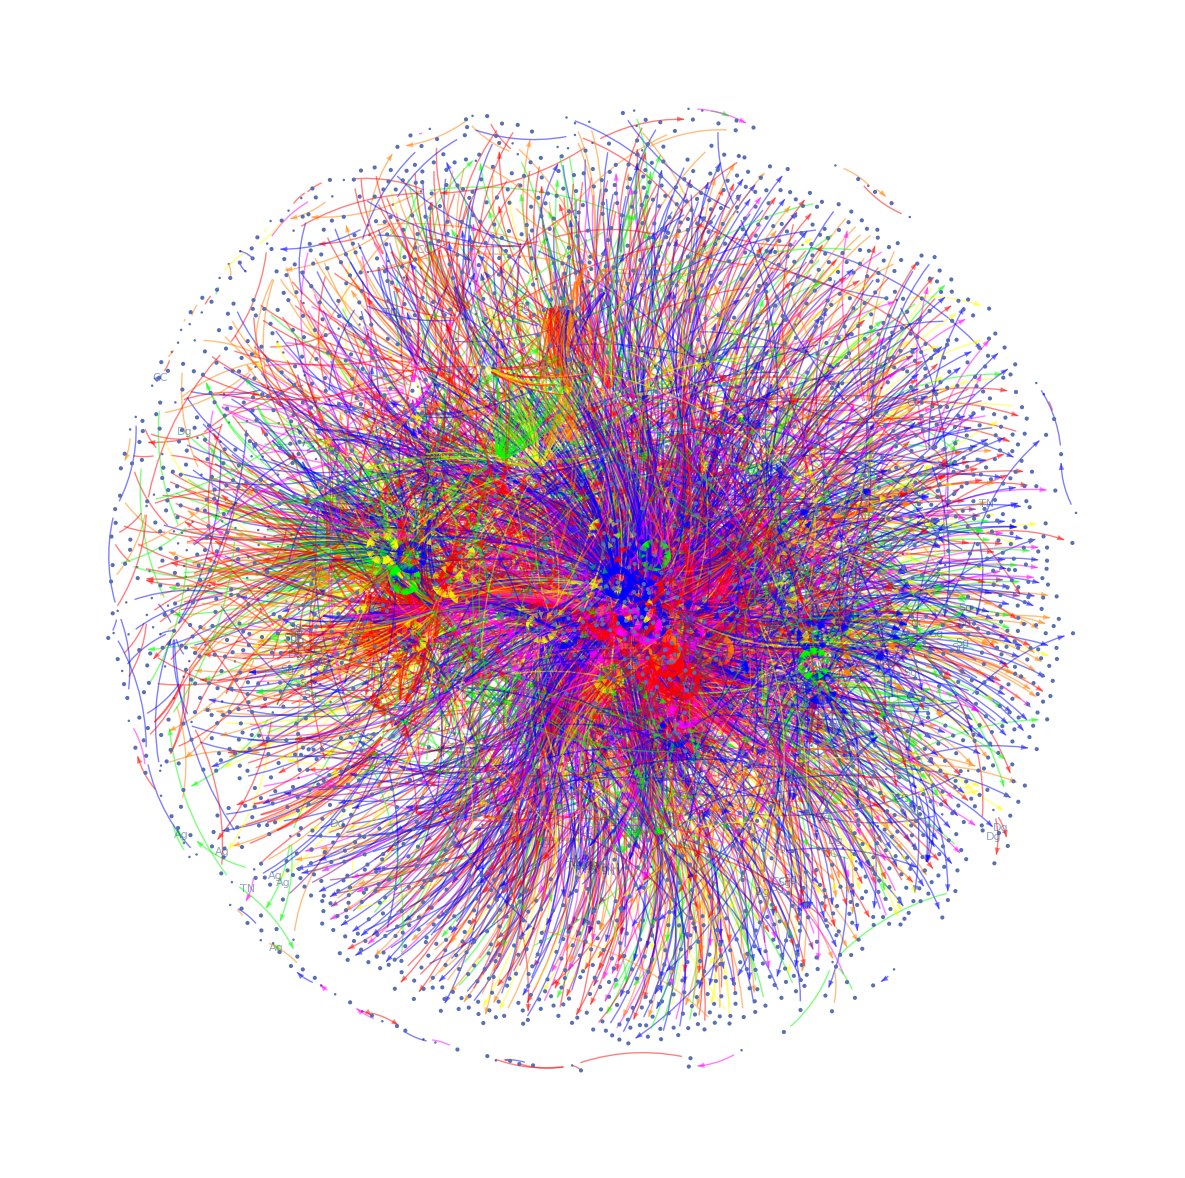

```mathematica
shownGraph=Graph[ nodos, VertexLabels->Placed[Automatic,Center], VertexSize->VertexSizes[initialGraph], GraphLayout->"GravityEmbedding"]
```

Parte pendiente de revisar ---------

```mathematica
(*Seccion que busca sacar la que sería la lista de nodos particular en una columna, en este caso documentos, con el fin de poderles darles estilo de manera individual*)
documentos = {};
Table[AppendTo[documentos,dataFixed[[i,3]]],{i,2, numRegToEval}];
Table[dataFixed[[i,1]],{i, 2,numRegToEval}];
documentos=DeleteDuplicates[documentos];
```

```mathematica
(*Resaltando nodos de tokens*)
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Ag"],LightGreen]];
shownGraph =HighlightGraph[shownGraph,Style[dicTokens["CC"],LightBlue]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Cm"],LightYellow]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Dg"],LightRed]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Sg"],LightOrange]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TNM"],LightPurple]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TN"],LightMagenta]];
(*shownGraph = HighlightGraph[shownGraph, documentos, GraphHighlightStyle -> "VertexConcaveDiamond"];*)
```

Datos grafo completo

```mathematica
GetInfoGraph[g_]:=Module[{},
Print["Información del Grafo"];
Print["Cantidad de Nodos = ",VertexCount[g]];
Print["Cantidad de Enlaces = ",EdgeCount[g]];
Print["Grado promedio = ", N[Mean[VertexDegree[g]]]]];
```

```mathematica
GetInfoGraph[shownGraph]
```

Información del Grafo

Cantidad de Nodos = 3236

Cantidad de Enlaces = 9047

Grado promedio = 5.59147

Extracción de ids de historias clínicas de cada comunidad entre las listas seleccionadas

```mathematica
GetHistoriasClins[graph_]:=Select[VertexList[graph],StringMatchQ[ToString[#],"H:"~~NumberString]&];
```

```mathematica
historiasComunidades=GetHistoriasClins[shownGraph];
```

Función de proyección de un grafo biparito

```mathematica
generateEdges[vertices_List]:=If[Length[vertices]>1,Subsets[vertices,{2}]/. {a_,b_}:>a<->b,{}];
```

```mathematica
project[graph_,vertices_]:=Module[{adjList,edges,g},
adjList=AdjacencyList[graph];
adjList =DeleteCases[Table[If[Length[adjList[[i]]]>1,adjList[[i]]],{i, Length[adjList]}],Null];
(*Print[adjList];*);
edges=DeleteDuplicates[Flatten[Table[generateEdges[adjList[[i]]],{i,Length[adjList]}]]];
(*Print[edges];*);
g=Graph[edges,EdgeWeight->{}];
VertexDelete[g,vertices]];
```

```mathematica
proyeccionEntidades=project[shownGraph,historiasComunidades];
```

```mathematica
GetInfoGraph[proyeccionEntidades]
```

Información del Grafo

Cantidad de Nodos = 2434

Cantidad de Enlaces = 46344

Grado promedio = 38.0805

Funcion que le asigna peso a los enlaces de un grafo de acuerdo al coeficiente de Jaccard

```mathematica
(*Funcion que recibe un enlace de la forma a<->b y un grafo al que pertenece, retorna la expresión (a<->b -> VertexJaccardSimilarity(grafo,a,b))*)
JaccardIndexEdge[edge_,graph_]:=Module[{},
gp=Graph[edge];
nodosEnlace=VertexList[gp];
If[Length[nodosEnlace]==1,edge->VertexJaccardSimilarity[graph,nodosEnlace[[1]],nodosEnlace[[1]]],edge->N[VertexJaccardSimilarity[graph,nodosEnlace[[1]],nodosEnlace[[2]]]]]
];
```

```mathematica
(*Funcion que recibe grafo y retorna la lista de pesos de los enlaces según el coeficiente de jaccard de la forma: {1<->2->1/3,2<->3->1/3,3<->1->1/3}*)
ListWeightsJaccard[graph_]:=Module[{},
listaEnlaces=EdgeList[graph];
listaPesos=Table[JaccardIndexEdge[listaEnlaces[[i]],graph],{i,Length[listaEnlaces]}]
];
```

```mathematica
(*Funcion que recibe grafo y retorna el mismo, pero donde los pesos de los enlaces de este vienen definidos según el coeficiente de Jaccard*)
AssignWeightsJaccard[graph_]:=Module[{},
listaEnlaces=EdgeList[graph];
listaPesos=ListWeightsJaccard[graph];
Graph[listaEnlaces,EdgeWeight->listaPesos]
];
```

```mathematica
grafoInicialAnalisis=AssignWeightsJaccard[proyeccionEntidades];
```

```mathematica
GetInfoGraph[grafoInicialAnalisis]
```

Información del Grafo

Cantidad de Nodos = 2434

Cantidad de Enlaces = 46344

Grado promedio = 38.0805

Analisis de distribución de grados de la proyección y distribución del peso de los enlaces

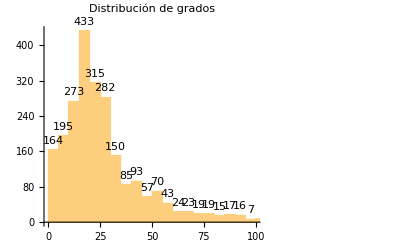

```mathematica
Histogram[VertexDegree[grafoInicialAnalisis],PlotLabel->Style["Distribución de grados","Title",14],LabelingFunction->Above]
```

```mathematica
pesoEnlaces=AnnotationValue[grafoInicialAnalisis,EdgeWeight];
```

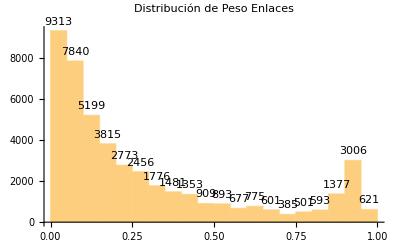

```mathematica
Histogram[pesoEnlaces,PlotLabel->Style["Distribución de Peso Enlaces","Title",14],LabelingFunction->Above]
```

Considerando los histogramas, en particular el de peso de los enlaces se va a definir una límite inferior de 0.9 para el peso de los enlaces, con el fin de filtrar conexiones que no sean tan interesantes

```mathematica
enlaces=EdgeList[grafoInicialAnalisis];
```

```mathematica
Filtrar[graph_,pesoEnlaces_,umbral_]:=Module[{enlacesSeleccionados={}},
enlaces=EdgeList[graph];
enlacesToEliminar=(#<umbral)&/@pesoEnlaces;
enlacesSeleccionados=Pick[enlaces,enlacesToEliminar];
EdgeDelete[graph,enlacesSeleccionados]
]
```

```mathematica
grafoAnalisisFiltradoPeso = Filtrar[grafoInicialAnalisis,pesoEnlaces,0.9];
```

Analisis de distribución de grados de la proyección y distribución del peso de los enlaces del grafo filtrado con un umbral del 0.9 sobre el peso de los enlaces

```mathematica
GetInfoGraph[grafoAnalisisFiltradoPeso]
```

Información del Grafo

Cantidad de Nodos = 2434

Cantidad de Enlaces = 3627

Grado promedio = 2.98028

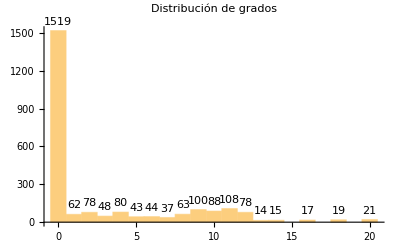

```mathematica
Histogram[VertexDegree[grafoAnalisisFiltradoPeso],PlotLabel->Style["Distribución de grados","Title",14],LabelingFunction->Above]
```

```mathematica
pesoEnlacesFiltrado=AnnotationValue[grafoAnalisisFiltradoPeso,EdgeWeight];
```

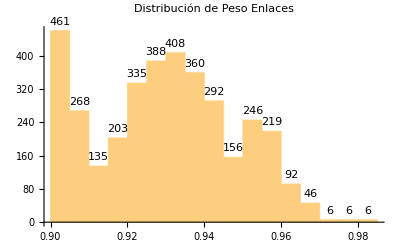

```mathematica
Histogram[pesoEnlacesFiltrado,PlotLabel->Style["Distribución de Peso Enlaces","Title",14],LabelingFunction->Above]
```

Considerando la distribución de grados y viendo que hay muchos de grado 0  se eliminan aquellos nodos de grado <=1

```mathematica
nodosDescartados=Select[VertexList[grafoAnalisisFiltradoPeso],VertexDegree[grafoAnalisisFiltradoPeso,#]<=1&];
grafoFinal=VertexDelete[grafoAnalisisFiltradoPeso,verticesWithDegreeZero];
```

VertexDelete::inv: The argument verticesWithDegreeZero in VertexDelete[Graph[<2434>, <3627>], verticesWithDegreeZero] is not a valid vertex.

Información del Grafo

VertexCount::graph: A graph object is expected at position 1 in ….

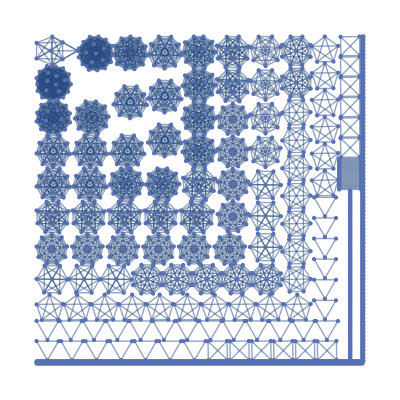
Cantidad de Nodos = VertexCount[VertexDelete[-Graphics-,verticesWithDegreeZero]]

EdgeCount::graph: A graph object is expected at position 1 in ….

Cantidad de Enlaces = EdgeCount[VertexDelete[-Graphics-,verticesWithDegreeZero]]

VertexDegree::graph: A graph object is expected at position 1 in ….

Grado promedio = Mean[VertexDegree[VertexDelete[-Graphics-,verticesWithDegreeZero]]]

```mathematica
GetInfoGraph[grafoFinal]
```

```mathematica
Histogram[VertexDegree[grafoFinal],PlotLabel->Style["Distribución de grados","Title",14],LabelingFunction->Above]
```

VertexDegree::graph: A graph object is expected at position 1 in ….

Histogram::ldata: … is not a valid dataset or list of datasets.

Histogram[VertexDegree[VertexDelete[-Graphics-,verticesWithDegreeZero]],PlotLabel→Distribución de grados,LabelingFunction→Above]

```mathematica
pesoEnlacesFiltradoa=AnnotationValue[grafoFinal,EdgeWeight];
```

AnnotationValue::pvobj: … is not an object with annotations.

```mathematica
Histogram[pesoEnlacesFiltradoa,PlotLabel->Style["Distribución de Peso Enlaces","Title",14],LabelingFunction->Above]
```

Histogram::ldata: … is not a valid dataset or list of datasets.

Histogram[AnnotationValue[VertexDelete[-Graphics-,verticesWithDegreeZero],EdgeWeight],PlotLabel→Distribución de Peso Enlaces,LabelingFunction→Above]

```mathematica
GraphPlot[grafoFinal,PlotTheme->"Scientific"]
```

GraphPlot::graph: A graph object is expected at position 1 in ….

GraphPlot[VertexDelete[-Graphics-,verticesWithDegreeZero],PlotTheme→Scientific]

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

GRAFO DE COMUNIDADES -  No se muestra por su dimensión de acuerdo al dataset

```mathematica
CommunityGraphPlot[grafoFinal, PlotLegends->Placed[Automatic,Below]]
```

CommunityGraphPlot::graph: A graph object is expected at position 1 in ….

CommunityGraphPlot[VertexDelete[-Graphics-,verticesWithDegreeZero],PlotLegends→Placed[Automatic,Below]]

Revisión de comunidades, análisis que busca segmentar grupos de pacientes

```mathematica
comunidades=FindGraphCommunities[grafoFinal];
Length[grafoFinal]
```

FindGraphCommunities::graph: A graph object is expected at position 1 in ….

2